```mathematica
1+1
```

2

```mathematica
x = 1.0;
```

```mathematica
y = x;
```

```mathematica
z:=x;
```

```mathematica
Print[x]
```

1.

```mathematica
Print[y]
```

1.

```mathematica
Print[z]
```

1.

```mathematica
x = 2.0;
```

```mathematica
Print[x]
```

2.

```mathematica
Print[y]
```

1.

```mathematica
Print[z]
```

2.

```mathematica
Hold[FullForm[x = 1]]
```

Hold[Set[x,1]]

```mathematica
Hold[FullForm[z:=x]]
```

Hold[SetDelayed[z,x]]

```mathematica
Clear[x , y , z]
```

```mathematica
{x , y , z} = {1.0 , 2.0 , 3.0};
```

```mathematica
Print[{x , y , z}]
```

{1.,2.,3.}

```mathematica
Hold[FullForm[{x , y , z} = {1.0 , 2.0 , 3.0}]]
```

Hold[Set[List[x,y,z],List[1.,2.,3.]]]

```mathematica
FullForm[{1.0 , 2.0 , 3.0}]
```

List[1.,2.,3.]

```mathematica
Hold[FullForm[{1.0 , 2.0 , 3.0}]]
```

Hold[List[1.,2.,3.]]

```mathematica
Clear[x , y , z]
```

```mathematica
Factorial[3]
```

6

```mathematica
3!
```

6

```mathematica
Hold[FullForm[3!]]
```

Hold[Factorial[3]]

```mathematica
Factorial[0]
```

1

```mathematica
silnia[0] = 1;
```

```mathematica
silnia[n_]:=silnia[n -1] n;
```

```mathematica
silnia[1]
```

1

```mathematica
silnia[2]
```

2

```mathematica
silnia[3]
```

6

```mathematica
silnia[10]
```

3628800

```mathematica
Factorial[10]
```

3628800

```mathematica
FullSimplify[1 + 2 x + x^2]
```

(1+x)^2

```mathematica
(*to jest komentarz*)
```

```mathematica
(*ctrl + 6*)
```

```mathematica
(1 + x)^2
```

(1+x)^2

```mathematica
Hold[FullForm[(1 + x)^2]]
```

Hold[Power[Plus[1,x],2]]

```mathematica
Power[1 + x , 2]
```

(1+x)^2

```mathematica
(*- + >*)
```

```mathematica
FullSimplify[x + 2 >0 ,Assumptions-> x>0]
```

True

```mathematica
f[x_ , y_]:=If[x^2 + y^2<0.75^2,True,False];
```

```mathematica
f[0.1 , 0.3]
```

True

```mathematica
f[1.1 , 2.2]
```

False

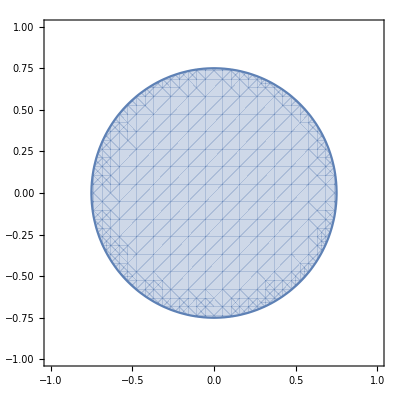

```mathematica
RegionPlot[f[x , y] , {x , -1 , 1} , {y , -1 , 1}]
```

```mathematica
covidData = Import["https://github.com/CSSEGISandData/COVID-19/raw/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
```

```mathematica
covidData//TableForm
```

Province/State | Country/Region | Lat | Long | 1/22/20 | 1/23/20 | 1/24/20 | 1/25/20 | 1/26/20 | 1/27/20 | 1/28/20 | 1/29/20 | 1/30/20 | 1/31/20 | 2/1/20 | 2/2/20 | 2/3/20 | 2/4/20 | 2/5/20 | 2/6/20 | 2/7/20 | 2/8/20 | 2/9/20 | 2/10/20 | 2/11/20 | 2/12/20 | 2/13/20 | 2/14/20 | 2/15/20 | 2/16/20 | 2/17/20 | 2/18/20 | 2/19/20 | 2/20/20 | 2/21/20 | 2/22/20 | 2/23/20 | 2/24/20 | 2/25/20 | 2/26/20 | 2/27/20 | 2/28/20 | 2/29/20 | 3/1/20 | 3/2/20 | 3/3/20 | 3/4/20 | 3/5/20 | 3/6/20 | 3/7/20 | 3/8/20 | 3/9/20 | 3/10/20 | 3/11/20 | 3/12/20 | 3/13/20 | 3/14/20 | 3/15/20 | 3/16/20 | 3/17/20 | 3/18/20 | 3/19/20 | 3/20/20 | 3/21/20 | 3/22/20 | 3/23/20 | 3/24/20 | 3/25/20 | 3/26/20 | 3/27/20 | 3/28/20 | 3/29/20 | 3/30/20 | 3/31/20 | 4/1/20 | 4/2/20 | 4/3/20 | 4/4/20 | 4/5/20 | 4/6/20 | 4/7/20 | 4/8/20 | 4/9/20 | 4/10/20 | 4/11/20 | 4/12/20 | 4/13/20 | 4/14/20 | 4/15/20 | 4/16/20 | 4/17/20 | 4/18/20 | 4/19/20 | 4/20/20 | 4/21/20 | 4/22/20 | 4/23/20 | 4/24/20 | 4/25/20 | 4/26/20 | 4/27/20 | 4/28/20 | 4/29/20 | 4/30/20 | 5/1/20 | 5/2/20 | 5/3/20 | 5/4/20 | 5/5/20 | 5/6/20 | 5/7/20 | 5/8/20 | 5/9/20 | 5/10/20 | 5/11/20 | 5/12/20 | 5/13/20 | 5/14/20 | 5/15/20 | 5/16/20 | 5/17/20 | 5/18/20 | 5/19/20 | 5/20/20 | 5/21/20 | 5/22/20 | 5/23/20 | 5/24/20 | 5/25/20 | 5/26/20 | 5/27/20 | 5/28/20 | 5/29/20 | 5/30/20 | 5/31/20 | 6/1/20 | 6/2/20 | 6/3/20 | 6/4/20 | 6/5/20 | 6/6/20 | 6/7/20 | 6/8/20 | 6/9/20 | 6/10/20 | 6/11/20 | 6/12/20 | 6/13/20 | 6/14/20 | 6/15/20 | 6/16/20 | 6/17/20 | 6/18/20 | 6/19/20 | 6/20/20 | 6/21/20 | 6/22/20 | 6/23/20 | 6/24/20 | 6/25/20 | 6/26/20 | 6/27/20 | 6/28/20 | 6/29/20 | 6/30/20 | 7/1/20 | 7/2/20 | 7/3/20 | 7/4/20 | 7/5/20 | 7/6/20 | 7/7/20 | 7/8/20 | 7/9/20 | 7/10/20 | 7/11/20 | 7/12/20 | 7/13/20 | 7/14/20 | 7/15/20 | 7/16/20 | 7/17/20 | 7/18/20 | 7/19/20 | 7/20/20 | 7/21/20 | 7/22/20 | 7/23/20 | 7/24/20 | 7/25/20 | 7/26/20 | 7/27/20 | 7/28/20 | 7/29/20 | 7/30/20 | 7/31/20 | 8/1/20 | 8/2/20 | 8/3/20 | 8/4/20 | 8/5/20 | 8/6/20 | 8/7/20 | 8/8/20 | 8/9/20 | 8/10/20 | 8/11/20 | 8/12/20 | 8/13/20 | 8/14/20 | 8/15/20 | 8/16/20 | 8/17/20 | 8/18/20 | 8/19/20 | 8/20/20 | 8/21/20 | 8/22/20 | 8/23/20 | 8/24/20 | 8/25/20 | 8/26/20 | 8/27/20 | 8/28/20 | 8/29/20 | 8/30/20 | 8/31/20 | 9/1/20 | 9/2/20 | 9/3/20 | 9/4/20 | 9/5/20 | 9/6/20 | 9/7/20 | 9/8/20 | 9/9/20 | 9/10/20 | 9/11/20 | 9/12/20 | 9/13/20 | 9/14/20 | 9/15/20 | 9/16/20 | 9/17/20 | 9/18/20 | 9/19/20 | 9/20/20 | 9/21/20 | 9/22/20 | 9/23/20 | 9/24/20 | 9/25/20 | 9/26/20 | 9/27/20 | 9/28/20 | 9/29/20 | 9/30/20 | 10/1/20 | 10/2/20 | 10/3/20 | 10/4/20 | 10/5/20 | 10/6/20 | 10/7/20 | 10/8/20 | 10/9/20 | 10/10/20 | 10/11/20 | 10/12/20 | 10/13/20 | 10/14/20 | 10/15/20 | 10/16/20 | 10/17/20 | 10/18/20 | 10/19/20 | 10/20/20 | 10/21/20 | 10/22/20 | 10/23/20 | 10/24/20 | 10/25/20 | 10/26/20 | 10/27/20 | 10/28/20 | 10/29/20 | 10/30/20 | 10/31/20 | 11/1/20 | 11/2/20 | 11/3/20 | 11/4/20 | 11/5/20 | 11/6/20 | 11/7/20 | 11/8/20 | 11/9/20 | 11/10/20 | 11/11/20 | 11/12/20 | 11/13/20 | 11/14/20 | 11/15/20 | 11/16/20 | 11/17/20 | 11/18/20 | 11/19/20 | 11/20/20 | 11/21/20 | 11/22/20 | 11/23/20 | 11/24/20 | 11/25/20 | 11/26/20 | 11/27/20 | 11/28/20 | 11/29/20 | 11/30/20 | 12/1/20 | 12/2/20 | 12/3/20 | 12/4/20 | 12/5/20 | 12/6/20 | 12/7/20 | 12/8/20 | 12/9/20 | 12/10/20 | 12/11/20 | 12/12/20 | 12/13/20 | 12/14/20 | 12/15/20 | 12/16/20 | 12/17/20 | 12/18/20 | 12/19/20 | 12/20/20 | 12/21/20 | 12/22/20 | 12/23/20 | 12/24/20 | 12/25/20 | 12/26/20 | 12/27/20 | 12/28/20 | 12/29/20 | 12/30/20 | 12/31/20 | 1/1/21 | 1/2/21 | 1/3/21 | 1/4/21 | 1/5/21 | 1/6/21 | 1/7/21 | 1/8/21 | 1/9/21 | 1/10/21 | 1/11/21 | 1/12/21 | 1/13/21 | 1/14/21 | 1/15/21 | 1/16/21 | 1/17/21 | 1/18/21 | 1/19/21 | 1/20/21 | 1/21/21 | 1/22/21 | 1/23/21 | 1/24/21 | 1/25/21 | 1/26/21 | 1/27/21 | 1/28/21 | 1/29/21 | 1/30/21 | 1/31/21 | 2/1/21 | 2/2/21 | 2/3/21 | 2/4/21 | 2/5/21 | 2/6/21 | 2/7/21 | 2/8/21 | 2/9/21 | 2/10/21 | 2/11/21 | 2/12/21 | 2/13/21 | 2/14/21 | 2/15/21 | 2/16/21 | 2/17/21 | 2/18/21 | 2/19/21 | 2/20/21 | 2/21/21 | 2/22/21 | 2/23/21 | 2/24/21 | 2/25/21 | 2/26/21 | 2/27/21 | 2/28/21 | 3/1/21 | 3/2/21 | 3/3/21 | 3/4/21 | 3/5/21 | 3/6/21 | 3/7/21 | 3/8/21 | 3/9/21 | 3/10/21 | 3/11/21 | 3/12/21 | 3/13/21 | 3/14/21 | 3/15/21 | 3/16/21 | 3/17/21 | 3/18/21 | 3/19/21 | 3/20/21 | 3/21/21 | 3/22/21 | 3/23/21 | 3/24/21 | 3/25/21 | 3/26/21 | 3/27/21 | 3/28/21 | 3/29/21 | 3/30/21 | 3/31/21 | 4/1/21 | 4/2/21 | 4/3/21 | 4/4/21 | 4/5/21 | 4/6/21 | 4/7/21 | 4/8/21 | 4/9/21 | 4/10/21 | 4/11/21 | 4/12/21 | 4/13/21 | 4/14/21 | 4/15/21 | 4/16/21 | 4/17/21 | 4/18/21 | 4/19/21 | 4/20/21 | 4/21/21 | 4/22/21 | 4/23/21 | 4/24/21 | 4/25/21 | 4/26/21 | 4/27/21 | 4/28/21 | 4/29/21 | 4/30/21 | 5/1/21 | 5/2/21 | 5/3/21 | 5/4/21 | 5/5/21 | 5/6/21 | 5/7/21 | 5/8/21 | 5/9/21 | 5/10/21 | 5/11/21 | 5/12/21 | 5/13/21 | 5/14/21 | 5/15/21 | 5/16/21 | 5/17/21 | 5/18/21 | 5/19/21 | 5/20/21 | 5/21/21 | 5/22/21 | 5/23/21 | 5/24/21 | 5/25/21 | 5/26/21 | 5/27/21 | 5/28/21 | 5/29/21 | 5/30/21 | 5/31/21 | 6/1/21 | 6/2/21 | 6/3/21 | 6/4/21 | 6/5/21 | 6/6/21 | 6/7/21 | 6/8/21 | 6/9/21 | 6/10/21 | 6/11/21 | 6/12/21 | 6/13/21 | 6/14/21 | 6/15/21 | 6/16/21 | 6/17/21 | 6/18/21 | 6/19/21 | 6/20/21 | 6/21/21 | 6/22/21 | 6/23/21 | 6/24/21 | 6/25/21 | 6/26/21 | 6/27/21 | 6/28/21 | 6/29/21 | 6/30/21 | 7/1/21 | 7/2/21 | 7/3/21 | 7/4/21 | 7/5/21 | 7/6/21 | 7/7/21 | 7/8/21 | 7/9/21 | 7/10/21 | 7/11/21 | 7/12/21 | 7/13/21 | 7/14/21 | 7/15/21 | 7/16/21 | 7/17/21 | 7/18/21 | 7/19/21 | 7/20/21 | 7/21/21 | 7/22/21 | 7/23/21 | 7/24/21 | 7/25/21 | 7/26/21 | 7/27/21 | 7/28/21 | 7/29/21 | 7/30/21 | 7/31/21 | 8/1/21 | 8/2/21 | 8/3/21 | 8/4/21 | 8/5/21 | 8/6/21 | 8/7/21 | 8/8/21 | 8/9/21 | 8/10/21 | 8/11/21 | 8/12/21 | 8/13/21 | 8/14/21 | 8/15/21 | 8/16/21 | 8/17/21 | 8/18/21 | 8/19/21 | 8/20/21 | 8/21/21 | 8/22/21 | 8/23/21 | 8/24/21 | 8/25/21 | 8/26/21 | 8/27/21 | 8/28/21 | 8/29/21 | 8/30/21 | 8/31/21 | 9/1/21 | 9/2/21 | 9/3/21 | 9/4/21 | 9/5/21 | 9/6/21 | 9/7/21 | 9/8/21 | 9/9/21 | 9/10/21 | 9/11/21 | 9/12/21 | 9/13/21 | 9/14/21 | 9/15/21 | 9/16/21 | 9/17/21 | 9/18/21 | 9/19/21 | 9/20/21 | 9/21/21 | 9/22/21 | 9/23/21 | 9/24/21 | 9/25/21 | 9/26/21 | 9/27/21 | 9/28/21 | 9/29/21 | 9/30/21 | 10/1/21 | 10/2/21 | 10/3/21 | 10/4/21 | 10/5/21 | 10/6/21 | 10/7/21 | 10/8/21 | 10/9/21 | 10/10/21 | 10/11/21 | 10/12/21 | 10/13/21 | 10/14/21 | 10/15/21 | 10/16/21 | 10/17/21 | 10/18/21 | 10/19/21 | 10/20/21 | 10/21/21 | 10/22/21 | 10/23/21 | 10/24/21 | 10/25/21 | 10/26/21 | 10/27/21 | 10/28/21 | 10/29/21 | 10/30/21 | 10/31/21 | 11/1/21 | 11/2/21 | 11/3/21 | 11/4/21 | 11/5/21 | 11/6/21 | 11/7/21 | 11/8/21 | 11/9/21 | 11/10/21 | 11/11/21 | 11/12/21 | 11/13/21 | 11/14/21 | 11/15/21 | 11/16/21 | 11/17/21 | 11/18/21 | 11/19/21 | 11/20/21 | 11/21/21 | 11/22/21 | 11/23/21 | 11/24/21 | 11/25/21 | 11/26/21 | 11/27/21 | 11/28/21 | 11/29/21 | 11/30/21 | 12/1/21 | 12/2/21 | 12/3/21 | 12/4/21 | 12/5/21 | 12/6/21 | 12/7/21 | 12/8/21 | 12/9/21 | 12/10/21 | 12/11/21 | 12/12/21 | 12/13/21 | 12/14/21 | 12/15/21 | 12/16/21 | 12/17/21 | 12/18/21 | 12/19/21 | 12/20/21 | 12/21/21 | 12/22/21 | 12/23/21 | 12/24/21 | 12/25/21 | 12/26/21 | 12/27/21 | 12/28/21 | 12/29/21 | 12/30/21 | 12/31/21 | 1/1/22 | 1/2/22 | 1/3/22 | 1/4/22 | 1/5/22 | 1/6/22 | 1/7/22 | 1/8/22 | 1/9/22 | 1/10/22 | 1/11/22 | 1/12/22 | 1/13/22 | 1/14/22 | 1/15/22 | 1/16/22 | 1/17/22 | 1/18/22 | 1/19/22 | 1/20/22 | 1/21/22 | 1/22/22 | 1/23/22 | 1/24/22 | 1/25/22 | 1/26/22 | 1/27/22 | 1/28/22 | 1/29/22 | 1/30/22 | 1/31/22 | 2/1/22 | 2/2/22 | 2/3/22 | 2/4/22 | 2/5/22 | 2/6/22 | 2/7/22 | 2/8/22 | 2/9/22 | 2/10/22 | 2/11/22 | 2/12/22 | 2/13/22 | 2/14/22 | 2/15/22 | 2/16/22 | 2/17/22 | 2/18/22 | 2/19/22 | 2/20/22 | 2/21/22 | 2/22/22 | 2/23/22 | 2/24/22 | 2/25/22 | 2/26/22 | 2/27/22 | 2/28/22 | 3/1/22 | 3/2/22 | 3/3/22 | 3/4/22 | 3/5/22 | 3/6/22 | 3/7/22 | 3/8/22 | 3/9/22 | 3/10/22 | 3/11/22 | 3/12/22 | 3/13/22 | 3/14/22 | 3/15/22 | 3/16/22 | 3/17/22 | 3/18/22 | 3/19/22 | 3/20/22 | 3/21/22 | 3/22/22 | 3/23/22 | 3/24/22 | 3/25/22 | 3/26/22 | 3/27/22 | 3/28/22 | 3/29/22 | 3/30/22 | 3/31/22 | 4/1/22 | 4/2/22 | 4/3/22 | 4/4/22 | 4/5/22 | 4/6/22 | 4/7/22 | 4/8/22 | 4/9/22 | 4/10/22 | 4/11/22 | 4/12/22 | 4/13/22 | 4/14/22 | 4/15/22 | 4/16/22 | 4/17/22 | 4/18/22 | 4/19/22 | 4/20/22 | 4/21/22 | 4/22/22 | 4/23/22 | 4/24/22 | 4/25/22 | 4/26/22 | 4/27/22 | 4/28/22 | 4/29/22 | 4/30/22 | 5/1/22 | 5/2/22 | 5/3/22 | 5/4/22 | 5/5/22 | 5/6/22 | 5/7/22 | 5/8/22 | 5/9/22 | 5/10/22 | 5/11/22 | 5/12/22 | 5/13/22 | 5/14/22 | 5/15/22 | 5/16/22 | 5/17/22 | 5/18/22 | 5/19/22 | 5/20/22 | 5/21/22 | 5/22/22 | 5/23/22 | 5/24/22 | 5/25/22 | 5/26/22 | 5/27/22 | 5/28/22 | 5/29/22 | 5/30/22 | 5/31/22 | 6/1/22 | 6/2/22 | 6/3/22 | 6/4/22 | 6/5/22 | 6/6/22 | 6/7/22 | 6/8/22 | 6/9/22 | 6/10/22 | 6/11/22 | 6/12/22 | 6/13/22 | 6/14/22 | 6/15/22 | 6/16/22 | 6/17/22 | 6/18/22 | 6/19/22 | 6/20/22 | 6/21/22 | 6/22/22 | 6/23/22 | 6/24/22 | 6/25/22 | 6/26/22 | 6/27/22 | 6/28/22 | 6/29/22 | 6/30/22 | 7/1/22 | 7/2/22 | 7/3/22 | 7/4/22 | 7/5/22 | 7/6/22 | 7/7/22 | 7/8/22 | 7/9/22 | 7/10/22 | 7/11/22 | 7/12/22 | 7/13/22 | 7/14/22 | 7/15/22 | 7/16/22 | 7/17/22 | 7/18/22 | 7/19/22 | 7/20/22 | 7/21/22 | 7/22/22 | 7/23/22 | 7/24/22 | 7/25/22 | 7/26/22 | 7/27/22 | 7/28/22 | 7/29/22 | 7/30/22 | 7/31/22 | 8/1/22 | 8/2/22 | 8/3/22 | 8/4/22 | 8/5/22 | 8/6/22 | 8/7/22 | 8/8/22 | 8/9/22 | 8/10/22 | 8/11/22 | 8/12/22 | 8/13/22 | 8/14/22 | 8/15/22 | 8/16/22 | 8/17/22 | 8/18/22 | 8/19/22 | 8/20/22 | 8/21/22 | 8/22/22 | 8/23/22 | 8/24/22 | 8/25/22 | 8/26/22 | 8/27/22 | 8/28/22 | 8/29/22 | 8/30/22 | 8/31/22 | 9/1/22 | 9/2/22 | 9/3/22 | 9/4/22 | 9/5/22 | 9/6/22 | 9/7/22 | 9/8/22 | 9/9/22 | 9/10/22 | 9/11/22 | 9/12/22 | 9/13/22 | 9/14/22 | 9/15/22 | 9/16/22 | 9/17/22 | 9/18/22 | 9/19/22 | 9/20/22 | 9/21/22 | 9/22/22 | 9/23/22 | 9/24/22 | 9/25/22 | 9/26/22 | 9/27/22 | 9/28/22 | 9/29/22 | 9/30/22 | 10/1/22 | 10/2/22 | 10/3/22 | 10/4/22 | 10/5/22 | 10/6/22 | 10/7/22 | 10/8/22 | 10/9/22 | 10/10/22
 | Afghanistan | 33.9391 | 67.71 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 8 | 8 | 8 | 8 | 11 | 11 | 11 | 14 | 20 | 25 | 26 | 26 | 26 | 24 | 24 | 34 | 40 | 42 | 74 | 80 | 91 | 106 | 114 | 114 | 166 | 192 | 235 | 269 | 270 | 299 | 337 | 367 | 423 | 444 | 521 | 521 | 555 | 607 | 665 | 770 | 794 | 845 | 908 | 933 | 996 | 1026 | 1092 | 1176 | 1226 | 1330 | 1463 | 1531 | 1703 | 1827 | 1827 | 2171 | 2469 | 2469 | 2469 | 2469 | 3224 | 3392 | 3563 | 3563 | 4402 | 4664 | 4967 | 4967 | 5339 | 6053 | 6402 | 6635 | 7072 | 7655 | 8145 | 8676 | 9216 | 9952 | 10668 | 11180 | 11917 | 12465 | 13102 | 13745 | 14529 | 15180 | 15836 | 16578 | 17353 | 17977 | 19055 | 19637 | 20428 | 21003 | 21308 | 22228 | 22976 | 23632 | 24188 | 24852 | 25613 | 25719 | 26960 | 27423 | 27964 | 28383 | 28919 | 29229 | 29567 | 29726 | 30261 | 30346 | 30702 | 31053 | 31324 | 31445 | 31848 | 32108 | 32410 | 32758 | 33037 | 33150 | 33470 | 33680 | 33739 | 34280 | 34437 | 34537 | 34541 | 34826 | 35026 | 35156 | 35315 | 35375 | 35561 | 35595 | 35701 | 35813 | 36001 | 36067 | 36122 | 36243 | 36349 | 36454 | 36557 | 36628 | 36628 | 36796 | 36796 | 36796 | 36833 | 36915 | 36982 | 37023 | 37101 | 37140 | 37140 | 37355 | 37431 | 37510 | 37517 | 37637 | 37682 | 37682 | 37685 | 37685 | 37845 | 37942 | 37980 | 38039 | 38085 | 38156 | 38199 | 38215 | 38226 | 38229 | 38229 | 38248 | 38282 | 38329 | 38374 | 38374 | 38390 | 38484 | 38580 | 38606 | 38630 | 38658 | 38692 | 38727 | 38802 | 38858 | 38901 | 38941 | 38958 | 38969 | 39005 | 39130 | 39160 | 39182 | 39231 | 39256 | 39272 | 39278 | 39313 | 39325 | 39340 | 39354 | 39371 | 39376 | 39383 | 39427 | 39508 | 39572 | 39634 | 39702 | 39779 | 39789 | 39885 | 39956 | 40014 | 40080 | 40112 | 40159 | 40227 | 40286 | 40373 | 40461 | 40461 | 40510 | 40626 | 40687 | 40768 | 40833 | 40937 | 41032 | 41145 | 41268 | 41334 | 41425 | 41501 | 41633 | 41728 | 41814 | 41935 | 41975 | 42033 | 42159 | 42297 | 42463 | 42609 | 42795 | 42969 | 43035 | 43240 | 43403 | 43628 | 43851 | 44228 | 44443 | 44503 | 44706 | 44988 | 45278 | 45490 | 45716 | 45839 | 45966 | 46215 | 46498 | 46717 | 46980 | 47258 | 47388 | 47641 | 47901 | 48136 | 48366 | 48540 | 48753 | 48826 | 48952 | 49273 | 49484 | 49703 | 49927 | 50202 | 50456 | 50536 | 50678 | 50888 | 51070 | 51357 | 51595 | 51764 | 51848 | 52007 | 52147 | 52330 | 52330 | 52513 | 52586 | 52709 | 52909 | 53011 | 53105 | 53207 | 53332 | 53400 | 53489 | 53538 | 53584 | 53690 | 53775 | 53831 | 53938 | 53984 | 54062 | 54141 | 54278 | 54403 | 54483 | 54559 | 54595 | 54672 | 54750 | 54854 | 54891 | 54939 | 55008 | 55023 | 55059 | 55121 | 55174 | 55231 | 55265 | 55330 | 55335 | 55359 | 55384 | 55402 | 55420 | 55445 | 55473 | 55492 | 55514 | 55518 | 55540 | 55557 | 55575 | 55580 | 55604 | 55617 | 55646 | 55664 | 55680 | 55696 | 55707 | 55714 | 55733 | 55759 | 55770 | 55775 | 55827 | 55840 | 55847 | 55876 | 55876 | 55894 | 55917 | 55959 | 55959 | 55985 | 55985 | 55995 | 56016 | 56044 | 56069 | 56093 | 56103 | 56153 | 56177 | 56192 | 56226 | 56254 | 56290 | 56294 | 56322 | 56384 | 56454 | 56517 | 56572 | 56595 | 56676 | 56717 | 56779 | 56873 | 56943 | 57019 | 57144 | 57160 | 57242 | 57364 | 57492 | 57534 | 57612 | 57721 | 57793 | 57898 | 58037 | 58214 | 58312 | 58542 | 58730 | 58843 | 59015 | 59225 | 59370 | 59576 | 59745 | 59939 | 60122 | 60300 | 60563 | 60797 | 61162 | 61455 | 61755 | 61842 | 62063 | 62403 | 62718 | 63045 | 63355 | 63412 | 63484 | 63598 | 63819 | 64122 | 64575 | 65080 | 65486 | 65728 | 66275 | 66903 | 67743 | 68366 | 69130 | 70111 | 70761 | 71838 | 72977 | 74026 | 75119 | 76628 | 77963 | 79224 | 80841 | 82326 | 84050 | 85892 | 87716 | 88740 | 89861 | 91458 | 93272 | 93288 | 96531 | 98734 | 100521 | 101906 | 103902 | 105749 | 107957 | 109532 | 111592 | 113124 | 114220 | 115751 | 117158 | 118659 | 120216 | 122156 | 123485 | 124748 | 125937 | 127464 | 129021 | 130113 | 131586 | 132777 | 133578 | 134653 | 135889 | 136643 | 137853 | 139051 | 140224 | 140602 | 141499 | 142414 | 142762 | 143183 | 143439 | 143666 | 143871 | 144285 | 145008 | 145552 | 145996 | 146523 | 147154 | 147501 | 147985 | 148572 | 148933 | 149361 | 149810 | 150240 | 150458 | 150778 | 151013 | 151291 | 151563 | 151770 | 151941 | 152033 | 152142 | 152243 | 152363 | 152411 | 152448 | 152497 | 152511 | 152583 | 152660 | 152722 | 152822 | 152960 | 153007 | 153033 | 153148 | 153220 | 153260 | 153306 | 153375 | 153395 | 153423 | 153534 | 153626 | 153736 | 153840 | 153962 | 153982 | 153990 | 154094 | 154180 | 154283 | 154361 | 154487 | 154487 | 154487 | 154585 | 154712 | 154757 | 154800 | 154960 | 154960 | 154960 | 155072 | 155093 | 155128 | 155174 | 155191 | 155191 | 155191 | 155287 | 155309 | 155380 | 155429 | 155448 | 155466 | 155508 | 155540 | 155599 | 155627 | 155682 | 155688 | 155739 | 155764 | 155776 | 155801 | 155859 | 155891 | 155931 | 155940 | 155944 | 156040 | 156071 | 156124 | 156166 | 156196 | 156210 | 156250 | 156284 | 156307 | 156323 | 156363 | 156392 | 156397 | 156397 | 156397 | 156397 | 156414 | 156456 | 156487 | 156510 | 156552 | 156610 | 156649 | 156739 | 156739 | 156812 | 156864 | 156896 | 156911 | 157015 | 157032 | 157144 | 157171 | 157190 | 157218 | 157260 | 157289 | 157359 | 157387 | 157412 | 157431 | 157454 | 157499 | 157508 | 157542 | 157585 | 157603 | 157611 | 157633 | 157648 | 157660 | 157665 | 157725 | 157734 | 157745 | 157787 | 157797 | 157816 | 157841 | 157878 | 157887 | 157895 | 157951 | 157967 | 157998 | 158037 | 158056 | 158084 | 158107 | 158189 | 158183 | 158205 | 158245 | 158275 | 158300 | 158309 | 158381 | 158394 | 158471 | 158511 | 158602 | 158639 | 158678 | 158717 | 158826 | 158974 | 159070 | 159303 | 159516 | 159548 | 159649 | 159896 | 160252 | 160692 | 161004 | 161057 | 161290 | 162111 | 162926 | 163555 | 164190 | 164727 | 165358 | 165711 | 166191 | 166924 | 167739 | 168550 | 169448 | 169940 | 170152 | 170604 | 171246 | 171422 | 171519 | 171673 | 171857 | 171931 | 172205 | 172441 | 172716 | 172901 | 173047 | 173084 | 173146 | 173395 | 173659 | 173879 | 174073 | 174214 | 174214 | 174331 | 174582 | 175000 | 175353 | 175525 | 175893 | 175974 | 176039 | 176201 | 176409 | 176571 | 176743 | 176918 | 176983 | 177039 | 177093 | 177191 | 177255 | 177321 | 177321 | 177321 | 177321 | 177520 | 177602 | 177658 | 177716 | 177747 | 177782 | 177803 | 177827 | 177897 | 177932 | 177974 | 177974 | 177974 | 177974 | 177974 | 178141 | 178257 | 178295 | 178352 | 178373 | 178387 | 178418 | 178457 | 178513 | 178574 | 178611 | 178638 | 178648 | 178689 | 178745 | 178769 | 178809 | 178850 | 178873 | 178879 | 178899 | 178901 | 178901 | 178901 | 178905 | 178919 | 178922 | 178981 | 179010 | 179017 | 179131 | 179169 | 179203 | 179242 | 179267 | 179321 | 179328 | 179477 | 179597 | 179624 | 179674 | 179716 | 179716 | 179771 | 179835 | 179835 | 180086 | 180122 | 180174 | 180259 | 180347 | 180419 | 180520 | 180584 | 180615 | 180615 | 180688 | 180741 | 180784 | 180864 | 180864 | 180864 | 180864 | 181120 | 181178 | 181236 | 181465 | 181534 | 181574 | 181666 | 181725 | 181808 | 181912 | 181987 | 182033 | 182072 | 182149 | 182228 | 182324 | 182403 | 182528 | 182594 | 182643 | 182724 | 182793 | 182793 | 182979 | 183084 | 183221 | 183235 | 183265 | 183268 | 183272 | 183285 | 183358 | 183407 | 183445 | 183572 | 183687 | 183908 | 184038 | 184224 | 184360 | 184473 | 184587 | 184819 | 185086 | 185272 | 185393 | 185481 | 185552 | 185749 | 185930 | 186120 | 186393 | 186697 | 187037 | 187109 | 187442 | 187685 | 187966 | 188202 | 188506 | 188704 | 188820 | 189045 | 189343 | 189477 | 189710 | 190010 | 190254 | 190435 | 190643 | 191040 | 191247 | 191585 | 191967 | 191967 | 191967 | 192463 | 192906 | 193004 | 193250 | 193520 | 193520 | 193912 | 194163 | 194355 | 194614 | 195012 | 195298 | 195471 | 195631 | 195925 | 196182 | 196404 | 196751 | 196870 | 196992 | 197066 | 197240 | 197434 | 197608 | 197788 | 198023 | 198163 | 198244 | 198416 | 198543 | 198750 | 198876 | 199067 | 199188 | 199310 | 199386 | 199545 | 199690 | 199845 | 199994 | 200130 | 200202 | 200372 | 200469
 | Albania | 41.1533 | 20.1683 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 10 | 12 | 23 | 33 | 38 | 42 | 51 | 55 | 59 | 64 | 70 | 76 | 89 | 104 | 123 | 146 | 174 | 186 | 197 | 212 | 223 | 243 | 259 | 277 | 304 | 333 | 361 | 377 | 383 | 400 | 409 | 416 | 433 | 446 | 467 | 475 | 494 | 518 | 539 | 548 | 562 | 584 | 609 | 634 | 663 | 678 | 712 | 726 | 736 | 750 | 766 | 773 | 782 | 789 | 795 | 803 | 820 | 832 | 842 | 850 | 856 | 868 | 872 | 876 | 880 | 898 | 916 | 933 | 946 | 948 | 949 | 964 | 969 | 981 | 989 | 998 | 1004 | 1029 | 1050 | 1076 | 1099 | 1122 | 1137 | 1143 | 1164 | 1184 | 1197 | 1212 | 1232 | 1246 | 1263 | 1299 | 1341 | 1385 | 1416 | 1464 | 1521 | 1590 | 1672 | 1722 | 1788 | 1838 | 1891 | 1962 | 1995 | 2047 | 2114 | 2192 | 2269 | 2330 | 2402 | 2466 | 2535 | 2580 | 2662 | 2752 | 2819 | 2893 | 2964 | 3038 | 3106 | 3188 | 3278 | 3371 | 3454 | 3571 | 3667 | 3752 | 3851 | 3906 | 4008 | 4090 | 4171 | 4290 | 4358 | 4466 | 4570 | 4637 | 4763 | 4880 | 4997 | 5105 | 5197 | 5276 | 5396 | 5519 | 5620 | 5750 | 5889 | 6016 | 6151 | 6275 | 6411 | 6536 | 6676 | 6817 | 6971 | 7117 | 7260 | 7380 | 7499 | 7654 | 7812 | 7967 | 8119 | 8275 | 8427 | 8605 | 8759 | 8927 | 9083 | 9195 | 9279 | 9380 | 9513 | 9606 | 9728 | 9844 | 9967 | 10102 | 10255 | 10406 | 10553 | 10704 | 10860 | 11021 | 11185 | 11353 | 11520 | 11672 | 11816 | 11948 | 12073 | 12226 | 12385 | 12535 | 12666 | 12787 | 12921 | 13045 | 13153 | 13259 | 13391 | 13518 | 13649 | 13806 | 13965 | 14117 | 14266 | 14410 | 14568 | 14730 | 14899 | 15066 | 15231 | 15399 | 15570 | 15752 | 15955 | 16212 | 16501 | 16774 | 17055 | 17350 | 17651 | 17948 | 18250 | 18556 | 18858 | 19157 | 19445 | 19729 | 20040 | 20315 | 20634 | 20875 | 21202 | 21523 | 21904 | 22300 | 22721 | 23210 | 23705 | 24206 | 24731 | 25294 | 25801 | 26211 | 26701 | 27233 | 27830 | 28432 | 29126 | 29837 | 30623 | 31459 | 32196 | 32761 | 33556 | 34300 | 34944 | 35600 | 36245 | 36790 | 37625 | 38182 | 39014 | 39719 | 40501 | 41302 | 42148 | 42988 | 43683 | 44436 | 45188 | 46061 | 46863 | 47742 | 48530 | 49191 | 50000 | 50637 | 51424 | 52004 | 52542 | 53003 | 53425 | 53814 | 54317 | 54827 | 55380 | 55755 | 56254 | 56572 | 57146 | 57727 | 58316 | 58316 | 58991 | 59438 | 59623 | 60283 | 61008 | 61705 | 62378 | 63033 | 63595 | 63971 | 64627 | 65334 | 65994 | 66635 | 67216 | 67690 | 67982 | 68568 | 69238 | 69916 | 70655 | 71441 | 72274 | 72812 | 73691 | 74567 | 75454 | 76350 | 77251 | 78127 | 78992 | 79934 | 80941 | 81993 | 83082 | 84212 | 85336 | 86289 | 87528 | 88671 | 89776 | 90835 | 91987 | 93075 | 93850 | 94651 | 95726 | 96838 | 97909 | 99062 | 100246 | 101285 | 102306 | 103327 | 104313 | 105229 | 106215 | 107167 | 107931 | 108823 | 109674 | 110521 | 111301 | 112078 | 112897 | 113580 | 114209 | 114840 | 115442 | 116123 | 116821 | 117474 | 118017 | 118492 | 118938 | 119528 | 120022 | 120541 | 121200 | 121544 | 121847 | 122295 | 122767 | 123216 | 123641 | 124134 | 124419 | 124723 | 125157 | 125506 | 125842 | 126183 | 126531 | 126795 | 126936 | 127192 | 127509 | 127795 | 128155 | 128393 | 128518 | 128752 | 128959 | 129128 | 129307 | 129456 | 129594 | 129694 | 129842 | 129980 | 130114 | 130270 | 130409 | 130537 | 130606 | 130736 | 130859 | 130977 | 131085 | 131185 | 131238 | 131276 | 131327 | 131419 | 131510 | 131577 | 131666 | 131723 | 131753 | 131803 | 131845 | 131890 | 131939 | 131978 | 132015 | 132032 | 132071 | 132095 | 132118 | 132153 | 132176 | 132209 | 132215 | 132229 | 132244 | 132264 | 132285 | 132297 | 132309 | 132315 | 132337 | 132351 | 132360 | 132372 | 132374 | 132379 | 132384 | 132397 | 132415 | 132426 | 132437 | 132449 | 132459 | 132461 | 132469 | 132476 | 132481 | 132484 | 132488 | 132490 | 132490 | 132496 | 132497 | 132499 | 132506 | 132509 | 132512 | 132513 | 132514 | 132521 | 132523 | 132526 | 132534 | 132535 | 132537 | 132544 | 132557 | 132565 | 132580 | 132587 | 132592 | 132597 | 132608 | 132616 | 132629 | 132647 | 132665 | 132686 | 132697 | 132740 | 132763 | 132797 | 132828 | 132853 | 132875 | 132891 | 132922 | 132952 | 132999 | 133036 | 133081 | 133121 | 133146 | 133211 | 133310 | 133442 | 133591 | 133730 | 133912 | 133981 | 134201 | 134487 | 134761 | 135140 | 135550 | 135947 | 136147 | 136598 | 137075 | 137597 | 138132 | 138790 | 139324 | 139721 | 140521 | 141365 | 142253 | 143174 | 144079 | 144847 | 145333 | 146387 | 147369 | 148222 | 149117 | 150101 | 150997 | 151499 | 152239 | 153318 | 154316 | 155293 | 156162 | 157026 | 157436 | 158431 | 159423 | 160365 | 161324 | 162173 | 162953 | 163404 | 164276 | 165096 | 165864 | 166690 | 167354 | 167893 | 168188 | 168782 | 169462 | 170131 | 170778 | 171327 | 171794 | 171794 | 172618 | 173190 | 173723 | 174168 | 174643 | 174968 | 175163 | 175664 | 176172 | 176667 | 177108 | 177536 | 177971 | 178188 | 178804 | 179463 | 180029 | 180623 | 181252 | 181696 | 181960 | 182610 | 183282 | 183873 | 184340 | 184887 | 185300 | 185497 | 186222 | 186793 | 187363 | 187994 | 187994 | 189125 | 189355 | 190125 | 190815 | 191440 | 192013 | 192600 | 193075 | 193269 | 193856 | 194472 | 195021 | 195523 | 195988 | 195988 | 196611 | 197167 | 197776 | 198292 | 198732 | 199137 | 199555 | 199750 | 199945 | 200173 | 200639 | 201045 | 201402 | 201730 | 201902 | 202295 | 202641 | 202863 | 203215 | 203524 | 203787 | 203925 | 204301 | 204627 | 204928 | 205224 | 205549 | 205777 | 205897 | 206273 | 206616 | 206935 | 207221 | 207542 | 207709 | 207709 | 208352 | 208899 | 208899 | 210224 | 210224 | 210885 | 210885 | 212021 | 212021 | 213257 | 214905 | 214905 | 219694 | 220487 | 222664 | 224569 | 226598 | 228777 | 230940 | 232637 | 233654 | 236486 | 239129 | 241512 | 244182 | 246412 | 248070 | 248070 | 248859 | 251015 | 252577 | 254126 | 254126 | 255741 | 258543 | 258543 | 261240 | 261240 | 263172 | 263172 | 264624 | 264875 | 265716 | 266416 | 267020 | 267020 | 267551 | 268008 | 268304 | 268491 | 268940 | 269301 | 269601 | 269904 | 270164 | 270370 | 270455 | 270734 | 270947 | 271141 | 271141 | 271527 | 271563 | 271702 | 271825 | 271825 | 272030 | 272030 | 272210 | 272250 | 272337 | 272412 | 272479 | 272552 | 272621 | 272663 | 272689 | 272711 | 272804 | 272885 | 272961 | 273040 | 273088 | 273088 | 273146 | 273164 | 273257 | 273318 | 273387 | 273432 | 273432 | 273529 | 273608 | 273677 | 273759 | 273823 | 273870 | 273913 | 274000 | 274055 | 274108 | 274136 | 274191 | 274219 | 274219 | 274272 | 274320 | 274376 | 274429 | 274462 | 274504 | 274520 | 274535 | 274606 | 274606 | 274737 | 274791 | 274828 | 274828 | 274862 | 274929 | 275002 | 275055 | 275107 | 275167 | 275177 | 275191 | 275211 | 275266 | 275310 | 275341 | 275366 | 275372 | 275416 | 275440 | 275485 | 275534 | 275574 | 275615 | 275621 | 275688 | 275732 | 275732 | 275732 | 275838 | 275864 | 275881 | 275939 | 275985 | 276012 | 276048 | 276081 | 276101 | 276101 | 276101 | 276221 | 276221 | 276310 | 276342 | 276401 | 276415 | 276468 | 276518 | 276583 | 276638 | 276690 | 276731 | 276731 | 276821 | 276821 | 276821 | 277141 | 277141 | 277409 | 277444 | 277663 | 277940 | 278211 | 278504 | 278793 | 279077 | 279077 | 279167 | 280298 | 280851 | 281470 | 282141 | 282690 | 282690 | 282690 | 283811 | 284758 | 285731 | 286732 | 287984 | 288176 | 289391 | 290954 | 290954 | 293917 | 295243 | 296305 | 296732 | 298578 | 300058 | 301394 | 302767 | 303925 | 304890 | 305123 | 306789 | 308050 | 309278 | 310362 | 311381 | 312097 | 312375 | 313582 | 314561 | 315337 | 316145 | 316976 | 317514 | 317681 | 318638 | 319444 | 320086 | 320781 | 321345 | 321804 | 322125 | 322837 | 323282 | 323829 | 325241 | 325736 | 326077 | 326181 | 326787 | 327232 | 327607 | 327961 | 328299 | 328515 | 328571 | 329017 | 329352 | 329615 | 329862 | 330062 | 330193 | 330221 | 330283 | 330516 | 330687 | 330842 | 330948 | 331036 | 331053 | 331191 | 331295 | 331384 | 331459 | 331540 | 331583 | 331601 | 331715 | 331810 | 331861 | 331908 | 331953 | 331976 | 331987 | 332066 | 332129 | 332173 | 332221 | 332263 | 332285 | 332290 | 332337 | 332372 | 332410 | 332443 | 332472 | 332494 | 332503
 | Algeria | 28.0339 | 1.6596 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 3 | 5 | 12 | 12 | 17 | 17 | 19 | 20 | 20 | 20 | 24 | 26 | 37 | 48 | 54 | 60 | 74 | 87 | 90 | 139 | 201 | 230 | 264 | 302 | 367 | 409 | 454 | 511 | 584 | 716 | 847 | 986 | 1171 | 1251 | 1320 | 1423 | 1468 | 1572 | 1666 | 1761 | 1825 | 1914 | 1983 | 2070 | 2160 | 2268 | 2418 | 2534 | 2629 | 2718 | 2811 | 2910 | 3007 | 3127 | 3256 | 3382 | 3517 | 3649 | 3848 | 4006 | 4154 | 4295 | 4474 | 4648 | 4838 | 4997 | 5182 | 5369 | 5558 | 5723 | 5891 | 6067 | 6253 | 6442 | 6629 | 6821 | 7019 | 7201 | 7377 | 7542 | 7728 | 7918 | 8113 | 8306 | 8503 | 8697 | 8857 | 8997 | 9134 | 9267 | 9394 | 9513 | 9626 | 9733 | 9831 | 9935 | 10050 | 10154 | 10265 | 10382 | 10484 | 10589 | 10698 | 10810 | 10919 | 11031 | 11147 | 11268 | 11385 | 11504 | 11631 | 11771 | 11920 | 12076 | 12248 | 12445 | 12685 | 12968 | 13273 | 13571 | 13907 | 14272 | 14657 | 15070 | 15500 | 15941 | 16404 | 16879 | 17348 | 17808 | 18242 | 18712 | 19195 | 19689 | 20216 | 20770 | 21355 | 21948 | 22549 | 23084 | 23691 | 24278 | 24872 | 25484 | 26159 | 26764 | 27357 | 27973 | 28615 | 29229 | 29831 | 30394 | 30950 | 31465 | 31972 | 32504 | 33055 | 33626 | 34155 | 34693 | 35160 | 35712 | 36204 | 36699 | 37187 | 37664 | 38133 | 38583 | 39025 | 39444 | 39847 | 40258 | 40667 | 41068 | 41460 | 41858 | 42228 | 42619 | 43016 | 43403 | 43781 | 44146 | 44494 | 44833 | 45158 | 45469 | 45773 | 46071 | 46364 | 46653 | 46938 | 47216 | 47488 | 47752 | 48007 | 48254 | 48496 | 48734 | 48966 | 49194 | 49413 | 49623 | 49826 | 50023 | 50214 | 50400 | 50579 | 50754 | 50914 | 51067 | 51213 | 51368 | 51530 | 51690 | 51847 | 51995 | 52136 | 52270 | 52399 | 52520 | 52658 | 52804 | 52940 | 53072 | 53325 | 53399 | 53584 | 53777 | 53998 | 54203 | 54402 | 54616 | 54829 | 55081 | 55357 | 55630 | 55880 | 56143 | 56419 | 56706 | 57026 | 57332 | 57651 | 57942 | 58272 | 58574 | 58979 | 59527 | 60169 | 60800 | 61381 | 62051 | 62693 | 63446 | 64257 | 65108 | 65975 | 66819 | 67679 | 68589 | 69591 | 70629 | 71652 | 72755 | 73774 | 74862 | 75867 | 77000 | 78025 | 79110 | 80168 | 81212 | 82221 | 83199 | 84152 | 85084 | 85927 | 86730 | 87502 | 88252 | 88825 | 89416 | 90014 | 90579 | 91121 | 91638 | 92102 | 92597 | 93065 | 93507 | 93933 | 94371 | 94781 | 95203 | 95659 | 96069 | 96549 | 97007 | 97441 | 97857 | 98249 | 98631 | 98988 | 99311 | 99610 | 99897 | 100159 | 100408 | 100645 | 100873 | 101120 | 101382 | 101657 | 101913 | 102144 | 102369 | 102641 | 102860 | 103127 | 103381 | 103611 | 103833 | 104092 | 104341 | 104606 | 104852 | 105124 | 105369 | 105596 | 105854 | 106097 | 106359 | 106610 | 106887 | 107122 | 107339 | 107578 | 107841 | 108116 | 108381 | 108629 | 108629 | 109088 | 109313 | 109559 | 109782 | 110049 | 110303 | 110513 | 110711 | 110894 | 111069 | 111247 | 111418 | 111600 | 111764 | 111917 | 112094 | 112279 | 112461 | 112622 | 112805 | 112960 | 113092 | 113255 | 113430 | 113593 | 113761 | 113948 | 114104 | 114234 | 114382 | 114543 | 114681 | 114851 | 115008 | 115143 | 115265 | 115410 | 115540 | 115688 | 115842 | 115970 | 116066 | 116157 | 116255 | 116349 | 116438 | 116543 | 116657 | 116750 | 116836 | 116946 | 117061 | 117192 | 117304 | 117429 | 117524 | 117622 | 117739 | 117879 | 118004 | 118116 | 118251 | 118378 | 118516 | 118645 | 118799 | 118975 | 119142 | 119323 | 119486 | 119642 | 119805 | 119992 | 120174 | 120363 | 120562 | 120736 | 120922 | 121112 | 121344 | 121580 | 121866 | 122108 | 122311 | 122522 | 122717 | 122999 | 123272 | 123473 | 123692 | 123900 | 124104 | 124288 | 124483 | 124682 | 124889 | 125059 | 125194 | 125311 | 125485 | 125693 | 125896 | 126156 | 126434 | 126651 | 126860 | 127107 | 127361 | 127646 | 127926 | 128198 | 128456 | 128725 | 128913 | 129218 | 129640 | 129976 | 130361 | 130681 | 130958 | 131283 | 131647 | 132034 | 132355 | 132727 | 133070 | 133388 | 133742 | 134115 | 134458 | 134840 | 135219 | 135586 | 135821 | 136294 | 136679 | 137049 | 137403 | 137772 | 138113 | 138465 | 138840 | 139229 | 139626 | 140075 | 140550 | 141007 | 141471 | 141966 | 142447 | 143032 | 143652 | 144483 | 145296 | 146064 | 146942 | 147883 | 148797 | 149906 | 151103 | 152210 | 153309 | 154486 | 155784 | 157005 | 158213 | 159563 | 160868 | 162155 | 163660 | 165204 | 167131 | 168668 | 170189 | 171392 | 172564 | 173922 | 175229 | 176724 | 178013 | 179216 | 180356 | 181376 | 182368 | 183347 | 184191 | 185042 | 185902 | 186655 | 187258 | 187968 | 188663 | 189384 | 190078 | 190656 | 191171 | 191583 | 192089 | 192626 | 193171 | 193674 | 194186 | 194671 | 195162 | 195574 | 196080 | 196527 | 196915 | 197308 | 197659 | 198004 | 198313 | 198645 | 198962 | 199275 | 199560 | 199822 | 200068 | 200301 | 200528 | 200770 | 200989 | 201224 | 201425 | 201600 | 201766 | 201948 | 202122 | 202283 | 202449 | 202574 | 202722 | 202877 | 203045 | 203198 | 203359 | 203517 | 203657 | 203789 | 203915 | 204046 | 204171 | 204276 | 204388 | 204490 | 204597 | 204695 | 204790 | 204900 | 205005 | 205106 | 205199 | 205286 | 205364 | 205453 | 205529 | 205599 | 205683 | 205750 | 205822 | 205903 | 205990 | 206069 | 206160 | 206270 | 206358 | 206452 | 206566 | 206649 | 206754 | 206878 | 206995 | 207079 | 207156 | 207254 | 207385 | 207509 | 207624 | 207764 | 207873 | 207970 | 208104 | 208245 | 208380 | 208532 | 208695 | 208839 | 208952 | 209111 | 209283 | 209463 | 209624 | 209817 | 209980 | 210152 | 210344 | 210531 | 210723 | 210921 | 211112 | 211297 | 211469 | 211662 | 211859 | 212047 | 212224 | 212434 | 212652 | 212848 | 213058 | 213288 | 213533 | 213745 | 214044 | 214330 | 214592 | 214835 | 215145 | 215430 | 215723 | 216098 | 216376 | 216637 | 216930 | 217265 | 217647 | 218037 | 218432 | 218818 | 219159 | 219532 | 219953 | 220415 | 220825 | 221316 | 221742 | 222157 | 222639 | 223196 | 223806 | 224383 | 224979 | 225484 | 226057 | 226749 | 227559 | 228918 | 230470 | 232325 | 234536 | 236670 | 238885 | 241406 | 243568 | 245698 | 247568 | 249310 | 250774 | 252117 | 253520 | 254885 | 255836 | 256806 | 257598 | 257976 | 258478 | 259088 | 259673 | 260191 | 260723 | 261226 | 261752 | 262165 | 262570 | 262994 | 263369 | 263685 | 263936 | 264054 | 264201 | 264365 | 264488 | 264603 | 264706 | 264778 | 264855 | 264936 | 265010 | 265079 | 265130 | 265186 | 265227 | 265265 | 265297 | 265323 | 265346 | 265366 | 265391 | 265410 | 265432 | 265457 | 265478 | 265496 | 265511 | 265524 | 265539 | 265550 | 265562 | 265573 | 265585 | 265599 | 265612 | 265621 | 265629 | 265641 | 265651 | 265662 | 265671 | 265679 | 265684 | 265691 | 265694 | 265699 | 265705 | 265707 | 265714 | 265720 | 265724 | 265727 | 265730 | 265731 | 265733 | 265738 | 265739 | 265739 | 265741 | 265746 | 265746 | 265754 | 265761 | 265761 | 265767 | 265771 | 265772 | 265773 | 265776 | 265779 | 265780 | 265782 | 265782 | 265782 | 265782 | 265786 | 265791 | 265794 | 265798 | 265800 | 265804 | 265806 | 265808 | 265814 | 265816 | 265818 | 265823 | 265828 | 265834 | 265841 | 265847 | 265851 | 265854 | 265855 | 265860 | 265862 | 265864 | 265870 | 265873 | 265873 | 265877 | 265884 | 265887 | 265889 | 265889 | 265889 | 265897 | 265900 | 265904 | 265909 | 265920 | 265925 | 265925 | 265927 | 265937 | 265943 | 265952 | 265964 | 265968 | 265971 | 265975 | 265985 | 265993 | 266006 | 266015 | 266025 | 266030 | 266038 | 266049 | 266062 | 266073 | 266087 | 266105 | 266115 | 266128 | 266173 | 266173 | 266181 | 266202 | 266228 | 266246 | 266257 | 266274 | 266303 | 266328 | 266356 | 266392 | 266424 | 266445 | 266487 | 266542 | 266591 | 266654 | 266700 | 266772 | 266839 | 266916 | 267010 | 267096 | 267194 | 267287 | 267374 | 267454 | 267546 | 267657 | 267777 | 267902 | 268033 | 268141 | 268254 | 268356 | 268478 | 268584 | 268718 | 268866 | 269008 | 269141 | 269269 | 269381 | 269473 | 269556 | 269650 | 269731 | 269805 | 269894 | 269971 | 270043 | 270097 | 270145 | 270175 | 270194 | 270235 | 270272 | 270304 | 270359 | 270405 | 270426 | 270443 | 270461 | 270476 | 270489 | 270507 | 270522 | 270532 | 270539 | 270551 | 270551 | 270570 | 270584 | 270599 | 270606 | 270609 | 270612 | 270612 | 270619 | 270625 | 270631 | 270637 | 270641 | 270649 | 270654 | 270662 | 270668 | 270673 | 270676 | 270679 | 270682 | 270690 | 270693 | 270697 | 270701 | 270701 | 270707 | 270713
 | Andorra | 42.5063 | 1.5218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 39 | 39 | 53 | 75 | 88 | 113 | 133 | 164 | 188 | 224 | 267 | 308 | 334 | 370 | 376 | 390 | 428 | 439 | 466 | 501 | 525 | 545 | 564 | 583 | 601 | 601 | 638 | 646 | 659 | 673 | 673 | 696 | 704 | 713 | 717 | 717 | 723 | 723 | 731 | 738 | 738 | 743 | 743 | 743 | 745 | 745 | 747 | 748 | 750 | 751 | 751 | 752 | 752 | 754 | 755 | 755 | 758 | 760 | 761 | 761 | 761 | 761 | 761 | 761 | 762 | 762 | 762 | 762 | 762 | 763 | 763 | 763 | 763 | 764 | 764 | 764 | 765 | 844 | 851 | 852 | 852 | 852 | 852 | 852 | 852 | 852 | 852 | 853 | 853 | 853 | 853 | 854 | 854 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 855 | 858 | 861 | 862 | 877 | 880 | 880 | 880 | 884 | 884 | 889 | 889 | 897 | 897 | 897 | 907 | 907 | 918 | 922 | 925 | 925 | 925 | 937 | 939 | 939 | 944 | 955 | 955 | 955 | 963 | 963 | 977 | 981 | 989 | 989 | 989 | 1005 | 1005 | 1024 | 1024 | 1045 | 1045 | 1045 | 1060 | 1060 | 1098 | 1098 | 1124 | 1124 | 1124 | 1176 | 1184 | 1199 | 1199 | 1215 | 1215 | 1215 | 1261 | 1261 | 1301 | 1301 | 1344 | 1344 | 1344 | 1438 | 1438 | 1483 | 1483 | 1564 | 1564 | 1564 | 1681 | 1681 | 1753 | 1753 | 1836 | 1836 | 1836 | 1966 | 1966 | 2050 | 2050 | 2110 | 2110 | 2110 | 2370 | 2370 | 2568 | 2568 | 2696 | 2696 | 2696 | 2995 | 2995 | 3190 | 3190 | 3377 | 3377 | 3377 | 3623 | 3623 | 3811 | 3811 | 4038 | 4038 | 4038 | 4325 | 4410 | 4517 | 4567 | 4665 | 4756 | 4825 | 4888 | 4910 | 5045 | 5135 | 5135 | 5319 | 5383 | 5437 | 5477 | 5567 | 5616 | 5725 | 5725 | 5872 | 5914 | 5951 | 6018 | 6066 | 6142 | 6207 | 6256 | 6304 | 6351 | 6428 | 6534 | 6610 | 6610 | 6712 | 6745 | 6790 | 6842 | 6904 | 6955 | 7005 | 7050 | 7084 | 7127 | 7162 | 7190 | 7236 | 7288 | 7338 | 7382 | 7382 | 7446 | 7466 | 7519 | 7560 | 7577 | 7602 | 7633 | 7669 | 7699 | 7756 | 7806 | 7821 | 7875 | 7919 | 7983 | 8049 | 8117 | 8166 | 8192 | 8249 | 8308 | 8348 | 8348 | 8489 | 8586 | 8586 | 8586 | 8682 | 8818 | 8868 | 8946 | 9038 | 9083 | 9083 | 9194 | 9308 | 9379 | 9416 | 9499 | 9549 | 9596 | 9638 | 9716 | 9779 | 9837 | 9885 | 9937 | 9972 | 10017 | 10070 | 10137 | 10172 | 10206 | 10251 | 10275 | 10312 | 10352 | 10391 | 10427 | 10463 | 10503 | 10538 | 10555 | 10583 | 10610 | 10645 | 10672 | 10699 | 10712 | 10739 | 10775 | 10799 | 10822 | 10849 | 10866 | 10889 | 10908 | 10948 | 10976 | 10998 | 11019 | 11042 | 11069 | 11089 | 11130 | 11130 | 11199 | 11228 | 11266 | 11289 | 11319 | 11360 | 11393 | 11431 | 11481 | 11517 | 11545 | 11591 | 11638 | 11687 | 11732 | 11809 | 11850 | 11888 | 11944 | 12010 | 12053 | 12115 | 12174 | 12231 | 12286 | 12328 | 12363 | 12409 | 12456 | 12497 | 12545 | 12581 | 12614 | 12641 | 12641 | 12712 | 12771 | 12805 | 12805 | 12874 | 12917 | 12942 | 13007 | 13024 | 13060 | 13083 | 13121 | 13148 | 13198 | 13232 | 13232 | 13282 | 13295 | 13316 | 13340 | 13363 | 13390 | 13406 | 13423 | 13429 | 13447 | 13470 | 13470 | 13510 | 13510 | 13510 | 13555 | 13569 | 13569 | 13569 | 13569 | 13569 | 13569 | 13569 | 13664 | 13671 | 13682 | 13693 | 13693 | 13693 | 13727 | 13729 | 13744 | 13752 | 13758 | 13758 | 13758 | 13777 | 13781 | 13791 | 13805 | 13813 | 13813 | 13813 | 13826 | 13828 | 13836 | 13839 | 13842 | 13842 | 13842 | 13864 | 13864 | 13873 | 13877 | 13882 | 13882 | 13882 | 13882 | 13900 | 13911 | 13918 | 13918 | 13918 | 13918 | 13918 | 13991 | 14021 | 14050 | 14075 | 14075 | 14075 | 14155 | 14167 | 14167 | 14239 | 14273 | 14273 | 14273 | 14359 | 14379 | 14379 | 14464 | 14498 | 14498 | 14498 | 14577 | 14586 | 14586 | 14655 | 14678 | 14678 | 14678 | 14747 | 14766 | 14797 | 14809 | 14836 | 14836 | 14836 | 14836 | 14873 | 14891 | 14908 | 14924 | 14924 | 14924 | 14954 | 14960 | 14976 | 14981 | 14988 | 14988 | 14988 | 15002 | 15003 | 15014 | 15016 | 15025 | 15025 | 15025 | 15032 | 15033 | 15046 | 15052 | 15055 | 15055 | 15055 | 15069 | 15070 | 15070 | 15078 | 15083 | 15083 | 15083 | 15096 | 15099 | 15108 | 15113 | 15124 | 15124 | 15124 | 15140 | 15140 | 15153 | 15156 | 15167 | 15167 | 15167 | 15189 | 15192 | 15209 | 15222 | 15222 | 15222 | 15222 | 15267 | 15271 | 15284 | 15288 | 15291 | 15291 | 15291 | 15307 | 15307 | 15314 | 15326 | 15338 | 15338 | 15338 | 15367 | 15369 | 15382 | 15382 | 15404 | 15404 | 15404 | 15425 | 15425 | 15462 | 15505 | 15516 | 15516 | 15516 | 15516 | 15516 | 15572 | 15618 | 15618 | 15618 | 15618 | 15705 | 15717 | 15744 | 15744 | 15819 | 15819 | 15819 | 15907 | 15929 | 15972 | 16035 | 16086 | 16086 | 16086 | 16299 | 16342 | 16426 | 16566 | 16712 | 16712 | 16712 | 16712 | 17115 | 17426 | 17658 | 18010 | 18010 | 18010 | 18631 | 18815 | 18815 | 19272 | 19440 | 19440 | 19440 | 19440 | 20136 | 20136 | 20549 | 20549 | 20549 | 20549 | 21062 | 21062 | 21372 | 21571 | 21730 | 21730 | 21730 | 22332 | 22540 | 22823 | 23122 | 23740 | 23740 | 23740 | 24502 | 24802 | 25289 | 25289 | 26408 | 26408 | 26408 | 27983 | 28542 | 28899 | 28899 | 29888 | 29888 | 29888 | 29888 | 29888 | 29888 | 32201 | 33025 | 33025 | 33025 | 33025 | 34701 | 35028 | 35028 | 35556 | 35556 | 35556 | 35958 | 35958 | 36315 | 36470 | 36599 | 36599 | 36599 | 36808 | 36808 | 36989 | 37074 | 37140 | 37140 | 37140 | 37277 | 37361 | 37452 | 37522 | 37589 | 37589 | 37589 | 37589 | 37820 | 37901 | 37958 | 37999 | 37999 | 37999 | 37999 | 38165 | 38249 | 38342 | 38434 | 38434 | 38434 | 38620 | 38710 | 38794 | 38794 | 38794 | 38794 | 38794 | 38794 | 38794 | 38794 | 39234 | 39234 | 39234 | 39234 | 39234 | 39234 | 39713 | 39713 | 39713 | 39713 | 39713 | 39713 | 39713 | 40024 | 40024 | 40024 | 40024 | 40024 | 40024 | 40024 | 40024 | 40328 | 40328 | 40328 | 40328 | 40328 | 40328 | 40709 | 40709 | 40709 | 40709 | 40709 | 40709 | 40709 | 41013 | 41013 | 41013 | 41013 | 41013 | 41013 | 41013 | 41013 | 41349 | 41349 | 41349 | 41349 | 41349 | 41349 | 41717 | 41717 | 41717 | 41717 | 41717 | 41717 | 41717 | 41717 | 42156 | 42156 | 42156 | 42156 | 42156 | 42156 | 42572 | 42572 | 42572 | 42572 | 42572 | 42572 | 42572 | 42894 | 42894 | 42894 | 42894 | 42894 | 42894 | 42894 | 42894 | 42894 | 43067 | 43067 | 43067 | 43067 | 43067 | 43224 | 43224 | 43224 | 43224 | 43224 | 43224 | 43224 | 43449 | 43449 | 43449 | 43449 | 43449 | 43449 | 43449 | 43774 | 43774 | 43774 | 43774 | 43774 | 43774 | 43774 | 43774 | 43774 | 44177 | 44177 | 44177 | 44177 | 44177 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 44671 | 45061 | 45061 | 45061 | 45326 | 45326 | 45326 | 45326 | 45326 | 45326 | 45326 | 45508 | 45508 | 45508 | 45508 | 45508 | 45508 | 45793 | 45793 | 45793 | 45793 | 45793 | 45793 | 45793 | 45899 | 45899 | 45899 | 45899 | 45899 | 45899 | 45899 | 45975 | 45975 | 45975 | 45975 | 45975 | 45975 | 45975 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46027 | 46113 | 46113 | 46113 | 46113 | 46113 | 46113 | 46113 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46147 | 46227 | 46227 | 46227 | 46227 | 46227 | 46227 | 46227 | 46227 | 46275 | 46275 | 46275 | 46275 | 46275
 | Angola | -11.2027 | 17.8739 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 7 | 7 | 7 | 8 | 8 | 8 | 10 | 14 | 16 | 17 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 24 | 24 | 24 | 24 | 25 | 25 | 25 | 25 | 26 | 27 | 27 | 27 | 27 | 30 | 35 | 35 | 35 | 36 | 36 | 36 | 43 | 43 | 45 | 45 | 45 | 45 | 48 | 48 | 48 | 48 | 50 | 52 | 52 | 58 | 60 | 61 | 69 | 70 | 70 | 71 | 74 | 81 | 84 | 86 | 86 | 86 | 86 | 86 | 86 | 88 | 91 | 92 | 96 | 113 | 118 | 130 | 138 | 140 | 142 | 148 | 155 | 166 | 172 | 176 | 183 | 186 | 189 | 197 | 212 | 212 | 259 | 267 | 276 | 284 | 291 | 315 | 328 | 346 | 346 | 346 | 386 | 386 | 396 | 458 | 462 | 506 | 525 | 541 | 576 | 607 | 638 | 687 | 705 | 749 | 779 | 812 | 851 | 880 | 916 | 932 | 950 | 1000 | 1078 | 1109 | 1148 | 1164 | 1199 | 1280 | 1344 | 1395 | 1483 | 1538 | 1572 | 1672 | 1679 | 1735 | 1762 | 1815 | 1852 | 1879 | 1906 | 1935 | 1966 | 2015 | 2044 | 2068 | 2134 | 2171 | 2222 | 2283 | 2332 | 2415 | 2471 | 2551 | 2624 | 2654 | 2729 | 2777 | 2805 | 2876 | 2935 | 2965 | 2981 | 3033 | 3092 | 3217 | 3279 | 3335 | 3388 | 3439 | 3569 | 3675 | 3789 | 3848 | 3901 | 3991 | 4117 | 4236 | 4363 | 4475 | 4590 | 4672 | 4718 | 4797 | 4905 | 4972 | 5114 | 5211 | 5370 | 5402 | 5530 | 5725 | 5725 | 5958 | 6031 | 6246 | 6366 | 6488 | 6680 | 6846 | 7096 | 7222 | 7462 | 7622 | 7829 | 8049 | 8338 | 8582 | 8829 | 9026 | 9381 | 9644 | 9871 | 10074 | 10269 | 10558 | 10805 | 11035 | 11228 | 11577 | 11813 | 12102 | 12223 | 12335 | 12433 | 12680 | 12816 | 12953 | 13053 | 13228 | 13374 | 13451 | 13615 | 13818 | 13922 | 14134 | 14267 | 14413 | 14493 | 14634 | 14742 | 14821 | 14920 | 15008 | 15087 | 15103 | 15139 | 15251 | 15319 | 15361 | 15493 | 15536 | 15591 | 15648 | 15729 | 15804 | 15925 | 16061 | 16161 | 16188 | 16277 | 16362 | 16407 | 16484 | 16562 | 16626 | 16644 | 16686 | 16802 | 16931 | 17029 | 17099 | 17149 | 17240 | 17296 | 17371 | 17433 | 17553 | 17568 | 17608 | 17642 | 17684 | 17756 | 17864 | 17974 | 18066 | 18156 | 18193 | 18254 | 18343 | 18425 | 18613 | 18679 | 18765 | 18875 | 18926 | 19011 | 19093 | 19177 | 19269 | 19367 | 19399 | 19476 | 19553 | 19580 | 19672 | 19723 | 19782 | 19796 | 19829 | 19900 | 19937 | 19996 | 20030 | 20062 | 20086 | 20112 | 20163 | 20210 | 20261 | 20294 | 20329 | 20366 | 20381 | 20389 | 20400 | 20452 | 20478 | 20499 | 20519 | 20548 | 20584 | 20640 | 20695 | 20759 | 20782 | 20807 | 20854 | 20882 | 20923 | 20981 | 21026 | 21055 | 21086 | 21108 | 21114 | 21161 | 21205 | 21265 | 21323 | 21380 | 21407 | 21446 | 21489 | 21558 | 21642 | 21696 | 21733 | 21757 | 21774 | 21836 | 21914 | 21961 | 22031 | 22063 | 22132 | 22182 | 22311 | 22399 | 22467 | 22579 | 22631 | 22717 | 22885 | 23010 | 23108 | 23242 | 23331 | 23457 | 23549 | 23697 | 23841 | 23951 | 24122 | 24300 | 24389 | 24518 | 24661 | 24883 | 25051 | 25279 | 25492 | 25609 | 25710 | 25942 | 26168 | 26431 | 26652 | 26815 | 26993 | 27133 | 27284 | 27529 | 27921 | 28201 | 28477 | 28740 | 28875 | 29146 | 29405 | 29695 | 30030 | 30354 | 30637 | 30787 | 31045 | 31438 | 31661 | 31909 | 32149 | 32441 | 32623 | 32933 | 33338 | 33607 | 33944 | 34180 | 34366 | 34551 | 34752 | 34960 | 35140 | 35307 | 35594 | 35772 | 35854 | 36004 | 36115 | 36325 | 36455 | 36600 | 36705 | 36790 | 36921 | 37094 | 37289 | 37467 | 37604 | 37678 | 37748 | 37874 | 38002 | 38091 | 38371 | 38528 | 38556 | 38613 | 38682 | 38849 | 38965 | 39089 | 39172 | 39230 | 39300 | 39375 | 39491 | 39593 | 39791 | 39881 | 39958 | 40055 | 40138 | 40327 | 40530 | 40631 | 40707 | 40805 | 40906 | 41061 | 41227 | 41405 | 41629 | 41736 | 41780 | 41879 | 42110 | 42288 | 42486 | 42646 | 42777 | 42815 | 42970 | 43070 | 43158 | 43269 | 43487 | 43592 | 43662 | 43747 | 43890 | 43998 | 44174 | 44328 | 44534 | 44617 | 44739 | 44972 | 45175 | 45325 | 45583 | 45817 | 45945 | 46076 | 46340 | 46539 | 46726 | 46929 | 47079 | 47168 | 47331 | 47544 | 47781 | 48004 | 48261 | 48475 | 48656 | 48790 | 49114 | 49349 | 49628 | 49943 | 50348 | 50446 | 50738 | 51047 | 51407 | 51827 | 52208 | 52307 | 52307 | 52644 | 52968 | 53387 | 53840 | 54280 | 54795 | 55121 | 55583 | 56040 | 56583 | 56583 | 58076 | 58603 | 58943 | 58943 | 59895 | 60448 | 60803 | 61023 | 61245 | 61378 | 61580 | 61794 | 62143 | 62385 | 62606 | 62789 | 62842 | 63012 | 63197 | 63340 | 63567 | 63691 | 63775 | 63861 | 63930 | 64033 | 64126 | 64226 | 64301 | 64374 | 64433 | 64458 | 64487 | 64533 | 64583 | 64612 | 64654 | 64674 | 64724 | 64762 | 64815 | 64857 | 64875 | 64899 | 64913 | 64913 | 64940 | 64968 | 64985 | 64997 | 65011 | 65024 | 65033 | 65061 | 65080 | 65105 | 65130 | 65139 | 65144 | 65155 | 65168 | 65183 | 65208 | 65223 | 65244 | 65259 | 65259 | 65301 | 65332 | 65346 | 65371 | 65397 | 65404 | 65404 | 65431 | 65565 | 65648 | 65760 | 65868 | 65938 | 66086 | 66566 | 67199 | 68362 | 70221 | 71142 | 71752 | 71752 | 76787 | 78475 | 79871 | 81593 | 82398 | 82920 | 83764 | 84666 | 86636 | 87625 | 88775 | 89251 | 89718 | 90316 | 91148 | 91907 | 92581 | 93302 | 93524 | 93694 | 93974 | 94275 | 94779 | 95220 | 95676 | 95902 | 96582 | 97263 | 97594 | 97812 | 97901 | 98029 | 98057 | 98076 | 98116 | 98226 | 98267 | 98319 | 98340 | 98351 | 98364 | 98409 | 98424 | 98453 | 98474 | 98501 | 98514 | 98514 | 98514 | 98555 | 98568 | 98585 | 98605 | 98617 | 98638 | 98658 | 98671 | 98698 | 98701 | 98701 | 98701 | 98701 | 98741 | 98746 | 98746 | 98746 | 98796 | 98796 | 98806 | 98806 | 98829 | 98855 | 98855 | 98855 | 98909 | 98927 | 98931 | 98956 | 98985 | 99003 | 99003 | 99003 | 99003 | 99010 | 99058 | 99058 | 99081 | 99102 | 99106 | 99115 | 99115 | 99138 | 99138 | 99169 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99194 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99287 | 99433 | 99527 | 99527 | 99527 | 99527 | 99527 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 99761 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101320 | 101600 | 101901 | 101901 | 101901 | 102209 | 102209 | 102209 | 102209 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102301 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 102636 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131 | 103131
 | Antarctica | -71.9499 | 23.347 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11
 | Antigua and Barbuda | 17.0608 | -61.7964 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 3 | 3 | 3 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 9 | 15 | 15 | 15 | 15 | 19 | 19 | 19 | 19 | 21 | 21 | 23 | 23 | 23 | 23 | 23 | 23 | 23 | 23 | 23 | 24 | 24 | 24 | 24 | 24 | 24 | 24 | 24 | 24 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 25 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 65 | 65 | 65 | 69 | 69 | 69 | 69 | 69 | 68 | 68 | 68 | 70 | 70 | 70 | 73 | 74 | 74 | 74 | 74 | 74 | 74 | 74 | 76 | 76 | 76 | 76 | 76 | 76 | 76 | 82 | 82 | 82 | 86 | 86 | 91 | 91 | 91 | 91 | 91 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 93 | 93 | 93 | 93 | 93 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 94 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 95 | 96 | 96 | 96 | 96 | 97 | 97 | 98 | 98 | 101 | 101 | 101 | 101 | 101 | 106 | 107 | 107 | 107 | 107 | 108 | 111 | 111 | 111 | 111 | 111 | 111 | 112 | 112 | 112 | 119 | 119 | 119 | 119 | 122 | 122 | 122 | 124 | 124 | 124 | 124 | 124 | 124 | 127 | 128 | 128 | 128 | 128 | 130 | 130 | 130 | 131 | 131 | 131 | 131 | 131 | 131 | 133 | 134 | 134 | 134 | 134 | 139 | 139 | 139 | 139 | 139 | 139 | 139 | 140 | 141 | 141 | 141 | 141 | 141 | 142 | 144 | 144 | 144 | 144 | 144 | 146 | 146 | 146 | 146 | 147 | 148 | 148 | 148 | 148 | 151 | 151 | 152 | 152 | 153 | 153 | 153 | 154 | 154 | 155 | 155 | 155 | 158 | 158 | 158 | 159 | 159 | 159 | 160 | 160 | 160 | 163 | 163 | 167 | 169 | 176 | 176 | 176 | 176 | 184 | 184 | 187 | 189 | 189 | 190 | 190 | 192 | 195 | 195 | 198 | 201 | 201 | 215 | 215 | 218 | 218 | 234 | 234 | 249 | 249 | 268 | 277 | 288 | 299 | 316 | 316 | 350 | 381 | 419 | 427 | 427 | 443 | 443 | 525 | 548 | 548 | 598 | 598 | 614 | 636 | 646 | 701 | 701 | 726 | 730 | 769 | 769 | 769 | 813 | 813 | 813 | 848 | 848 | 862 | 882 | 882 | 945 | 962 | 963 | 963 | 992 | 992 | 1008 | 1011 | 1033 | 1033 | 1072 | 1080 | 1080 | 1103 | 1122 | 1122 | 1128 | 1136 | 1136 | 1136 | 1147 | 1152 | 1170 | 1170 | 1173 | 1173 | 1177 | 1180 | 1182 | 1197 | 1198 | 1198 | 1201 | 1201 | 1209 | 1213 | 1216 | 1216 | 1217 | 1217 | 1217 | 1217 | 1222 | 1227 | 1227 | 1228 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1232 | 1231 | 1237 | 1238 | 1240 | 1240 | 1240 | 1241 | 1241 | 1251 | 1251 | 1252 | 1255 | 1255 | 1257 | 1257 | 1258 | 1258 | 1258 | 1258 | 1259 | 1259 | 1259 | 1260 | 1260 | 1262 | 1262 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1263 | 1264 | 1264 | 1264 | 1264 | 1264 | 1265 | 1265 | 1266 | 1266 | 1266 | 1266 | 1266 | 1266 | 1267 | 1267 | 1268 | 1268 | 1268 | 1275 | 1275 | 1275 | 1277 | 1277 | 1280 | 1280 | 1280 | 1288 | 1288 | 1295 | 1303 | 1303 | 1303 | 1303 | 1303 | 1311 | 1320 | 1328 | 1328 | 1338 | 1348 | 1348 | 1372 | 1372 | 1372 | 1378 | 1397 | 1397 | 1397 | 1421 | 1421 | 1447 | 1490 | 1490 | 1540 | 1540 | 1598 | 1598 | 1598 | 1638 | 1651 | 1713 | 1715 | 1719 | 1742 | 1750 | 1759 | 1870 | 1878 | 1960 | 1974 | 2059 | 2059 | 2166 | 2166 | 2297 | 2304 | 2304 | 2304 | 2603 | 2603 | 2603 | 2603 | 2603 | 2625 | 2815 | 2815 | 2902 | 2923 | 2923 | 3160 | 3188 | 3231 | 3336 | 3403 | 3503 | 3503 | 3518 | 3581 | 3663 | 3678 | 3738 | 3750 | 3750 | 3772 | 3817 | 3830 | 3858 | 3888 | 3888 | 3918 | 3918 | 3939 | 3984 | 3994 | 4019 | 4019 | 4031 | 4031 | 4036 | 4040 | 4040 | 4058 | 4058 | 4062 | 4069 | 4069 | 4072 | 4078 | 4091 | 4091 | 4091 | 4091 | 4102 | 4102 | 4106 | 4118 | 4118 | 4118 | 4122 | 4129 | 4129 | 4131 | 4135 | 4135 | 4136 | 4138 | 4138 | 4141 | 4141 | 4141 | 4141 | 4141 | 4141 | 4141 | 4141 | 4146 | 4147 | 4147 | 4148 | 4148 | 4151 | 4151 | 4159 | 4159 | 4162 | 4162 | 4177 | 4177 | 4178 | 4186 | 4198 | 4198 | 4198 | 4201 | 4205 | 4216 | 4216 | 4236 | 4236 | 4259 | 4259 | 4259 | 4283 | 4283 | 4283 | 4283 | 4283 | 4486 | 4486 | 4715 | 4715 | 4844 | 5058 | 5058 | 5058 | 5214 | 5214 | 5246 | 5321 | 5321 | 5321 | 5346 | 5741 | 5741 | 5815 | 5931 | 5931 | 6023 | 6023 | 6442 | 6524 | 6558 | 6558 | 6558 | 6627 | 6627 | 6732 | 6732 | 6732 | 6732 | 6853 | 6853 | 6853 | 6853 | 7321 | 7331 | 7331 | 7331 | 7331 | 7342 | 7395 | 7395 | 7400 | 7408 | 7408 | 7408 | 7408 | 7429 | 7435 | 7437 | 7437 | 7437 | 7437 | 7447 | 7449 | 7449 | 7449 | 7455 | 7455 | 7455 | 7455 | 7461 | 7461 | 7466 | 7466 | 7466 | 7466 | 7470 | 7470 | 7470 | 7470 | 7473 | 7473 | 7473 | 7473 | 7482 | 7482 | 7482 | 7482 | 7485 | 7491 | 7491 | 7491 | 7491 | 7493 | 7493 | 7493 | 7493 | 7493 | 7493 | 7511 | 7511 | 7511 | 7511 | 7511 | 7523 | 7523 | 7535 | 7535 | 7535 | 7539 | 7539 | 7539 | 7567 | 7567 | 7571 | 7571 | 7571 | 7571 | 7571 | 7571 | 7604 | 7626 | 7626 | 7626 | 7626 | 7626 | 7654 | 7663 | 7663 | 7663 | 7663 | 7663 | 7663 | 7721 | 7721 | 7721 | 7721 | 7721 | 7795 | 7795 | 7855 | 7910 | 7910 | 7942 | 7942 | 7982 | 7982 | 8062 | 8119 | 8119 | 8119 | 8119 | 8163 | 8253 | 8253 | 8295 | 8295 | 8378 | 8378 | 8378 | 8378 | 8378 | 8406 | 8479 | 8479 | 8492 | 8531 | 8537 | 8537 | 8537 | 8555 | 8581 | 8581 | 8581 | 8581 | 8590 | 8590 | 8625 | 8625 | 8625 | 8625 | 8625 | 8625 | 8641 | 8656 | 8665 | 8665 | 8665 | 8665 | 8668 | 8681 | 8686 | 8686 | 8686 | 8686 | 8686 | 8686 | 8704 | 8704 | 8712 | 8712 | 8712 | 8712 | 8712 | 8712 | 8736 | 8736 | 8736 | 8736 | 8741 | 8741 | 8741 | 8741 | 8773 | 8773 | 8773 | 8773 | 8773 | 8773 | 8773 | 8773 | 8787 | 8809 | 8809 | 8809 | 8809 | 8820 | 8820 | 8820 | 8851 | 8851 | 8851 | 8895 | 8895 | 8895 | 8895 | 8895 | 8895 | 8949 | 8949 | 8949 | 8949 | 8949 | 8949 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 8974 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9008 | 9089 | 9089 | 9089 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098 | 9098
 | Argentina | -38.4161 | -63.6167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 8 | 12 | 12 | 17 | 19 | 19 | 31 | 34 | 45 | 56 | 68 | 79 | 97 | 128 | 158 | 266 | 301 | 387 | 387 | 502 | 589 | 690 | 745 | 820 | 1054 | 1054 | 1133 | 1265 | 1451 | 1451 | 1554 | 1628 | 1715 | 1795 | 1975 | 1975 | 2142 | 2208 | 2277 | 2443 | 2571 | 2669 | 2758 | 2839 | 2941 | 3031 | 3144 | 3435 | 3607 | 3780 | 3892 | 4003 | 4127 | 4285 | 4428 | 4532 | 4681 | 4783 | 4887 | 5020 | 5208 | 5371 | 5611 | 5776 | 6034 | 6278 | 6563 | 6879 | 7134 | 7479 | 7805 | 8068 | 8371 | 8809 | 9283 | 9931 | 10649 | 11353 | 12076 | 12628 | 13228 | 13933 | 14702 | 15419 | 16214 | 16851 | 17415 | 18319 | 19268 | 20197 | 21037 | 22020 | 22794 | 23620 | 24761 | 25987 | 27373 | 28764 | 30295 | 31577 | 32785 | 34159 | 35552 | 37510 | 39570 | 41204 | 42785 | 44931 | 47203 | 49851 | 52457 | 55343 | 57744 | 59933 | 62268 | 64530 | 67197 | 69941 | 72786 | 75376 | 77815 | 80447 | 83426 | 87030 | 90693 | 94060 | 97509 | 100166 | 103265 | 106910 | 111146 | 114783 | 119301 | 122524 | 126755 | 130774 | 136118 | 141900 | 148027 | 153520 | 158334 | 162526 | 167416 | 173355 | 178996 | 185373 | 191302 | 196543 | 201919 | 206743 | 213535 | 220682 | 228195 | 235677 | 241811 | 246499 | 253868 | 260911 | 268574 | 276072 | 282437 | 289100 | 294569 | 299126 | 305966 | 312659 | 320884 | 329043 | 336802 | 342154 | 350867 | 359638 | 370188 | 380292 | 392009 | 401239 | 408426 | 417735 | 428239 | 439172 | 451198 | 461882 | 471806 | 478792 | 488007 | 500034 | 512293 | 524198 | 535705 | 546481 | 555537 | 565446 | 577338 | 589012 | 601713 | 613658 | 622934 | 631365 | 640147 | 652174 | 664799 | 678266 | 691235 | 702484 | 711325 | 723132 | 736609 | 751001 | 765002 | 779689 | 790818 | 798486 | 809728 | 824468 | 840915 | 856369 | 871468 | 883882 | 894206 | 903730 | 917035 | 931967 | 949063 | 965609 | 979119 | 989680 | 1002662 | 1018999 | 1037325 | 1053650 | 1069368 | 1081336 | 1090589 | 1102301 | 1116609 | 1130533 | 1143800 | 1157179 | 1166924 | 1173533 | 1183131 | 1195276 | 1205928 | 1217028 | 1228814 | 1236851 | 1242182 | 1250499 | 1262476 | 1273356 | 1284519 | 1296378 | 1304846 | 1310491 | 1318384 | 1329005 | 1339337 | 1349434 | 1359042 | 1366182 | 1370366 | 1374631 | 1381795 | 1390388 | 1399431 | 1407277 | 1413375 | 1418807 | 1424533 | 1432570 | 1440103 | 1447732 | 1454631 | 1459832 | 1463110 | 1466309 | 1469919 | 1475222 | 1482216 | 1489328 | 1494602 | 1498160 | 1503222 | 1510203 | 1517046 | 1524372 | 1531374 | 1537169 | 1541285 | 1547138 | 1555279 | 1563865 | 1563865 | 1574554 | 1578267 | 1583297 | 1590513 | 1602163 | 1613928 | 1625514 | 1629594 | 1634834 | 1640718 | 1648940 | 1662730 | 1676171 | 1690006 | 1703352 | 1714409 | 1722217 | 1730921 | 1744704 | 1757429 | 1770715 | 1783047 | 1791979 | 1799243 | 1807428 | 1819569 | 1831681 | 1843077 | 1853830 | 1862192 | 1867223 | 1874801 | 1885210 | 1896053 | 1905524 | 1915362 | 1922264 | 1927239 | 1933853 | 1943548 | 1952744 | 1961635 | 1970009 | 1976689 | 1980347 | 1985501 | 1993295 | 2001034 | 2008345 | 2015496 | 2021553 | 2025798 | 2029057 | 2033060 | 2039124 | 2046795 | 2054681 | 2060625 | 2064334 | 2069751 | 2077228 | 2085411 | 2093645 | 2098728 | 2104197 | 2107365 | 2112023 | 2118676 | 2126531 | 2133963 | 2141854 | 2146714 | 2149636 | 2154694 | 2162001 | 2169694 | 2177898 | 2185747 | 2192025 | 2195722 | 2201886 | 2210121 | 2218425 | 2226753 | 2234913 | 2241739 | 2245771 | 2252172 | 2261577 | 2269877 | 2278115 | 2291051 | 2301389 | 2308597 | 2322611 | 2332765 | 2348821 | 2363251 | 2373153 | 2383537 | 2393492 | 2407159 | 2428029 | 2450068 | 2473751 | 2497881 | 2517300 | 2532562 | 2551999 | 2579000 | 2604157 | 2629156 | 2658628 | 2677747 | 2694014 | 2714475 | 2743620 | 2769552 | 2796768 | 2824652 | 2845872 | 2860884 | 2879677 | 2905172 | 2928890 | 2954943 | 2977363 | 2993865 | 3005259 | 3021179 | 3047417 | 3071496 | 3095582 | 3118134 | 3136158 | 3147740 | 3165121 | 3191097 | 3215572 | 3242103 | 3269466 | 3290935 | 3307285 | 3335965 | 3371508 | 3411160 | 3447044 | 3482512 | 3514683 | 3539484 | 3562135 | 3586736 | 3622135 | 3663215 | 3702422 | 3732263 | 3753609 | 3781784 | 3817139 | 3852156 | 3884447 | 3915397 | 3939024 | 3955439 | 3977634 | 4008771 | 4038528 | 4066156 | 4093090 | 4111147 | 4124190 | 4145482 | 4172742 | 4198620 | 4222400 | 4242763 | 4258394 | 4268789 | 4277395 | 4298782 | 4326101 | 4350564 | 4374587 | 4393142 | 4405247 | 4423636 | 4447701 | 4470374 | 4491551 | 4512439 | 4526473 | 4535473 | 4552750 | 4574340 | 4593763 | 4613019 | 4627537 | 4639098 | 4647948 | 4662937 | 4682960 | 4702657 | 4719952 | 4737213 | 4749443 | 4756378 | 4769142 | 4784219 | 4798851 | 4812351 | 4827973 | 4839109 | 4846615 | 4859170 | 4875927 | 4891810 | 4905925 | 4919408 | 4929764 | 4935847 | 4947030 | 4961880 | 4975616 | 4989402 | 5002951 | 5012754 | 5018895 | 5029075 | 5041487 | 5052884 | 5066253 | 5074725 | 5080908 | 5084635 | 5088271 | 5096443 | 5106207 | 5116803 | 5124963 | 5130852 | 5133831 | 5139966 | 5148085 | 5155079 | 5161926 | 5167733 | 5171458 | 5173531 | 5178889 | 5185620 | 5190948 | 5195601 | 5199919 | 5202405 | 5203802 | 5207695 | 5211801 | 5215332 | 5218993 | 5221809 | 5223604 | 5224534 | 5226831 | 5229848 | 5232358 | 5234851 | 5237159 | 5238610 | 5239232 | 5241394 | 5243231 | 5245265 | 5246998 | 5248847 | 5249840 | 5250402 | 5251940 | 5253765 | 5255261 | 5256902 | 5258466 | 5259352 | 5259738 | 5260719 | 5261935 | 5263219 | 5264305 | 5265058 | 5265528 | 5265859 | 5266275 | 5267339 | 5268653 | 5270003 | 5271361 | 5272151 | 5272551 | 5273463 | 5274766 | 5275984 | 5277525 | 5278910 | 5279818 | 5280358 | 5281585 | 5283000 | 5284485 | 5286074 | 5287447 | 5288259 | 5288807 | 5289945 | 5291285 | 5292549 | 5293989 | 5295260 | 5296188 | 5296781 | 5298069 | 5299418 | 5300985 | 5302445 | 5304059 | 5305151 | 5305742 | 5307159 | 5308781 | 5310334 | 5312089 | 5313607 | 5314702 | 5315348 | 5315989 | 5317633 | 5319867 | 5322127 | 5324039 | 5325560 | 5326448 | 5328416 | 5330748 | 5332629 | 5335310 | 5337692 | 5339382 | 5340676 | 5343153 | 5346242 | 5348123 | 5350867 | 5354440 | 5356885 | 5358455 | 5361967 | 5366522 | 5371341 | 5376642 | 5382290 | 5386453 | 5389707 | 5395044 | 5404380 | 5415501 | 5428957 | 5445236 | 5452419 | 5460042 | 5480305 | 5514207 | 5556239 | 5606745 | 5654408 | 5674428 | 5694930 | 5739326 | 5820536 | 5915695 | 6025303 | 6135836 | 6237525 | 6310844 | 6399196 | 6533635 | 6664717 | 6793119 | 6932972 | 7029624 | 7094865 | 7197323 | 7318305 | 7446626 | 7576335 | 7694506 | 7792652 | 7862536 | 7940657 | 8041520 | 8130023 | 8207752 | 8271636 | 8313614 | 8335184 | 8378656 | 8427778 | 8472848 | 8515285 | 8555379 | 8577215 | 8589879 | 8615285 | 8648075 | 8675327 | 8700437 | 8716940 | 8728262 | 8734551 | 8747601 | 8766174 | 8783208 | 8799858 | 8815247 | 8823054 | 8827504 | 8838674 | 8855624 | 8868188 | 8878486 | 8887973 | 8893568 | 8897178 | 8900656 | 8904176 | 8912317 | 8921536 | 8929898 | 8934328 | 8936602 | 8942888 | 8949362 | 8955458 | 8961595 | 8967210 | 8970196 | 8971432 | 8976079 | 8981155 | 8985836 | 8990413 | 9004829 | 9006526 | 9007753 | 9011367 | 9016057 | 9019660 | 9021240 | 9023812 | 9025257 | 9026075 | 9028730 | 9032162 | 9035127 | 9037911 | 9039838 | 9040640 | 9041124 | 9043098 | 9045326 | 9047408 | 9049250 | 9051243 | 9052083 | 9052536 | 9054126 | 9056203 | 9057923 | 9059351 | 9059944 | 9060495 | 9060923 | 9060923 | 9060923 | 9060923 | 9060923 | 9060923 | 9060923 | 9060923 | 9072230 | 9072230 | 9072230 | 9072230 | 9072230 | 9072230 | 9083673 | 9083673 | 9083673 | 9083673 | 9083673 | 9083673 | 9083673 | 9101319 | 9101319 | 9101319 | 9101319 | 9101319 | 9101319 | 9101319 | 9135308 | 9135308 | 9135308 | 9135308 | 9135308 | 9135308 | 9135308 | 9178795 | 9178795 | 9178795 | 9178795 | 9178795 | 9178795 | 9178795 | 9230573 | 9230573 | 9230573 | 9230573 | 9230573 | 9230573 | 9230573 | 9276618 | 9276618 | 9276618 | 9276618 | 9276618 | 9276618 | 9276618 | 9276618 | 9276618 | 9313453 | 9313453 | 9313453 | 9313453 | 9313453 | 9341492 | 9341492 | 9341492 | 9341492 | 9341492 | 9341492 | 9341492 | 9367172 | 9367172 | 9367172 | 9367172 | 9367172 | 9367172 | 9367172 | 9394326 | 9394326 | 9394326 | 9394326 | 9394326 | 9394326 | 9394326 | 9426171 | 9426171 | 9426171 | 9426171 | 9426171 | 9426171 | 9426171 | 9465827 | 9465827 | 9465827 | 9465827 | 9465827 | 9465827 | 9465827 | 9507562 | 9507562 | 9507562 | 9507562 | 9507562 | 9507562 | 9507562 | 9560307 | 9560307 | 9560307 | 9560307 | 9560307 | 9560307 | 9560307 | 9602534 | 9602534 | 9602534 | 9602534 | 9602534 | 9602534 | 9602534 | 9633732 | 9633732 | 9633732 | 9633732 | 9633732 | 9633732 | 9633732 | 9658391 | 9658391 | 9658391 | 9658391 | 9658391 | 9658391 | 9658391 | 9678225 | 9678225 | 9678225 | 9678225 | 9678225 | 9678225 | 9678225 | 9689861 | 9689861 | 9689861 | 9689861 | 9689861 | 9689861 | 9689861 | 9697763 | 9697763 | 9697763 | 9697763 | 9697763 | 9697763 | 9697763 | 9703938 | 9703938 | 9703938 | 9703938 | 9703938 | 9703938 | 9703938 | 9708420 | 9708420 | 9708420 | 9708420 | 9708420 | 9708420 | 9708420 | 9711355 | 9711355 | 9711355 | 9711355 | 9711355 | 9711355 | 9711355 | 9713594 | 9713594
 | Armenia | 40.0691 | 45.0382 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 4 | 8 | 18 | 26 | 52 | 78 | 84 | 115 | 136 | 160 | 194 | 235 | 249 | 265 | 290 | 329 | 407 | 424 | 482 | 532 | 571 | 663 | 736 | 770 | 822 | 833 | 853 | 881 | 921 | 937 | 967 | 1013 | 1039 | 1067 | 1111 | 1159 | 1201 | 1248 | 1291 | 1339 | 1401 | 1473 | 1523 | 1596 | 1677 | 1746 | 1808 | 1867 | 1932 | 2066 | 2148 | 2273 | 2386 | 2507 | 2619 | 2782 | 2884 | 3029 | 3175 | 3313 | 3392 | 3538 | 3718 | 3860 | 4044 | 4283 | 4472 | 4823 | 5041 | 5271 | 5606 | 5928 | 6302 | 6661 | 7113 | 7402 | 7774 | 8216 | 8676 | 8927 | 9282 | 9492 | 10009 | 10524 | 11221 | 11817 | 12364 | 13130 | 13325 | 13675 | 14103 | 14669 | 15281 | 16004 | 16667 | 17064 | 17489 | 18033 | 18698 | 19157 | 19708 | 20268 | 20588 | 21006 | 21717 | 22488 | 23247 | 23909 | 24645 | 25127 | 25542 | 26065 | 26658 | 27320 | 27900 | 28606 | 28936 | 29285 | 29820 | 30346 | 30903 | 31392 | 31969 | 32151 | 32490 | 33005 | 33559 | 34001 | 34462 | 34877 | 34981 | 35254 | 35693 | 36162 | 36613 | 36996 | 37317 | 37390 | 37629 | 37937 | 38196 | 38550 | 38841 | 39050 | 39102 | 39298 | 39586 | 39819 | 39985 | 40185 | 40410 | 40433 | 40593 | 40794 | 41023 | 41299 | 41495 | 41663 | 41701 | 41846 | 42056 | 42319 | 42477 | 42616 | 42792 | 42825 | 42936 | 43067 | 43270 | 43451 | 43626 | 43750 | 43781 | 43878 | 44075 | 44271 | 44461 | 44649 | 44783 | 44845 | 44953 | 45152 | 45326 | 45503 | 45675 | 45862 | 45969 | 46119 | 46376 | 46671 | 46910 | 47154 | 47431 | 47552 | 47667 | 47877 | 48251 | 48643 | 49072 | 49400 | 49574 | 49901 | 50359 | 50850 | 51382 | 51925 | 52496 | 52677 | 53083 | 53755 | 54473 | 55087 | 55736 | 56451 | 56821 | 57566 | 58624 | 59995 | 61460 | 63000 | 64694 | 65460 | 66694 | 68530 | 70836 | 73310 | 75523 | 77837 | 78810 | 80410 | 82651 | 85034 | 87432 | 89813 | 92254 | 93448 | 94776 | 97150 | 99563 | 101773 | 104249 | 106424 | 107466 | 108687 | 110548 | 112680 | 114383 | 115855 | 117337 | 117886 | 118870 | 120459 | 121979 | 123646 | 124839 | 126224 | 126709 | 127522 | 129085 | 130870 | 132346 | 133594 | 134768 | 135124 | 135967 | 137231 | 138508 | 139692 | 140959 | 141937 | 142344 | 142928 | 144066 | 145240 | 146317 | 147312 | 148325 | 148682 | 149120 | 150218 | 151392 | 152253 | 153173 | 153825 | 154065 | 154602 | 155440 | 156142 | 156763 | 157349 | 157834 | 157948 | 158296 | 158878 | 159409 | 159738 | 159798 | 160027 | 160220 | 160544 | 160853 | 161054 | 161415 | 161794 | 162131 | 162288 | 162643 | 163128 | 163576 | 163972 | 164235 | 164586 | 164676 | 164912 | 165221 | 165528 | 165711 | 165909 | 166036 | 166094 | 166232 | 166427 | 166669 | 166728 | 166901 | 167026 | 167088 | 167231 | 167421 | 167568 | 167726 | 167937 | 168088 | 168177 | 168300 | 168496 | 168676 | 168830 | 169022 | 169167 | 169255 | 169391 | 169597 | 169820 | 170011 | 170234 | 170402 | 170506 | 170672 | 170945 | 171227 | 171510 | 171793 | 172058 | 172216 | 172456 | 172816 | 173307 | 173749 | 174257 | 174679 | 175016 | 175198 | 175538 | 176286 | 177104 | 177899 | 178385 | 178702 | 179287 | 180141 | 181165 | 182056 | 183127 | 183713 | 184219 | 185020 | 186184 | 187441 | 188446 | 189540 | 190317 | 190741 | 191491 | 192639 | 193736 | 194852 | 196044 | 196634 | 197113 | 197873 | 198898 | 200129 | 201158 | 202167 | 202817 | 203327 | 204053 | 205128 | 206142 | 207103 | 207973 | 208520 | 208818 | 209485 | 210518 | 211399 | 212114 | 212878 | 213288 | 213469 | 214064 | 214872 | 215528 | 216064 | 216596 | 216863 | 217008 | 217407 | 217900 | 218325 | 218681 | 219092 | 219270 | 219353 | 219596 | 219950 | 220217 | 220447 | 220729 | 220860 | 220927 | 221139 | 221368 | 221559 | 221699 | 221880 | 221948 | 221982 | 222139 | 222269 | 222409 | 222513 | 222555 | 222636 | 222670 | 222778 | 222870 | 222978 | 223050 | 223143 | 223180 | 223212 | 223285 | 223384 | 223460 | 223555 | 223643 | 223682 | 223723 | 223805 | 223904 | 224000 | 224086 | 224167 | 224227 | 224253 | 224330 | 224430 | 224533 | 224635 | 224728 | 224797 | 224851 | 224967 | 225095 | 225221 | 225339 | 225464 | 225553 | 225606 | 225661 | 225801 | 225987 | 226135 | 226285 | 226388 | 226459 | 226597 | 226756 | 226949 | 227111 | 227298 | 227430 | 227522 | 227716 | 227936 | 228161 | 228382 | 228632 | 228798 | 228910 | 229090 | 229370 | 229603 | 229867 | 230110 | 230339 | 230476 | 230713 | 230993 | 231322 | 231625 | 231923 | 232157 | 232297 | 232610 | 233001 | 233400 | 233797 | 234227 | 234558 | 234814 | 235171 | 235675 | 236234 | 236742 | 237249 | 237634 | 237885 | 238422 | 239056 | 239739 | 240261 | 240953 | 241336 | 241611 | 242135 | 242750 | 243386 | 243981 | 244602 | 245025 | 245264 | 245765 | 246410 | 246997 | 247666 | 248397 | 248850 | 249146 | 249803 | 250559 | 251323 | 252082 | 253093 | 253600 | 253942 | 254436 | 254709 | 255648 | 256554 | 257620 | 258545 | 259007 | 259779 | 260675 | 261697 | 262631 | 263783 | 264690 | 265317 | 266208 | 267363 | 268672 | 269874 | 271205 | 272356 | 272957 | 273860 | 275077 | 276666 | 278431 | 280294 | 281991 | 283183 | 284237 | 286303 | 288906 | 291052 | 293014 | 295368 | 296552 | 298069 | 300143 | 302450 | 304546 | 306739 | 308326 | 309397 | 310629 | 312674 | 315004 | 316839 | 319016 | 320433 | 321243 | 322364 | 324039 | 325521 | 326830 | 328081 | 328963 | 329341 | 329913 | 330895 | 331914 | 332713 | 333583 | 334075 | 334347 | 334878 | 335738 | 336330 | 337005 | 337522 | 337931 | 338120 | 338518 | 339020 | 339578 | 339977 | 340396 | 340723 | 340818 | 341058 | 341468 | 341768 | 342115 | 342405 | 342538 | 342604 | 342765 | 342977 | 343157 | 343350 | 343506 | 343636 | 343708 | 343845 | 343997 | 344126 | 344261 | 344379 | 344481 | 344540 | 344649 | 344737 | 344826 | 344930 | 344980 | 345007 | 345036 | 345126 | 345255 | 345389 | 345518 | 345713 | 345855 | 345981 | 346224 | 346811 | 346811 | 347084 | 347377 | 347617 | 347785 | 348145 | 348708 | 349329 | 349957 | 350897 | 351711 | 352399 | 353731 | 355662 | 358218 | 361754 | 364348 | 366433 | 367795 | 370922 | 374878 | 379266 | 383458 | 387490 | 389957 | 391588 | 394074 | 396885 | 399727 | 402403 | 404805 | 406379 | 407074 | 408381 | 410155 | 411878 | 413295 | 414764 | 415464 | 415757 | 416510 | 417456 | 418220 | 418792 | 419423 | 419693 | 419832 | 420156 | 420498 | 420757 | 421008 | 421226 | 421341 | 421401 | 421541 | 421592 | 421714 | 421842 | 421953 | 422004 | 422021 | 422076 | 422155 | 422202 | 422254 | 422286 | 422307 | 422328 | 422354 | 422382 | 422401 | 422423 | 422444 | 422458 | 422468 | 422484 | 422498 | 422519 | 422540 | 422563 | 422574 | 422581 | 422594 | 422610 | 422629 | 422643 | 422662 | 422677 | 422678 | 422691 | 422711 | 422721 | 422729 | 422747 | 422762 | 422770 | 422784 | 422799 | 422805 | 422814 | 422822 | 422825 | 422828 | 422838 | 422855 | 422858 | 422865 | 422867 | 422871 | 422874 | 422874 | 422877 | 422877 | 422877 | 422877 | 422877 | 422896 | 422896 | 422900 | 422900 | 422900 | 422900 | 422900 | 422917 | 422917 | 422917 | 422917 | 422917 | 422917 | 422917 | 422939 | 422939 | 422939 | 422939 | 422939 | 422939 | 422939 | 422963 | 422963 | 422963 | 422963 | 422963 | 422963 | 422963 | 423006 | 423006 | 423006 | 423006 | 423006 | 423006 | 423006 | 423006 | 423044 | 423044 | 423044 | 423044 | 423044 | 423044 | 423104 | 423104 | 423104 | 423104 | 423104 | 423104 | 423104 | 423243 | 423243 | 423243 | 423243 | 423243 | 423243 | 423243 | 423417 | 423417 | 423417 | 423417 | 423417 | 423417 | 423417 | 423771 | 423771 | 423771 | 423771 | 423771 | 423771 | 423771 | 424400 | 424400 | 424400 | 424400 | 424400 | 424400 | 424400 | 425365 | 425365 | 425365 | 425365 | 425365 | 425365 | 425365 | 425365 | 426799 | 426799 | 426799 | 426799 | 426799 | 426799 | 428648 | 428648 | 428648 | 428648 | 428648 | 428648 | 428648 | 430361 | 430361 | 430361 | 430361 | 430361 | 430361 | 430361 | 432274 | 432274 | 432274 | 432274 | 432274 | 432274 | 432274 | 434398 | 434398 | 434398 | 434398 | 434398 | 434398 | 434398 | 436727 | 436727 | 436727 | 436727 | 436727 | 436727 | 436727 | 439302 | 439302 | 439302 | 439302 | 439302 | 439302 | 439302 | 441444 | 441444 | 441444 | 441444 | 441444 | 441444 | 441444 | 442875 | 442875 | 442875 | 442875 | 442875 | 442875 | 442875 | 443785 | 443785 | 443785 | 443785 | 443785 | 443785 | 443785 | 444482
Australian Capital Territory | Australia | -35.4735 | 149.012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 2 | 3 | 4 | 6 | 9 | 19 | 32 | 39 | 39 | 53 | 62 | 71 | 77 | 78 | 80 | 84 | 87 | 91 | 93 | 96 | 96 | 96 | 99 | 100 | 103 | 103 | 103 | 102 | 103 | 103 | 103 | 103 | 103 | 103 | 104 | 104 | 104 | 104 | 105 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 107 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 108 | 111 | 112 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 113 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 114 | 115 | 115 | 115 | 115 | 115 | 115 | 115 | 115 | 115 | 116 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 117 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 118 | 120 | 120 | 120 | 120 | 122 | 122 | 122 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 123 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 124 | 129 | 131 | 133 | 152 | 169 | 191 | 207 | 219 | 226 | 245 | 261 | 291 | 300 | 314 | 335 | 361 | 374 | 386 | 398 | 421 | 433 | 451 | 483 | 498 | 509 | 528 | 548 | 563 | 587 | 602 | 617 | 630 | 652 | 665 | 680 | 710 | 725 | 742 | 749 | 765 | 782 | 798 | 817 | 849 | 874 | 893 | 906 | 928 | 959 | 1011 | 1063 | 1101 | 1129 | 1162 | 1190 | 1231 | 1271 | 1296 | 1326 | 1358 | 1386 | 1437 | 1483 | 1518 | 1538 | 1571 | 1588 | 1612 | 1636 | 1664 | 1677 | 1701 | 1710 | 1719 | 1731 | 1741 | 1749 | 1759 | 1768 | 1775 | 1780 | 1788 | 1803 | 1816 | 1822 | 1840 | 1853 | 1866 | 1884 | 1893 | 1902 | 1917 | 1928 | 1943 | 1953 | 1965 | 1971 | 1996 | 2013 | 2027 | 2042 | 2053 | 2072 | 2087 | 2095 | 2103 | 2110 | 2117 | 2124 | 2130 | 2134 | 2142 | 2146 | 2153 | 2159 | 2165 | 2167 | 2175 | 2179 | 2179 | 2196 | 2197 | 2200 | 2204 | 2210 | 2222 | 2242 | 2260 | 2278 | 2291 | 2307 | 2365 | 2450 | 2552 | 2694 | 2765 | 2942 | 3186 | 3311 | 3559 | 3564 | 4010 | 4919 | 5323 | 5323 | 7054 | 8021 | 9553 | 9429 | 12300 | 13248 | 13248 | 15834 | 17378 | 19908 | 21174 | 22396 | 23761 | 23761 | 27618 | 28510 | 28472 | 29240 | 30634 | 31366 | 31941 | 33071 | 33933 | 34418 | 34976 | 35520 | 36031 | 36474 | 37023 | 37426 | 37875 | 38143 | 38432 | 38698 | 38698 | 39613 | 40113 | 40538 | 40946 | 41380 | 41755 | 42163 | 42720 | 43246 | 43768 | 44100 | 44651 | 45086 | 45662 | 46591 | 47247 | 48187 | 48670 | 49088 | 49541 | 50214 | 51244 | 51916 | 52944 | 53607 | 54149 | 54683 | 55321 | 56474 | 57278 | 58021 | 58687 | 59305 | 59881 | 60654 | 61857 | 63148 | 64219 | 65341 | 66267 | 67243 | 68257 | 69571 | 70659 | 71683 | 72571 | 73344 | 74017 | 75421 | 76537 | 77714 | 78696 | 79515 | 80229 | 80964 | 81821 | 81821 | 82970 | 85177 | 86102 | 86887 | 87634 | 88543 | 89510 | 90567 | 90567 | 92330 | 92330 | 93713 | 94486 | 95625 | 96854 | 97825 | 98760 | 99485 | 99485 | 100927 | 101899 | 101899 | 103220 | 103220 | 104941 | 105739 | 106705 | 107769 | 108830 | 109879 | 110846 | 111599 | 112407 | 113368 | 114564 | 115688 | 116905 | 117882 | 118728 | 119548 | 120638 | 121713 | 122718 | 123655 | 124477 | 125220 | 125828 | 126633 | 127556 | 128440 | 129263 | 130085 | 130664 | 130664 | 131938 | 132735 | 133582 | 134286 | 134286 | 134286 | 134286 | 136860 | 137664 | 138407 | 138919 | 139894 | 140519 | 140519 | 141660 | 142629 | 143656 | 144597 | 145457 | 146264 | 147096 | 147942 | 148996 | 150123 | 151113 | 152199 | 153012 | 153939 | 155047 | 156472 | 157678 | 158826 | 160133 | 161158 | 162259 | 163404 | 164870 | 166162 | 167863 | 168983 | 169928 | 171071 | 172245 | 173590 | 174957 | 176165 | 176165 | 178225 | 179112 | 180333 | 181294 | 182701 | 183592 | 184636 | 185348 | 186138 | 187087 | 188191 | 189191 | 190198 | 190917 | 191473 | 191457 | 192138 | 192994 | 193557 | 194215 | 194705 | 195115 | 195621 | 196098 | 196642 | 197094 | 197561 | 197883 | 198193 | 198480 | 198866 | 199292 | 199673 | 199919 | 199919 | 200357 | 200570 | 200828 | 201089 | 201338 | 201579 | 201789 | 201956 | 202107 | 202308 | 202543 | 202737 | 202895 | 202895 | 203199 | 203320 | 203476 | 203613 | 203786 | 203786 | 203680 | 203680 | 203680 | 203680 | 203680 | 203680 | 204471 | 204397 | 204397 | 204397 | 204397 | 204397 | 204397 | 205128 | 205128 | 205128 | 205128 | 205128 | 205128 | 205128 | 205752 | 205752 | 205752 | 205752 | 205752 | 205752 | 205752 | 205752 | 206285 | 206285 | 206285 | 206285
New South Wales | Australia | -33.8688 | 151.209 | 0 | 0 | 0 | 0 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 6 | 6 | 13 | 22 | 22 | 26 | 28 | 38 | 48 | 55 | 65 | 65 | 92 | 112 | 134 | 171 | 210 | 267 | 307 | 353 | 436 | 669 | 669 | 818 | 1029 | 1219 | 1405 | 1617 | 1791 | 2032 | 2032 | 2182 | 2298 | 2389 | 2493 | 2580 | 2637 | 2686 | 2734 | 2773 | 2822 | 2857 | 2857 | 2863 | 2870 | 2886 | 2897 | 2926 | 2936 | 2957 | 2963 | 2969 | 2971 | 2976 | 2982 | 2994 | 3002 | 3004 | 3016 | 3016 | 3025 | 3030 | 3035 | 3033 | 3035 | 3042 | 3044 | 3047 | 3051 | 3053 | 3053 | 3053 | 3059 | 3063 | 3071 | 3074 | 3075 | 3076 | 3078 | 3081 | 3082 | 3084 | 3086 | 3087 | 3090 | 3092 | 3089 | 3090 | 3092 | 3092 | 3095 | 3098 | 3104 | 3104 | 3106 | 3110 | 3110 | 3109 | 3112 | 3114 | 3117 | 3117 | 3115 | 3119 | 3128 | 3131 | 3134 | 3135 | 3137 | 3143 | 3144 | 3149 | 3151 | 3150 | 3159 | 3162 | 3168 | 3174 | 3177 | 3184 | 3189 | 3203 | 3211 | 3211 | 3405 | 3419 | 3429 | 3433 | 3440 | 3453 | 3467 | 3474 | 3478 | 3492 | 3505 | 3517 | 3527 | 3535 | 3550 | 3568 | 3588 | 3599 | 3614 | 3633 | 3640 | 3654 | 3668 | 3685 | 3699 | 3718 | 3736 | 3756 | 3773 | 3784 | 3797 | 3809 | 3820 | 3832 | 3842 | 3851 | 3861 | 3875 | 3897 | 3915 | 3927 | 3936 | 3945 | 3950 | 3957 | 3959 | 3966 | 3971 | 3972 | 3981 | 3985 | 3988 | 3991 | 3997 | 4006 | 4019 | 4033 | 4040 | 4050 | 4063 | 4079 | 4091 | 4099 | 4104 | 4114 | 4118 | 4126 | 4135 | 4142 | 4152 | 4157 | 4166 | 4170 | 4177 | 4185 | 4190 | 4196 | 4198 | 4200 | 4204 | 4206 | 4212 | 4213 | 4217 | 4218 | 4218 | 4218 | 4220 | 4224 | 4227 | 4231 | 4232 | 4234 | 4235 | 4246 | 4249 | 4261 | 4271 | 4273 | 4278 | 4284 | 4295 | 4310 | 4321 | 4326 | 4333 | 4338 | 4342 | 4347 | 4357 | 4363 | 4370 | 4375 | 4382 | 4386 | 4398 | 4406 | 4411 | 4417 | 4421 | 4425 | 4432 | 4435 | 4443 | 4445 | 4454 | 4459 | 4462 | 4469 | 4469 | 4469 | 4469 | 4469 | 4469 | 4486 | 4498 | 4502 | 4509 | 4514 | 4517 | 4527 | 4538 | 4542 | 4548 | 4552 | 4552 | 4556 | 4564 | 4568 | 4577 | 4582 | 4588 | 4597 | 4603 | 4605 | 4610 | 4614 | 4620 | 4622 | 4624 | 4633 | 4639 | 4642 | 4645 | 4650 | 4657 | 4666 | 4682 | 4712 | 4748 | 4771 | 4789 | 4805 | 4823 | 4832 | 4847 | 4858 | 4872 | 4881 | 4906 | 4923 | 4928 | 4947 | 4958 | 4965 | 4973 | 4978 | 4984 | 4995 | 5001 | 5007 | 5018 | 5034 | 5041 | 5043 | 5045 | 5057 | 5066 | 5074 | 5076 | 5079 | 5084 | 5083 | 5084 | 5087 | 5090 | 5091 | 5093 | 5096 | 5099 | 5101 | 5104 | 5110 | 5112 | 5114 | 5117 | 5117 | 5119 | 5120 | 5123 | 5125 | 5129 | 5132 | 5134 | 5136 | 5138 | 5138 | 5139 | 5143 | 5143 | 5145 | 5146 | 5149 | 5150 | 5154 | 5155 | 5162 | 5166 | 5172 | 5177 | 5180 | 5183 | 5189 | 5193 | 5205 | 5207 | 5209 | 5210 | 5215 | 5220 | 5226 | 5234 | 5234 | 5237 | 5240 | 5242 | 5249 | 5251 | 5256 | 5259 | 5261 | 5266 | 5270 | 5273 | 5277 | 5278 | 5281 | 5281 | 5283 | 5288 | 5291 | 5296 | 5296 | 5299 | 5300 | 5303 | 5310 | 5316 | 5318 | 5320 | 5324 | 5330 | 5339 | 5344 | 5347 | 5356 | 5363 | 5370 | 5376 | 5384 | 5387 | 5395 | 5402 | 5418 | 5419 | 5420 | 5428 | 5440 | 5449 | 5464 | 5477 | 5481 | 5484 | 5489 | 5496 | 5506 | 5516 | 5521 | 5527 | 5533 | 5538 | 5542 | 5546 | 5551 | 5552 | 5555 | 5558 | 5560 | 5563 | 5565 | 5567 | 5567 | 5568 | 5570 | 5572 | 5574 | 5576 | 5576 | 5579 | 5580 | 5585 | 5587 | 5587 | 5588 | 5590 | 5590 | 5590 | 5595 | 5600 | 5605 | 5607 | 5610 | 5611 | 5612 | 5613 | 5619 | 5623 | 5626 | 5629 | 5631 | 5637 | 5642 | 5649 | 5655 | 5666 | 5684 | 5695 | 5725 | 5756 | 5778 | 5798 | 5826 | 5854 | 5886 | 5926 | 5942 | 5979 | 5997 | 6025 | 6064 | 6109 | 6161 | 6243 | 6359 | 6452 | 6551 | 6618 | 6716 | 6833 | 6942 | 7042 | 7121 | 7233 | 7357 | 7492 | 7651 | 7792 | 7943 | 8118 | 8294 | 8531 | 8703 | 8915 | 9153 | 9360 | 9562 | 9795 | 10063 | 10354 | 10662 | 10917 | 11201 | 11558 | 11902 | 12245 | 12629 | 13092 | 13503 | 13978 | 14416 | 15043 | 15717 | 16353 | 17173 | 17995 | 18800 | 19545 | 20466 | 21471 | 22346 | 23372 | 24585 | 25857 | 27026 | 28111 | 29390 | 30807 | 32323 | 33792 | 35064 | 36267 | 37724 | 39108 | 40616 | 42219 | 43436 | 44674 | 45782 | 47007 | 48341 | 49611 | 50919 | 51986 | 52922 | 53898 | 54919 | 55962 | 56988 | 57983 | 58931 | 59709 | 60561 | 61420 | 62353 | 63212 | 64014 | 64668 | 65279 | 65876 | 66456 | 67024 | 67669 | 68246 | 68712 | 69205 | 69552 | 69993 | 70391 | 70781 | 71099 | 71399 | 71658 | 71923 | 72202 | 72560 | 72899 | 73212 | 73500 | 73785 | 74057 | 74362 | 74634 | 74887 | 75112 | 75278 | 75407 | 75578 | 75766 | 76073 | 76314 | 76580 | 76824 | 76988 | 77207 | 77417 | 77671 | 77951 | 78200 | 78393 | 78556 | 78766 | 78994 | 79254 | 79468 | 79646 | 79821 | 79997 | 80163 | 80408 | 80681 | 80938 | 81170 | 81355 | 81499 | 81674 | 81916 | 82180 | 82514 | 82837 | 83118 | 83321 | 83572 | 83967 | 84384 | 84895 | 85447 | 85924 | 86453 | 87248 | 88595 | 90333 | 92532 | 95000 | 97558 | 100040 | 103073 | 106810 | 112496 | 118074 | 124322 | 130701 | 137011 | 143042 | 154191 | 166373 | 187504 | 210051 | 228307 | 249064 | 272160 | 307214 | 342133 | 380550 | 425593 | 455529 | 475731 | 501389 | 536025 | 628289 | 690758 | 738891 | 773447 | 802690 | 832520 | 864817 | 895004 | 919876 | 939615 | 960099 | 975564 | 994277 | 1015495 | 1033364 | 1083622 | 1103219 | 1121481 | 1139787 | 1086483 | 1098290 | 1110567 | 1121265 | 1129418 | 1137311 | 1144748 | 1154133 | 1164346 | 1174476 | 1183196 | 1191283 | 1197969 | 1197772 | 1212157 | 1222461 | 1232370 | 1241579 | 1249104 | 1254643 | 1259503 | 1268170 | 1277082 | 1285301 | 1292781 | 1299750 | 1305734 | 1311556 | 1320379 | 1330995 | 1342280 | 1351710 | 1361680 | 1370440 | 1379425 | 1392422 | 1405566 | 1421796 | 1435768 | 1448586 | 1461656 | 1470546 | 1481203 | 1511588 | 1531630 | 1551598 | 1570591 | 1587348 | 1602275 | 1623168 | 1647233 | 1671995 | 1695597 | 1715381 | 1732801 | 1749000 | 1770374 | 1795558 | 1817625 | 1843078 | 1863375 | 1880117 | 1895689 | 1914764 | 1938880 | 1961044 | 1981387 | 1998901 | 2014552 | 2028020 | 2043185 | 2061416 | 2079216 | 2094537 | 2108012 | 2117659 | 2128733 | 2139530 | 2154919 | 2172295 | 2187511 | 2200063 | 2211139 | 2219043 | 2228872 | 2241017 | 2254742 | 2266604 | 2278053 | 2287281 | 2294900 | 2304435 | 2316269 | 2334360 | 2345156 | 2356642 | 2365484 | 2373235 | 2383412 | 2395359 | 2407720 | 2419692 | 2430624 | 2439636 | 2447877 | 2458811 | 2471023 | 2481957 | 2492007 | 2501574 | 2510058 | 2517185 | 2525905 | 2534852 | 2545751 | 2554405 | 2561865 | 2568373 | 2574203 | 2581518 | 2589877 | 2597439 | 2604827 | 2611404 | 2616540 | 2620999 | 2627377 | 2635180 | 2643350 | 2650858 | 2657087 | 2662465 | 2667026 | 2672176 | 2679407 | 2688494 | 2696819 | 2704914 | 2711234 | 2717292 | 2725064 | 2734519 | 2743680 | 2752776 | 2761005 | 2768461 | 2775310 | 2783915 | 2794932 | 2806385 | 2817248 | 2828309 | 2837155 | 2846098 | 2856570 | 2870282 | 2883560 | 2896270 | 2907681 | 2916337 | 2923798 | 2934596 | 2945218 | 2959333 | 2971525 | 2982583 | 2992755 | 3002504 | 3016037 | 3031246 | 3045062 | 3063719 | 3078551 | 3091346 | 3102071 | 3116121 | 3132294 | 3147857 | 3162719 | 3176133 | 3187107 | 3196501 | 3207182 | 3223819 | 3238095 | 3250979 | 3262915 | 3272928 | 3280561 | 3290453 | 3301777 | 3312255 | 3321760 | 3329963 | 3336902 | 3342373 | 3349487 | 3357506 | 3365632 | 3372497 | 3378587 | 3382897 | 3387881 | 3393432 | 3400100 | 3405870 | 3411500 | 3416226 | 3420381 | 3423756 | 3428015 | 3433433 | 3438117 | 3442274 | 3445866 | 3448746 | 3451076 | 3454061 | 3457721 | 3461037 | 3463759 | 3463759 | 3463759 | 3463759 | 3463759 | 3463759 | 3463759 | 3481151 | 3481151 | 3481151 | 3481151 | 3481151 | 3481151 | 3481151 | 3495306 | 3495306 | 3495306 | 3495306 | 3495306 | 3495306 | 3495306 | 3507880 | 3507880 | 3507880 | 3507880 | 3507880 | 3507880 | 3507880 | 3518633 | 3518633 | 3518633 | 3518633 | 3518633
Northern Territory | Australia | -12.4634 | 130.846 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 3 | 3 | 5 | 5 | 6 | 6 | 12 | 12 | 15 | 15 | 15 | 17 | 19 | 21 | 22 | 26 | 27 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 28 | 27 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 29 | 30 | 30 | 30 | 30 | 30 | 30 | 30 | 30 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 33 | 37 | 37 | 38 | 38 | 38 | 38 | 38 | 39 | 39 | 39 | 39 | 39 | 40 | 41 | 42 | 42 | 46 | 46 | 46 | 46 | 46 | 46 | 46 | 46 | 46 | 46 | 47 | 48 | 49 | 52 | 52 | 52 | 52 | 53 | 53 | 59 | 59 | 59 | 59 | 59 | 61 | 61 | 61 | 62 | 62 | 62 | 63 | 66 | 66 | 68 | 68 | 69 | 71 | 71 | 71 | 71 | 73 | 73 | 73 | 73 | 73 | 74 | 74 | 74 | 75 | 75 | 81 | 81 | 81 | 87 | 87 | 88 | 90 | 90 | 90 | 90 | 91 | 93 | 93 | 93 | 93 | 93 | 93 | 95 | 96 | 97 | 98 | 98 | 98 | 98 | 98 | 98 | 98 | 98 | 98 | 98 | 98 | 98 | 99 | 99 | 101 | 102 | 102 | 102 | 102 | 102 | 102 | 102 | 103 | 103 | 103 | 103 | 103 | 103 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 105 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 106 | 107 | 108 | 108 | 108 | 108 | 109 | 111 | 112 | 112 | 112 | 112 | 112 | 112 | 112 | 112 | 112 | 112 | 112 | 113 | 113 | 113 | 119 | 119 | 129 | 132 | 136 | 149 | 159 | 160 | 164 | 164 | 165 | 165 | 166 | 166 | 166 | 166 | 166 | 166 | 167 | 167 | 167 | 167 | 167 | 167 | 167 | 167 | 167 | 169 | 169 | 169 | 169 | 170 | 170 | 170 | 170 | 171 | 171 | 171 | 171 | 172 | 172 | 173 | 173 | 173 | 173 | 173 | 173 | 173 | 173 | 173 | 173 | 174 | 174 | 174 | 174 | 174 | 175 | 175 | 175 | 175 | 175 | 175 | 176 | 176 | 176 | 176 | 177 | 177 | 177 | 178 | 181 | 181 | 184 | 184 | 185 | 185 | 185 | 185 | 185 | 185 | 185 | 185 | 186 | 188 | 188 | 188 | 189 | 189 | 189 | 190 | 191 | 191 | 191 | 191 | 191 | 191 | 191 | 191 | 192 | 192 | 192 | 192 | 197 | 197 | 197 | 199 | 200 | 200 | 198 | 198 | 198 | 199 | 199 | 199 | 199 | 199 | 199 | 199 | 199 | 199 | 200 | 200 | 200 | 200 | 200 | 200 | 200 | 200 | 200 | 200 | 200 | 201 | 201 | 202 | 201 | 202 | 202 | 202 | 202 | 202 | 202 | 202 | 203 | 203 | 203 | 203 | 203 | 203 | 203 | 203 | 203 | 204 | 204 | 204 | 204 | 206 | 206 | 206 | 208 | 208 | 208 | 208 | 209 | 209 | 210 | 211 | 211 | 212 | 212 | 212 | 212 | 212 | 212 | 213 | 214 | 214 | 215 | 215 | 216 | 222 | 222 | 224 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 225 | 226 | 227 | 228 | 229 | 229 | 230 | 230 | 231 | 231 | 231 | 232 | 231 | 243 | 250 | 245 | 253 | 252 | 262 | 265 | 266 | 280 | 278 | 281 | 283 | 285 | 286 | 288 | 292 | 290 | 292 | 293 | 294 | 297 | 299 | 299 | 299 | 306 | 307 | 306 | 328 | 313 | 328 | 343 | 351 | 348 | 360 | 360 | 371 | 376 | 393 | 393 | 414 | 414 | 444 | 448 | 474 | 496 | 572 | 572 | 624 | 624 | 880 | 883 | 985 | 1642 | 1505 | 1938 | 2642 | 2737 | 3429 | 4452 | 4610 | 5290 | 6000 | 6409 | 7318 | 7318 | 7731 | 8219 | 8676 | 9047 | 9645 | 9702 | 10721 | 11355 | 12309 | 18916 | 21764 | 23189 | 24311 | 25512 | 18083 | 19149 | 21423 | 21560 | 23258 | 24350 | 25612 | 25612 | 26767 | 29230 | 29989 | 29815 | 30582 | 31639 | 33606 | 33563 | 35339 | 35321 | 35782 | 36986 | 37692 | 37538 | 38280 | 39535 | 39535 | 39903 | 40824 | 40824 | 41433 | 42658 | 42967 | 43194 | 43429 | 43866 | 43866 | 43986 | 44513 | 44711 | 44862 | 45059 | 45354 | 45469 | 45690 | 45948 | 46037 | 46188 | 46360 | 46701 | 47004 | 47344 | 47679 | 47660 | 48226 | 48505 | 48913 | 48900 | 49400 | 50378 | 50713 | 51022 | 51323 | 51849 | 52334 | 52847 | 53364 | 53364 | 54226 | 54601 | 54601 | 55612 | 56146 | 56594 | 56957 | 57297 | 57683 | 58158 | 58745 | 58703 | 59876 | 59876 | 60699 | 60698 | 61393 | 61393 | 62487 | 62907 | 63289 | 63289 | 63568 | 64151 | 64540 | 64983 | 64983 | 65659 | 65881 | 66083 | 66427 | 66760 | 66771 | 67094 | 67659 | 67659 | 68139 | 68481 | 68830 | 68824 | 69386 | 69609 | 69789 | 69942 | 70178 | 70455 | 70784 | 71036 | 71223 | 71398 | 71599 | 71867 | 72098 | 72311 | 72489 | 72679 | 72804 | 72804 | 73169 | 73417 | 73665 | 73665 | 74046 | 74209 | 74317 | 74485 | 74722 | 74722 | 74982 | 75469 | 75649 | 75814 | 76039 | 76283 | 76541 | 76541 | 76993 | 77210 | 77419 | 77419 | 77720 | 78407 | 78709 | 78938 | 79194 | 79439 | 79780 | 80120 | 80442 | 80820 | 81173 | 81448 | 81771 | 82252 | 82702 | 83192 | 83684 | 84105 | 84568 | 85034 | 85705 | 86345 | 87009 | 87530 | 87949 | 88303 | 88636 | 89164 | 89164 | 90094 | 90467 | 90761 | 90995 | 91223 | 91459 | 91825 | 92182 | 92419 | 92641 | 92641 | 92929 | 93124 | 93124 | 93315 | 93660 | 93823 | 93934 | 94032 | 94032 | 94396 | 94396 | 94532 | 94730 | 94795 | 94893 | 95029 | 95156 | 95239 | 95344 | 95431 | 95483 | 95549 | 95656 | 95765 | 95765 | 95971 | 95971 | 95971 | 96142 | 96252 | 96324 | 96399 | 96399 | 96447 | 96447 | 96447 | 96447 | 96447 | 96447 | 96447 | 96768 | 96768 | 96768 | 96768 | 96768 | 96768 | 97080 | 97080 | 97080 | 97080 | 97080 | 97080 | 97080 | 97080 | 97483 | 97483 | 97483 | 97483 | 97483 | 97483 | 97711 | 97711 | 97711 | 97711 | 97711
Queensland | Australia | -27.4698 | 153.025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 4 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 9 | 9 | 9 | 11 | 11 | 13 | 13 | 13 | 15 | 15 | 18 | 20 | 20 | 35 | 46 | 61 | 68 | 78 | 94 | 144 | 184 | 221 | 259 | 319 | 397 | 443 | 493 | 555 | 625 | 656 | 689 | 743 | 781 | 835 | 873 | 900 | 907 | 921 | 934 | 943 | 953 | 965 | 974 | 983 | 987 | 998 | 999 | 1001 | 1007 | 1015 | 1019 | 1019 | 1024 | 1024 | 1026 | 1026 | 1026 | 1030 | 1033 | 1034 | 1033 | 1033 | 1034 | 1035 | 1038 | 1043 | 1043 | 1045 | 1045 | 1045 | 1045 | 1045 | 1051 | 1052 | 1051 | 1054 | 1055 | 1055 | 1057 | 1057 | 1058 | 1058 | 1058 | 1060 | 1061 | 1056 | 1057 | 1058 | 1058 | 1058 | 1058 | 1058 | 1058 | 1059 | 1059 | 1060 | 1060 | 1061 | 1061 | 1062 | 1062 | 1062 | 1063 | 1064 | 1065 | 1065 | 1065 | 1065 | 1066 | 1066 | 1066 | 1066 | 1066 | 1066 | 1066 | 1066 | 1066 | 1067 | 1067 | 1067 | 1067 | 1067 | 1067 | 1067 | 1067 | 1067 | 1067 | 1067 | 1068 | 1068 | 1068 | 1068 | 1070 | 1070 | 1071 | 1071 | 1071 | 1071 | 1071 | 1071 | 1071 | 1072 | 1072 | 1073 | 1074 | 1076 | 1076 | 1076 | 1076 | 1076 | 1078 | 1082 | 1083 | 1084 | 1085 | 1085 | 1085 | 1088 | 1088 | 1087 | 1088 | 1088 | 1089 | 1089 | 1089 | 1089 | 1091 | 1091 | 1091 | 1091 | 1091 | 1092 | 1093 | 1094 | 1103 | 1105 | 1106 | 1106 | 1107 | 1110 | 1113 | 1117 | 1121 | 1122 | 1124 | 1126 | 1128 | 1128 | 1129 | 1131 | 1133 | 1134 | 1143 | 1143 | 1145 | 1149 | 1149 | 1149 | 1150 | 1149 | 1150 | 1150 | 1150 | 1152 | 1153 | 1153 | 1153 | 1153 | 1153 | 1156 | 1157 | 1157 | 1157 | 1157 | 1157 | 1160 | 1160 | 1160 | 1160 | 1160 | 1160 | 1160 | 1160 | 1161 | 1161 | 1161 | 1161 | 1161 | 1162 | 1164 | 1164 | 1164 | 1164 | 1164 | 1165 | 1165 | 1167 | 1167 | 1167 | 1167 | 1167 | 1169 | 1169 | 1172 | 1171 | 1172 | 1172 | 1175 | 1177 | 1177 | 1177 | 1177 | 1177 | 1177 | 1178 | 1179 | 1182 | 1183 | 1185 | 1185 | 1185 | 1186 | 1187 | 1190 | 1190 | 1192 | 1193 | 1196 | 1197 | 1197 | 1197 | 1198 | 1199 | 1201 | 1201 | 1202 | 1205 | 1206 | 1208 | 1210 | 1212 | 1215 | 1221 | 1221 | 1225 | 1224 | 1226 | 1226 | 1227 | 1228 | 1229 | 1230 | 1233 | 1232 | 1234 | 1235 | 1235 | 1236 | 1238 | 1240 | 1241 | 1241 | 1246 | 1248 | 1250 | 1253 | 1253 | 1255 | 1255 | 1260 | 1262 | 1263 | 1265 | 1274 | 1274 | 1274 | 1278 | 1281 | 1283 | 1287 | 1290 | 1291 | 1293 | 1294 | 1297 | 1299 | 1300 | 1303 | 1303 | 1303 | 1305 | 1305 | 1306 | 1307 | 1308 | 1309 | 1309 | 1310 | 1311 | 1311 | 1311 | 1309 | 1311 | 1312 | 1314 | 1315 | 1316 | 1317 | 1318 | 1320 | 1320 | 1320 | 1320 | 1320 | 1320 | 1321 | 1321 | 1321 | 1323 | 1323 | 1323 | 1324 | 1328 | 1329 | 1329 | 1331 | 1335 | 1335 | 1342 | 1344 | 1347 | 1349 | 1356 | 1362 | 1367 | 1373 | 1375 | 1379 | 1380 | 1386 | 1388 | 1394 | 1402 | 1411 | 1415 | 1417 | 1421 | 1422 | 1426 | 1429 | 1436 | 1443 | 1446 | 1456 | 1466 | 1467 | 1477 | 1485 | 1488 | 1489 | 1492 | 1491 | 1497 | 1500 | 1501 | 1502 | 1502 | 1504 | 1506 | 1508 | 1509 | 1515 | 1516 | 1518 | 1518 | 1518 | 1519 | 1520 | 1524 | 1525 | 1529 | 1531 | 1534 | 1550 | 1554 | 1559 | 1561 | 1564 | 1567 | 1568 | 1568 | 1571 | 1573 | 1576 | 1580 | 1580 | 1580 | 1583 | 1585 | 1585 | 1586 | 1589 | 1589 | 1591 | 1592 | 1592 | 1595 | 1597 | 1597 | 1605 | 1607 | 1611 | 1613 | 1615 | 1616 | 1618 | 1618 | 1618 | 1619 | 1621 | 1621 | 1630 | 1632 | 1632 | 1633 | 1634 | 1642 | 1642 | 1642 | 1650 | 1652 | 1655 | 1655 | 1661 | 1664 | 1664 | 1665 | 1670 | 1673 | 1674 | 1678 | 1679 | 1680 | 1683 | 1686 | 1690 | 1696 | 1700 | 1705 | 1714 | 1715 | 1723 | 1728 | 1729 | 1732 | 1732 | 1737 | 1738 | 1739 | 1742 | 1747 | 1752 | 1753 | 1754 | 1755 | 1757 | 1761 | 1761 | 1761 | 1764 | 1763 | 1770 | 1771 | 1770 | 1790 | 1791 | 1793 | 1800 | 1809 | 1824 | 1840 | 1859 | 1886 | 1896 | 1909 | 1918 | 1923 | 1926 | 1929 | 1940 | 1948 | 1955 | 1956 | 1955 | 1957 | 1961 | 1961 | 1962 | 1964 | 1964 | 1966 | 1972 | 1972 | 1972 | 1973 | 1977 | 1977 | 1979 | 1979 | 1980 | 1982 | 1982 | 1984 | 1985 | 1991 | 1991 | 1991 | 1992 | 1995 | 2002 | 2003 | 2007 | 2009 | 2010 | 2013 | 2014 | 2015 | 2015 | 2017 | 2018 | 2019 | 2021 | 2021 | 2022 | 2022 | 2022 | 2028 | 2029 | 2035 | 2039 | 2042 | 2043 | 2046 | 2048 | 2051 | 2056 | 2056 | 2059 | 2062 | 2063 | 2067 | 2067 | 2067 | 2068 | 2071 | 2071 | 2071 | 2071 | 2072 | 2077 | 2082 | 2082 | 2082 | 2082 | 2085 | 2086 | 2087 | 2089 | 2089 | 2089 | 2090 | 2090 | 2089 | 2092 | 2094 | 2095 | 2098 | 2098 | 2099 | 2102 | 2105 | 2109 | 2106 | 2106 | 2109 | 2110 | 2110 | 2111 | 2112 | 2112 | 2112 | 2112 | 2113 | 2115 | 2117 | 2116 | 2117 | 2120 | 2125 | 2127 | 2130 | 2133 | 2139 | 2146 | 2152 | 2155 | 2155 | 2157 | 2157 | 2165 | 2167 | 2168 | 2176 | 2180 | 2188 | 2210 | 2227 | 2258 | 2297 | 2356 | 2442 | 2613 | 2977 | 2977 | 3563 | 4322 | 5033 | 6961 | 8534 | 10752 | 13863 | 13863 | 19707 | 19707 | 23941 | 36407 | 46731 | 57677 | 57677 | 86783 | 96341 | 116892 | 116879 | 153837 | 177454 | 177454 | 214602 | 214577 | 245633 | 265565 | 282336 | 298367 | 298194 | 325151 | 325150 | 344844 | 358336 | 369936 | 369807 | 390106 | 402656 | 406129 | 417689 | 427319 | 431859 | 438716 | 447145 | 452882 | 457583 | 462761 | 469663 | 475517 | 484186 | 487846 | 495157 | 498907 | 504193 | 507793 | 513387 | 519061 | 523947 | 528212 | 532255 | 537786 | 543921 | 549935 | 555287 | 559973 | 563498 | 566805 | 571258 | 572399 | 582696 | 584481 | 585499 | 585764 | 587356 | 603264 | 608063 | 612629 | 616937 | 620951 | 624608 | 628403 | 633972 | 640104 | 647290 | 653383 | 660484 | 666182 | 672275 | 681130 | 691564 | 702561 | 712260 | 721628 | 729336 | 737136 | 747434 | 758060 | 765308 | 776011 | 785417 | 793885 | 801592 | 811525 | 820041 | 831012 | 841085 | 849753 | 856879 | 863536 | 871410 | 880572 | 889316 | 896979 | 902836 | 907686 | 912820 | 919282 | 928268 | 937536 | 945593 | 952792 | 957675 | 962305 | 967435 | 974270 | 981974 | 986439 | 992324 | 997619 | 1002257 | 1007459 | 1015120 | 1023149 | 1030172 | 1036786 | 1041450 | 1046200 | 1052748 | 1060169 | 1067417 | 1071750 | 1080068 | 1084861 | 1089495 | 1110497 | 1117569 | 1123991 | 1130211 | 1136142 | 1140646 | 1143995 | 1149145 | 1154678 | 1159860 | 1164781 | 1168925 | 1171832 | 1174627 | 1178966 | 1183268 | 1187437 | 1191227 | 1194650 | 1197366 | 1199629 | 1203921 | 1208173 | 1212019 | 1215790 | 1219134 | 1221501 | 1224031 | 1228242 | 1232417 | 1236839 | 1241020 | 1245043 | 1248002 | 1251031 | 1255837 | 1260631 | 1265588 | 1270096 | 1274426 | 1277471 | 1280731 | 1285999 | 1287412 | 1292709 | 1298031 | 1303007 | 1306983 | 1311042 | 1316745 | 1322636 | 1328620 | 1334363 | 1339680 | 1343864 | 1348674 | 1355442 | 1362988 | 1369893 | 1376218 | 1382013 | 1388004 | 1394701 | 1404722 | 1414382 | 1426054 | 1435080 | 1442714 | 1448511 | 1454617 | 1463230 | 1471445 | 1478809 | 1488197 | 1506868 | 1512891 | 1517194 | 1528342 | 1534738 | 1540309 | 1545223 | 1549389 | 1552018 | 1554522 | 1558656 | 1562443 | 1565788 | 1569096 | 1572252 | 1574198 | 1576102 | 1579334 | 1582419 | 1585477 | 1588222 | 1590875 | 1592023 | 1593614 | 1590535 | 1593156 | 1595372 | 1597470 | 1599323 | 1600452 | 1601676 | 1604082 | 1606370 | 1608401 | 1610200 | 1610200 | 1610200 | 1611208 | 1615258 | 1617036 | 1618600 | 1620034 | 1620034 | 1620034 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1622985 | 1634219 | 1634219 | 1634219 | 1634219 | 1634219 | 1634219 | 1634219 | 1641389 | 1641389 | 1641389 | 1641389 | 1641389 | 1641389 | 1641389 | 1649359 | 1649359 | 1649359 | 1649359 | 1649359
South Australia | Australia | -34.9285 | 138.601 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 5 | 5 | 7 | 7 | 7 | 7 | 7 | 9 | 9 | 16 | 19 | 20 | 29 | 29 | 37 | 42 | 50 | 67 | 100 | 134 | 170 | 170 | 235 | 257 | 287 | 299 | 305 | 337 | 367 | 367 | 396 | 407 | 407 | 411 | 411 | 415 | 420 | 428 | 429 | 429 | 429 | 433 | 433 | 433 | 435 | 435 | 435 | 435 | 437 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 438 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 439 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 440 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 443 | 444 | 444 | 444 | 444 | 444 | 444 | 444 | 446 | 447 | 447 | 447 | 447 | 447 | 448 | 448 | 449 | 451 | 453 | 455 | 457 | 457 | 456 | 459 | 459 | 459 | 459 | 459 | 459 | 459 | 460 | 460 | 460 | 461 | 462 | 462 | 462 | 462 | 462 | 462 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 463 | 464 | 464 | 464 | 465 | 465 | 465 | 466 | 466 | 466 | 466 | 466 | 466 | 466 | 466 | 466 | 466 | 466 | 466 | 468 | 468 | 468 | 468 | 468 | 468 | 468 | 468 | 468 | 470 | 470 | 471 | 471 | 472 | 472 | 472 | 473 | 473 | 475 | 475 | 476 | 479 | 479 | 479 | 482 | 484 | 484 | 484 | 485 | 485 | 487 | 487 | 491 | 494 | 494 | 495 | 496 | 497 | 501 | 501 | 503 | 504 | 509 | 510 | 512 | 515 | 515 | 517 | 517 | 517 | 517 | 517 | 522 | 544 | 547 | 551 | 551 | 553 | 554 | 555 | 556 | 557 | 558 | 560 | 559 | 562 | 561 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 562 | 563 | 563 | 563 | 563 | 563 | 563 | 563 | 566 | 566 | 566 | 568 | 568 | 569 | 569 | 572 | 572 | 575 | 576 | 580 | 580 | 580 | 583 | 581 | 582 | 582 | 585 | 587 | 587 | 588 | 588 | 590 | 590 | 591 | 593 | 593 | 593 | 593 | 594 | 596 | 596 | 596 | 596 | 596 | 596 | 596 | 596 | 596 | 596 | 597 | 596 | 597 | 601 | 601 | 602 | 602 | 602 | 603 | 603 | 605 | 606 | 606 | 606 | 606 | 606 | 606 | 608 | 608 | 608 | 608 | 610 | 610 | 612 | 613 | 613 | 613 | 613 | 613 | 616 | 617 | 618 | 618 | 618 | 618 | 618 | 618 | 620 | 621 | 624 | 626 | 631 | 631 | 634 | 636 | 638 | 640 | 641 | 642 | 642 | 642 | 642 | 644 | 644 | 645 | 648 | 650 | 650 | 655 | 655 | 656 | 658 | 658 | 659 | 661 | 661 | 662 | 663 | 665 | 665 | 666 | 666 | 666 | 675 | 677 | 678 | 682 | 682 | 682 | 688 | 691 | 693 | 702 | 703 | 704 | 705 | 719 | 720 | 719 | 722 | 724 | 725 | 727 | 730 | 733 | 733 | 735 | 738 | 738 | 740 | 740 | 740 | 741 | 741 | 741 | 742 | 742 | 742 | 746 | 746 | 747 | 748 | 748 | 748 | 749 | 750 | 752 | 752 | 752 | 752 | 754 | 754 | 754 | 760 | 760 | 761 | 762 | 764 | 767 | 769 | 769 | 770 | 771 | 774 | 775 | 775 | 776 | 780 | 781 | 784 | 785 | 788 | 788 | 788 | 788 | 792 | 789 | 791 | 794 | 796 | 801 | 807 | 807 | 809 | 810 | 813 | 813 | 813 | 813 | 814 | 816 | 818 | 819 | 821 | 821 | 823 | 825 | 831 | 831 | 832 | 838 | 840 | 846 | 850 | 851 | 855 | 856 | 856 | 857 | 859 | 859 | 859 | 859 | 862 | 863 | 866 | 866 | 866 | 866 | 866 | 868 | 868 | 868 | 868 | 868 | 868 | 868 | 868 | 868 | 868 | 868 | 869 | 869 | 869 | 869 | 870 | 870 | 870 | 870 | 870 | 871 | 871 | 871 | 871 | 871 | 875 | 877 | 879 | 880 | 881 | 888 | 889 | 891 | 891 | 892 | 894 | 895 | 896 | 896 | 898 | 898 | 898 | 898 | 898 | 898 | 899 | 900 | 900 | 900 | 901 | 901 | 901 | 901 | 901 | 902 | 904 | 905 | 906 | 907 | 907 | 907 | 908 | 909 | 910 | 913 | 914 | 914 | 914 | 914 | 915 | 915 | 915 | 916 | 916 | 917 | 917 | 917 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 918 | 919 | 920 | 920 | 920 | 921 | 921 | 921 | 922 | 922 | 922 | 922 | 922 | 922 | 926 | 931 | 931 | 931 | 932 | 932 | 952 | 953 | 957 | 962 | 972 | 971 | 975 | 976 | 983 | 991 | 1008 | 1021 | 1020 | 1057 | 1081 | 1145 | 1143 | 1216 | 1401 | 1513 | 1554 | 1747 | 2229 | 2917 | 3550 | 4324 | 5162 | 6160 | 7625 | 11078 | 11078 | 15476 | 15473 | 18021 | 21255 | 27815 | 31520 | 31513 | 35786 | 40627 | 47725 | 50905 | 54408 | 55145 | 62511 | 71442 | 75222 | 75222 | 81783 | 84920 | 89043 | 94081 | 97612 | 100028 | 103175 | 104550 | 109555 | 110332 | 115298 | 117002 | 118967 | 120233 | 121956 | 123539 | 124839 | 126932 | 128221 | 130602 | 131898 | 133569 | 118448 | 121532 | 121701 | 124424 | 125451 | 126708 | 126811 | 129943 | 129943 | 131612 | 133034 | 135448 | 137087 | 137087 | 139136 | 142901 | 142901 | 144789 | 147871 | 149704 | 149704 | 154481 | 156703 | 158707 | 160520 | 160520 | 164675 | 164675 | 170346 | 170346 | 175679 | 177881 | 180412 | 183191 | 183191 | 186743 | 191573 | 196308 | 200353 | 207490 | 211176 | 211753 | 222149 | 226698 | 227182 | 231536 | 239948 | 240617 | 245469 | 251561 | 257567 | 263402 | 268518 | 273233 | 284451 | 290824 | 297732 | 304102 | 308879 | 314508 | 320753 | 325154 | 330140 | 337601 | 341663 | 346512 | 350464 | 350464 | 359350 | 364513 | 369418 | 374771 | 374771 | 378572 | 385770 | 389539 | 389539 | 398505 | 402538 | 406475 | 409717 | 413321 | 416371 | 416371 | 424182 | 427205 | 424182 | 430466 | 436318 | 440223 | 444522 | 449227 | 449227 | 453773 | 457676 | 464841 | 468607 | 472745 | 477237 | 481125 | 484426 | 487511 | 490800 | 494284 | 498300 | 502166 | 505292 | 507966 | 510239 | 512623 | 515349 | 518852 | 521160 | 523875 | 526470 | 526470 | 531052 | 533867 | 536889 | 539750 | 542157 | 544639 | 544639 | 548777 | 551400 | 554174 | 557199 | 559972 | 559972 | 562327 | 566507 | 568884 | 571654 | 574433 | 577073 | 579405 | 579405 | 583665 | 586389 | 589324 | 592558 | 595398 | 598168 | 600593 | 603257 | 606638 | 610745 | 614675 | 618429 | 618429 | 624844 | 624799 | 631935 | 636573 | 641312 | 641312 | 649889 | 653247 | 657528 | 661967 | 666858 | 672144 | 676777 | 680702 | 684152 | 684152 | 691671 | 696028 | 700121 | 703395 | 706353 | 708689 | 711189 | 711189 | 717162 | 720268 | 722731 | 724647 | 726276 | 727990 | 729945 | 729945 | 732008 | 735513 | 735513 | 736959 | 739189 | 739234 | 740679 | 743393 | 744489 | 745386 | 746080 | 746910 | 747842 | 747842 | 749665 | 750458 | 751084 | 751530 | 752136 | 752904 | 752904 | 753585 | 754249 | 755363 | 755748 | 755748 | 756189 | 757540 | 757540 | 758216 | 758840 | 758840 | 758840 | 758840 | 758840 | 758840 | 758840 | 762643 | 762643 | 762643 | 762643 | 762643 | 762643 | 765857 | 765857 | 765857 | 765857 | 765857 | 765857 | 765857 | 769187 | 768961 | 768961 | 768961 | 768961 | 768961 | 768961 | 771681 | 771681 | 771681 | 771681 | 771681
Tasmania | Australia | -42.8821 | 147.327 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 5 | 5 | 6 | 7 | 7 | 10 | 10 | 10 | 16 | 22 | 28 | 28 | 36 | 47 | 47 | 62 | 66 | 66 | 69 | 69 | 72 | 74 | 80 | 82 | 86 | 89 | 98 | 111 | 122 | 133 | 133 | 144 | 165 | 165 | 169 | 180 | 188 | 195 | 200 | 201 | 205 | 207 | 207 | 207 | 212 | 214 | 218 | 219 | 221 | 221 | 221 | 221 | 221 | 225 | 226 | 227 | 227 | 227 | 227 | 227 | 227 | 227 | 227 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 228 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 229 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 231 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 230 | 233 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 234 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 235 | 236 | 236 | 236 | 236 | 236 | 236 | 236 | 236 | 236 | 236 | 236 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 237 | 238 | 238 | 238 | 238 | 238 | 238 | 238 | 238 | 239 | 239 | 239 | 239 | 239 | 239 | 239 | 239 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 240 | 241 | 243 | 244 | 247 | 250 | 254 | 266 | 292 | 288 | 353 | 353 | 434 | 483 | 540 | 637 | 785 | 785 | 1613 | 1628 | 2259 | 3674 | 4422 | 5911 | 8133 | 9528 | 10713 | 12080 | 13649 | 14745 | 15938 | 17098 | 17970 | 19051 | 20361 | 21546 | 22648 | 23515 | 23924 | 24550 | 25282 | 25884 | 26604 | 27356 | 27983 | 28684 | 29319 | 29946 | 30645 | 31311 | 31967 | 32537 | 30788 | 31259 | 31702 | 32303 | 32877 | 33514 | 34052 | 34508 | 34862 | 35270 | 35784 | 36412 | 37087 | 37714 | 38299 | 38820 | 39390 | 40208 | 41049 | 41903 | 42735 | 43529 | 44205 | 44918 | 45862 | 46730 | 47847 | 48768 | 49708 | 50473 | 51245 | 52290 | 53390 | 54555 | 55696 | 56826 | 57755 | 58670 | 60041 | 61906 | 63858 | 65632 | 67175 | 68379 | 69526 | 71353 | 73342 | 75334 | 77110 | 78805 | 80300 | 82026 | 84298 | 86769 | 89244 | 91352 | 93192 | 94885 | 96610 | 99042 | 101435 | 103766 | 105715 | 107518 | 108869 | 110336 | 112310 | 114149 | 115910 | 117332 | 118656 | 119854 | 121217 | 122629 | 124442 | 125906 | 127142 | 128354 | 129265 | 130127 | 131083 | 132296 | 133496 | 134592 | 135641 | 136457 | 137359 | 138395 | 139468 | 140554 | 141647 | 142541 | 143267 | 144107 | 145182 | 146212 | 147252 | 148367 | 149292 | 150105 | 150983 | 152192 | 153361 | 154437 | 155385 | 156347 | 157127 | 157851 | 158774 | 159676 | 160620 | 161419 | 162155 | 162891 | 163357 | 164179 | 164972 | 165732 | 166454 | 167022 | 167551 | 168008 | 168769 | 169432 | 170052 | 170733 | 171322 | 171785 | 172237 | 172898 | 173756 | 174613 | 175411 | 176261 | 176857 | 177330 | 178317 | 179472 | 180507 | 181536 | 182500 | 183277 | 184078 | 185293 | 186464 | 187728 | 189244 | 190380 | 191442 | 192531 | 194140 | 195813 | 197541 | 199128 | 200639 | 201952 | 203398 | 205205 | 206988 | 208804 | 210533 | 212181 | 213593 | 213593 | 216683 | 218236 | 219909 | 219909 | 222670 | 223833 | 224888 | 226211 | 227489 | 228673 | 228673 | 229712 | 231240 | 231946 | 232890 | 233757 | 234604 | 235368 | 236010 | 236530 | 236989 | 237634 | 238296 | 238961 | 239466 | 239977 | 240346 | 240744 | 241256 | 241732 | 242172 | 242568 | 242887 | 243094 | 243302 | 243625 | 243939 | 244175 | 244474 | 244682 | 244858 | 245031 | 245283 | 245551 | 245768 | 245957 | 246135 | 246248 | 246348 | 246545 | 246706 | 246706 | 246706 | 246706 | 246706 | 246706 | 246706 | 246706 | 246706 | 246706 | 248012 | 248012 | 248012 | 248012 | 248012 | 248012 | 248012 | 248905 | 248905 | 248905 | 248905 | 248905 | 248905 | 248905 | 249621 | 249621 | 249621 | 249621 | 249621 | 249621 | 250332 | 250332 | 250332 | 250332 | 250332
Victoria | Australia | -37.8136 | 144.963 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 2 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 7 | 7 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 15 | 18 | 21 | 21 | 36 | 49 | 57 | 71 | 94 | 121 | 121 | 121 | 229 | 355 | 355 | 411 | 466 | 520 | 574 | 685 | 769 | 821 | 917 | 968 | 1036 | 1085 | 1115 | 1135 | 1158 | 1191 | 1212 | 1228 | 1241 | 1265 | 1268 | 1281 | 1291 | 1299 | 1299 | 1302 | 1319 | 1328 | 1329 | 1336 | 1336 | 1337 | 1343 | 1346 | 1349 | 1349 | 1354 | 1361 | 1364 | 1371 | 1384 | 1406 | 1423 | 1440 | 1454 | 1467 | 1468 | 1487 | 1496 | 1511 | 1514 | 1521 | 1540 | 1551 | 1558 | 1564 | 1573 | 1573 | 1581 | 1593 | 1593 | 1603 | 1605 | 1610 | 1618 | 1628 | 1634 | 1645 | 1649 | 1653 | 1663 | 1670 | 1678 | 1681 | 1681 | 1685 | 1687 | 1687 | 1691 | 1699 | 1703 | 1703 | 1720 | 1732 | 1741 | 1762 | 1780 | 1792 | 1792 | 1836 | 1847 | 1864 | 1884 | 1917 | 1947 | 1947 | 2028 | 2099 | 2159 | 2231 | 2303 | 2368 | 2368 | 2536 | 2660 | 2824 | 2942 | 3098 | 3397 | 3560 | 3799 | 3967 | 4224 | 4448 | 4750 | 5165 | 5353 | 5696 | 5942 | 6289 | 6739 | 7125 | 7405 | 7744 | 8181 | 8696 | 9049 | 9304 | 9998 | 10577 | 10931 | 11557 | 11937 | 12335 | 13035 | 13469 | 13867 | 14283 | 14659 | 14957 | 15251 | 15646 | 15863 | 16234 | 16517 | 16764 | 17027 | 17238 | 17446 | 17683 | 17852 | 18029 | 18231 | 18330 | 18464 | 18608 | 18714 | 18822 | 18903 | 19015 | 19080 | 19138 | 19224 | 19336 | 19415 | 19479 | 19538 | 19574 | 19615 | 19688 | 19739 | 19767 | 19800 | 19835 | 19872 | 19911 | 19943 | 19970 | 20012 | 20034 | 20042 | 20051 | 20076 | 20100 | 20105 | 20118 | 20130 | 20145 | 20149 | 20158 | 20169 | 20183 | 20189 | 20197 | 20209 | 20220 | 20233 | 20237 | 20247 | 20257 | 20269 | 20281 | 20295 | 20307 | 20311 | 20315 | 20317 | 20317 | 20319 | 20319 | 20320 | 20323 | 20329 | 20330 | 20336 | 20343 | 20342 | 20341 | 20342 | 20344 | 20347 | 20347 | 20346 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20345 | 20350 | 20351 | 20352 | 20352 | 20352 | 20351 | 20352 | 20354 | 20356 | 20357 | 20360 | 20361 | 20361 | 20361 | 20361 | 20362 | 20364 | 20364 | 20365 | 20368 | 20376 | 20388 | 20391 | 20395 | 20399 | 20402 | 20402 | 20403 | 20404 | 20410 | 20411 | 20411 | 20414 | 20414 | 20414 | 20417 | 20424 | 20428 | 20432 | 20433 | 20433 | 20434 | 20437 | 20436 | 20442 | 20443 | 20444 | 20447 | 20448 | 20448 | 20448 | 20449 | 20450 | 20449 | 20452 | 20456 | 20456 | 20456 | 20456 | 20456 | 20458 | 20460 | 20465 | 20466 | 20469 | 20471 | 20475 | 20475 | 20476 | 20479 | 20479 | 20479 | 20479 | 20479 | 20479 | 20479 | 20481 | 20481 | 20481 | 20481 | 20481 | 20481 | 20481 | 20481 | 20482 | 20481 | 20482 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20483 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20484 | 20485 | 20485 | 20487 | 20487 | 20487 | 20492 | 20492 | 20494 | 20494 | 20498 | 20499 | 20502 | 20504 | 20506 | 20508 | 20509 | 20509 | 20513 | 20515 | 20516 | 20518 | 20521 | 20522 | 20523 | 20524 | 20524 | 20526 | 20526 | 20527 | 20533 | 20535 | 20536 | 20537 | 20538 | 20539 | 20540 | 20544 | 20545 | 20545 | 20546 | 20546 | 20546 | 20546 | 20547 | 20549 | 20553 | 20563 | 20575 | 20581 | 20587 | 20593 | 20598 | 20609 | 20614 | 20617 | 20621 | 20627 | 20635 | 20646 | 20649 | 20650 | 20654 | 20655 | 20659 | 20660 | 20665 | 20668 | 20676 | 20678 | 20680 | 20683 | 20685 | 20694 | 20696 | 20697 | 20699 | 20702 | 20706 | 20708 | 20708 | 20710 | 20712 | 20712 | 20715 | 20713 | 20714 | 20716 | 20718 | 20718 | 20718 | 20719 | 20722 | 20722 | 20722 | 20725 | 20727 | 20737 | 20748 | 20767 | 20785 | 20799 | 20813 | 20837 | 20865 | 20879 | 20891 | 20903 | 20914 | 20924 | 20932 | 20939 | 20942 | 20944 | 20948 | 20950 | 20955 | 20955 | 20961 | 20967 | 20997 | 21010 | 21021 | 21041 | 21061 | 21079 | 21098 | 21119 | 21144 | 21166 | 21191 | 21215 | 21271 | 21328 | 21389 | 21455 | 21526 | 21577 | 21618 | 21694 | 21772 | 21835 | 21926 | 21996 | 22071 | 22187 | 22361 | 22570 | 22759 | 22942 | 23188 | 23429 | 23641 | 23964 | 24297 | 24747 | 25128 | 25591 | 26036 | 26439 | 26942 | 27439 | 27968 | 28456 | 29008 | 29596 | 30216 | 30961 | 31679 | 32515 | 33294 | 33967 | 34975 | 35904 | 37333 | 38476 | 39952 | 41128 | 42505 | 44251 | 45664 | 47266 | 49104 | 51012 | 52902 | 54470 | 55936 | 57470 | 59763 | 61869 | 63836 | 65674 | 67457 | 69206 | 70998 | 73151 | 75340 | 76886 | 78763 | 80152 | 81651 | 83185 | 84942 | 86563 | 87918 | 88930 | 90261 | 91217 | 92126 | 93339 | 94669 | 95917 | 97043 | 98130 | 99183 | 100162 | 101451 | 102566 | 103760 | 104665 | 105484 | 106262 | 107245 | 108231 | 109495 | 110662 | 111926 | 112942 | 113755 | 114943 | 116189 | 117544 | 118777 | 119815 | 120814 | 121727 | 122890 | 124299 | 125474 | 126839 | 127789 | 128849 | 130029 | 131325 | 132557 | 133734 | 134911 | 135959 | 137227 | 138409 | 139804 | 141415 | 142907 | 144411 | 145570 | 146859 | 148089 | 149595 | 151577 | 153631 | 155739 | 157347 | 159147 | 161845 | 165595 | 170732 | 176614 | 183976 | 191148 | 199576 | 213548 | 231126 | 252916 | 274390 | 325479 | 369362 | 404758 | 443787 | 485530 | 524391 | 561872 | 589546 | 618965 | 643000 | 664238 | 685007 | 700104 | 717692 | 734610 | 748418 | 760683 | 775888 | 789827 | 804121 | 817360 | 830604 | 841276 | 851689 | 863000 | 877553 | 889710 | 900950 | 908760 | 915929 | 924204 | 933989 | 943897 | 953288 | 961809 | 969033 | 976256 | 983360 | 991522 | 999671 | 974979 | 981724 | 987725 | 992592 | 998035 | 1004549 | 1011358 | 1017972 | 1024397 | 1030021 | 1035073 | 1040755 | 1047412 | 1054417 | 1061510 | 1067953 | 1073518 | 1078564 | 1084018 | 1091012 | 1097997 | 1105776 | 1112363 | 1118305 | 1123413 | 1128912 | 1136213 | 1145594 | 1155302 | 1164338 | 1171910 | 1178430 | 1185768 | 1195179 | 1205650 | 1215779 | 1224921 | 1233174 | 1240518 | 1249138 | 1259961 | 1271494 | 1282623 | 1293047 | 1302047 | 1310823 | 1320678 | 1332181 | 1343648 | 1354327 | 1365386 | 1374450 | 1382262 | 1391785 | 1401380 | 1410828 | 1420083 | 1429747 | 1438735 | 1446613 | 1454360 | 1461480 | 1471567 | 1482004 | 1491166 | 1498799 | 1505659 | 1513179 | 1522265 | 1532685 | 1542059 | 1552647 | 1561415 | 1561415 | 1576945 | 1586876 | 1597464 | 1609060 | 1619296 | 1628531 | 1637135 | 1647028 | 1659695 | 1673533 | 1687747 | 1700795 | 1712856 | 1722934 | 1734295 | 1747754 | 1761974 | 1774979 | 1787427 | 1799171 | 1808418 | 1817389 | 1828995 | 1841871 | 1854158 | 1865386 | 1873485 | 1880296 | 1887933 | 1897044 | 1906427 | 1916071 | 1925428 | 1933386 | 1939687 | 1946403 | 1950966 | 1959697 | 1967797 | 1975358 | 1981367 | 1983905 | 1988216 | 1993750 | 2002234 | 2009964 | 2017165 | 2023704 | 2029132 | 2034734 | 2042109 | 2049802 | 2057195 | 2064814 | 2071448 | 2077153 | 2083424 | 2091140 | 2091140 | 2111649 | 2118366 | 2122270 | 2130528 | 2137845 | 2146523 | 2156482 | 2166726 | 2176379 | 2185163 | 2193091 | 2201766 | 2212371 | 2223522 | 2234805 | 2245301 | 2255268 | 2264880 | 2275124 | 2287307 | 2300268 | 2314561 | 2326813 | 2337600 | 2347086 | 2357336 | 2369675 | 2382232 | 2394336 | 2405234 | 2413948 | 2420988 | 2428598 | 2438618 | 2447493 | 2456166 | 2463564 | 2469825 | 2474890 | 2479796 | 2486176 | 2492023 | 2492023 | 2502612 | 2506892 | 2510325 | 2513940 | 2518798 | 2523433 | 2527767 | 2531624 | 2534859 | 2537147 | 2539653 | 2543202 | 2546561 | 2546468 | 2552085 | 2554435 | 2556519 | 2558654 | 2561590 | 2564447 | 2566951 | 2569344 | 2571357 | 2572796 | 2574489 | 2576864 | 2579060 | 2581130 | 2583236 | 2583208 | 2586290 | 2587732 | 2589533 | 2591404 | 2591404 | 2594917 | 2596241 | 2597370 | 2598538 | 2600166 | 2601734 | 2603226 | 2604039 | 2605163 | 2605163 | 2607567 | 2609329 | 2610959 | 2612611 | 2613497 | 2613835 | 2614813 | 2615921 | 2617377 | 2618909 | 2620352 | 2622436 | 2622419 | 2623238 | 2624277 | 2625569
Western Australia | Australia | -31.9505 | 115.861 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 4 | 6 | 9 | 9 | 14 | 17 | 17 | 28 | 31 | 35 | 52 | 64 | 90 | 120 | 140 | 175 | 175 | 231 | 231 | 278 | 311 | 355 | 364 | 392 | 400 | 400 | 436 | 453 | 460 | 460 | 481 | 495 | 506 | 514 | 514 | 517 | 527 | 527 | 532 | 541 | 544 | 545 | 545 | 546 | 546 | 546 | 548 | 549 | 549 | 549 | 550 | 551 | 551 | 551 | 551 | 551 | 551 | 551 | 551 | 552 | 552 | 552 | 552 | 553 | 553 | 552 | 552 | 552 | 553 | 554 | 557 | 557 | 557 | 557 | 557 | 560 | 560 | 564 | 570 | 570 | 577 | 585 | 586 | 589 | 591 | 592 | 592 | 592 | 596 | 599 | 599 | 599 | 599 | 601 | 602 | 602 | 602 | 602 | 602 | 602 | 603 | 603 | 604 | 605 | 605 | 607 | 607 | 608 | 608 | 608 | 609 | 609 | 611 | 611 | 611 | 611 | 611 | 612 | 618 | 621 | 624 | 624 | 627 | 634 | 635 | 635 | 636 | 636 | 646 | 646 | 651 | 651 | 651 | 651 | 651 | 651 | 654 | 656 | 658 | 658 | 659 | 661 | 661 | 665 | 666 | 641 | 669 | 669 | 670 | 670 | 642 | 642 | 642 | 642 | 642 | 642 | 644 | 645 | 646 | 646 | 646 | 647 | 647 | 651 | 651 | 651 | 652 | 652 | 653 | 653 | 653 | 655 | 655 | 655 | 655 | 655 | 655 | 655 | 655 | 655 | 655 | 656 | 658 | 658 | 659 | 659 | 659 | 659 | 659 | 659 | 659 | 661 | 661 | 661 | 662 | 662 | 665 | 665 | 665 | 668 | 668 | 676 | 676 | 676 | 684 | 685 | 685 | 686 | 686 | 686 | 687 | 687 | 690 | 690 | 692 | 694 | 694 | 696 | 703 | 704 | 709 | 709 | 711 | 714 | 714 | 738 | 739 | 747 | 753 | 757 | 762 | 762 | 765 | 765 | 766 | 767 | 769 | 769 | 770 | 771 | 771 | 775 | 776 | 776 | 776 | 776 | 776 | 776 | 776 | 776 | 783 | 787 | 788 | 794 | 794 | 796 | 797 | 799 | 804 | 804 | 808 | 817 | 817 | 817 | 818 | 818 | 821 | 823 | 823 | 825 | 828 | 830 | 830 | 831 | 832 | 832 | 834 | 835 | 836 | 836 | 838 | 842 | 843 | 844 | 845 | 845 | 846 | 846 | 846 | 847 | 848 | 854 | 853 | 858 | 858 | 859 | 859 | 861 | 863 | 867 | 868 | 869 | 872 | 874 | 874 | 874 | 875 | 877 | 878 | 879 | 881 | 884 | 886 | 887 | 887 | 888 | 888 | 888 | 890 | 890 | 894 | 894 | 895 | 897 | 898 | 898 | 902 | 903 | 903 | 903 | 904 | 906 | 907 | 907 | 907 | 907 | 907 | 909 | 910 | 910 | 910 | 910 | 910 | 910 | 910 | 910 | 910 | 910 | 911 | 912 | 913 | 913 | 913 | 913 | 913 | 913 | 913 | 913 | 914 | 914 | 914 | 916 | 916 | 919 | 920 | 921 | 922 | 922 | 923 | 924 | 925 | 926 | 927 | 927 | 929 | 930 | 930 | 931 | 931 | 932 | 934 | 934 | 934 | 935 | 938 | 938 | 942 | 944 | 944 | 944 | 947 | 948 | 950 | 951 | 951 | 951 | 951 | 953 | 954 | 957 | 964 | 965 | 966 | 967 | 973 | 975 | 978 | 980 | 982 | 982 | 982 | 984 | 986 | 990 | 994 | 998 | 998 | 1000 | 1005 | 1008 | 1008 | 1010 | 1013 | 1013 | 1013 | 1013 | 1013 | 1015 | 1015 | 1015 | 1015 | 1015 | 1015 | 1015 | 1015 | 1015 | 1016 | 1016 | 1016 | 1016 | 1016 | 1017 | 1017 | 1017 | 1017 | 1017 | 1017 | 1017 | 1019 | 1018 | 1018 | 1018 | 1018 | 1018 | 1018 | 1019 | 1018 | 1018 | 1018 | 1018 | 1018 | 1018 | 1019 | 1020 | 1020 | 1020 | 1020 | 1020 | 1020 | 1020 | 1020 | 1020 | 1021 | 1021 | 1022 | 1023 | 1024 | 1025 | 1027 | 1028 | 1029 | 1029 | 1030 | 1032 | 1033 | 1033 | 1033 | 1033 | 1033 | 1036 | 1036 | 1036 | 1036 | 1036 | 1037 | 1037 | 1037 | 1038 | 1046 | 1048 | 1048 | 1048 | 1048 | 1048 | 1048 | 1050 | 1051 | 1057 | 1057 | 1057 | 1058 | 1058 | 1058 | 1058 | 1058 | 1059 | 1059 | 1059 | 1059 | 1059 | 1059 | 1059 | 1059 | 1059 | 1061 | 1061 | 1061 | 1062 | 1062 | 1063 | 1063 | 1063 | 1064 | 1064 | 1084 | 1084 | 1084 | 1086 | 1086 | 1086 | 1086 | 1086 | 1086 | 1086 | 1086 | 1086 | 1087 | 1087 | 1088 | 1088 | 1088 | 1089 | 1089 | 1089 | 1089 | 1089 | 1089 | 1092 | 1092 | 1093 | 1094 | 1094 | 1094 | 1094 | 1095 | 1095 | 1095 | 1096 | 1096 | 1096 | 1096 | 1096 | 1096 | 1099 | 1109 | 1110 | 1110 | 1110 | 1110 | 1110 | 1110 | 1110 | 1111 | 1111 | 1111 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1112 | 1113 | 1116 | 1116 | 1117 | 1118 | 1119 | 1120 | 1121 | 1121 | 1121 | 1122 | 1122 | 1122 | 1121 | 1121 | 1121 | 1121 | 1121 | 1122 | 1122 | 1122 | 1122 | 1122 | 1122 | 1123 | 1123 | 1123 | 1123 | 1124 | 1125 | 1125 | 1125 | 1125 | 1125 | 1125 | 1125 | 1126 | 1130 | 1136 | 1133 | 1142 | 1143 | 1148 | 1148 | 1148 | 1153 | 1161 | 1161 | 1168 | 1176 | 1190 | 1206 | 1215 | 1221 | 1231 | 1231 | 1239 | 1254 | 1276 | 1276 | 1285 | 1294 | 1297 | 1309 | 1323 | 1328 | 1338 | 1348 | 1359 | 1386 | 1415 | 1442 | 1442 | 1454 | 1462 | 1505 | 1504 | 1551 | 1568 | 1609 | 1608 | 1666 | 1666 | 1712 | 1748 | 1813 | 1905 | 2043 | 2140 | 2257 | 2253 | 2387 | 2383 | 2698 | 2693 | 3136 | 3365 | 3358 | 3572 | 4469 | 5069 | 6203 | 6195 | 6195 | 8250 | 9364 | 10459 | 14621 | 16726 | 18973 | 18931 | 23541 | 26329 | 29839 | 29839 | 34250 | 39226 | 46986 | 51023 | 51081 | 56309 | 69505 | 75641 | 81438 | 86991 | 92431 | 99467 | 107870 | 107870 | 124525 | 132060 | 139149 | 146411 | 154901 | 164655 | 174206 | 182937 | 190502 | 196781 | 196781 | 196781 | 219228 | 227121 | 235084 | 241650 | 241459 | 251701 | 258050 | 265423 | 273520 | 281439 | 281400 | 292712 | 297990 | 304097 | 311513 | 320777 | 329457 | 337135 | 343108 | 348704 | 355277 | 363601 | 372414 | 380409 | 387111 | 392423 | 398270 | 405848 | 415563 | 425704 | 433295 | 442481 | 451192 | 461553 | 473909 | 490899 | 507544 | 523052 | 536214 | 548467 | 560662 | 576315 | 592541 | 609598 | 624774 | 638709 | 650198 | 660064 | 672008 | 684326 | 695963 | 705723 | 714222 | 721110 | 727713 | 735834 | 744179 | 752392 | 759435 | 765645 | 770965 | 775741 | 781496 | 789196 | 797041 | 804149 | 810225 | 815084 | 819864 | 826139 | 832371 | 838548 | 843834 | 847823 | 851776 | 855855 | 860723 | 866453 | 871777 | 871777 | 880899 | 884323 | 887743 | 892527 | 898402 | 903813 | 908851 | 913704 | 918071 | 922376 | 927599 | 933854 | 940206 | 946423 | 951839 | 956853 | 961570 | 967525 | 974405 | 980785 | 987112 | 992369 | 998215 | 1003678 | 1010493 | 1013520 | 1019698 | 1025545 | 1030453 | 1034742 | 1038272 | 1042577 | 1048353 | 1053190 | 1057558 | 1061791 | 1064946 | 1067731 | 1071464 | 1075436 | 1079257 | 1082485 | 1085331 | 1087681 | 1087681 | 1092607 | 1095467 | 1098190 | 1100493 | 1102537 | 1104096 | 1105636 | 1107738 | 1110117 | 1112078 | 1113823 | 1115426 | 1115426 | 1115426 | 1119395 | 1121070 | 1122412 | 1123826 | 1124943 | 1125989 | 1126947 | 1128199 | 1129562 | 1130757 | 1130757 | 1133007 | 1133821 | 1134556 | 1134556 | 1137000 | 1138070 | 1139054 | 1139054 | 1139054 | 1139054 | 1139054 | 1139054 | 1139054 | 1145119 | 1145119 | 1145119 | 1145119 | 1145119 | 1145119 | 1145119 | 1150133 | 1150133 | 1150133 | 1150133 | 1150133 | 1150133 | 1150133 | 1154732 | 1154732 | 1154732 | 1154732 | 1154732 | 1154732 | 1154732 | 1159261 | 1159261 | 1159261 | 1159261 | 1159261
 | Austria | 47.5162 | 14.5501 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 3 | 7 | 8 | 12 | 17 | 23 | 37 | 46 | 75 | 98 | 126 | 148 | 203 | 312 | 409 | 591 | 801 | 999 | 1225 | 1571 | 1943 | 2398 | 2909 | 3455 | 4073 | 4760 | 5483 | 6237 | 7293 | 8100 | 8717 | 9264 | 9937 | 10486 | 11035 | 11473 | 11884 | 12137 | 12320 | 12626 | 12915 | 13205 | 13481 | 13838 | 14041 | 14152 | 14239 | 14389 | 14518 | 14629 | 14729 | 14789 | 14836 | 14904 | 14974 | 15047 | 15107 | 15186 | 15248 | 15283 | 15353 | 15402 | 15463 | 15517 | 15554 | 15582 | 15594 | 15624 | 15678 | 15724 | 15763 | 15812 | 15842 | 15857 | 15923 | 15961 | 16013 | 16067 | 16148 | 16163 | 16189 | 16247 | 16308 | 16338 | 16369 | 16397 | 16421 | 16452 | 16477 | 16499 | 16549 | 16568 | 16610 | 16642 | 16647 | 16666 | 16682 | 16735 | 16752 | 16819 | 16850 | 16875 | 16899 | 16914 | 16948 | 16970 | 17007 | 17029 | 17047 | 17100 | 17119 | 17150 | 17182 | 17234 | 17266 | 17295 | 17326 | 17369 | 17404 | 17448 | 17522 | 17567 | 17629 | 17678 | 17779 | 17874 | 17954 | 18088 | 18194 | 18270 | 18338 | 18429 | 18547 | 18619 | 18724 | 18814 | 18866 | 18965 | 19087 | 19217 | 19358 | 19482 | 19563 | 19650 | 19740 | 19877 | 20039 | 20156 | 20309 | 20421 | 20522 | 20618 | 20771 | 20873 | 21063 | 21186 | 21248 | 21318 | 21411 | 21494 | 21653 | 21772 | 21862 | 21966 | 22038 | 22196 | 22383 | 22573 | 22824 | 23173 | 23329 | 23498 | 23757 | 24009 | 24356 | 24687 | 24989 | 25218 | 25411 | 25654 | 25955 | 26274 | 26500 | 26894 | 27131 | 27354 | 27575 | 27861 | 28290 | 28656 | 29036 | 29253 | 29620 | 30016 | 30568 | 31259 | 31857 | 32787 | 33202 | 33616 | 34436 | 35159 | 36013 | 36819 | 37693 | 38360 | 38831 | 39413 | 40132 | 40936 | 41593 | 42356 | 42947 | 43492 | 44231 | 44990 | 45844 | 46634 | 47648 | 48366 | 49103 | 50030 | 51108 | 52382 | 53492 | 54752 | 55766 | 56596 | 57739 | 59060 | 60495 | 62017 | 63812 | 65297 | 66496 | 68142 | 70120 | 72774 | 76005 | 79352 | 82322 | 84796 | 87578 | 91951 | 96420 | 101467 | 107182 | 111972 | 116451 | 121643 | 128005 | 135116 | 142069 | 150159 | 155484 | 161228 | 167475 | 174910 | 184087 | 192344 | 199362 | 204460 | 209072 | 215147 | 222669 | 229103 | 235710 | 242175 | 247329 | 249765 | 254373 | 260116 | 265507 | 270525 | 274763 | 278500 | 280891 | 284266 | 288203 | 291771 | 295427 | 299018 | 301883 | 303950 | 306462 | 309094 | 311574 | 314664 | 317499 | 320135 | 322641 | 325384 | 328142 | 330531 | 332481 | 334632 | 336137 | 337490 | 339597 | 342155 | 345010 | 346816 | 348103 | 349266 | 350963 | 353088 | 356063 | 358774 | 360777 | 362368 | 364003 | 365898 | 368190 | 371151 | 373237 | 375239 | 377537 | 379083 | 380470 | 382176 | 384337 | 385993 | 387529 | 389086 | 390406 | 391416 | 393047 | 394704 | 396446 | 398234 | 399687 | 400949 | 401896 | 403321 | 404906 | 406378 | 407799 | 409286 | 410385 | 411519 | 412737 | 414380 | 415900 | 417170 | 418535 | 419681 | 420680 | 421912 | 423382 | 425050 | 426613 | 427881 | 429052 | 430220 | 431720 | 433377 | 435277 | 436985 | 439078 | 440734 | 441959 | 443849 | 445816 | 448261 | 450150 | 452646 | 454870 | 456271 | 458463 | 460915 | 463314 | 465664 | 468427 | 470672 | 472620 | 475142 | 477553 | 480424 | 483479 | 486513 | 489038 | 490946 | 493705 | 496577 | 500098 | 503319 | 506969 | 509659 | 512098 | 515121 | 518660 | 522107 | 525323 | 528627 | 531273 | 534505 | 537302 | 540438 | 543831 | 546926 | 550234 | 553053 | 555386 | 557395 | 560245 | 563116 | 565625 | 569084 | 571051 | 573108 | 575350 | 578529 | 581266 | 583622 | 585988 | 588021 | 590036 | 592128 | 594659 | 597277 | 599761 | 601733 | 603631 | 605223 | 607140 | 609412 | 611569 | 613688 | 615355 | 616895 | 618004 | 619452 | 621178 | 622573 | 623958 | 625114 | 626174 | 626919 | 627847 | 629005 | 630002 | 630854 | 631491 | 632174 | 632695 | 633334 | 634179 | 634789 | 635450 | 636019 | 636528 | 636877 | 637284 | 637769 | 638376 | 638913 | 639337 | 639722 | 640050 | 640410 | 640899 | 641204 | 641555 | 641839 | 642165 | 642476 | 642783 | 643139 | 643426 | 643653 | 643851 | 644058 | 644161 | 644308 | 644488 | 644659 | 644790 | 644939 | 645047 | 645162 | 645264 | 645380 | 645479 | 645587 | 645704 | 645770 | 645843 | 645936 | 646042 | 646122 | 646230 | 646334 | 646402 | 646475 | 646578 | 646705 | 646853 | 647052 | 647230 | 647384 | 647568 | 647813 | 648086 | 648388 | 648740 | 649171 | 649507 | 649772 | 650108 | 650471 | 650890 | 651311 | 651653 | 651978 | 652294 | 652659 | 653206 | 653712 | 654243 | 654787 | 655207 | 655553 | 655955 | 656550 | 657047 | 657648 | 658219 | 658782 | 659218 | 659836 | 660710 | 661569 | 662537 | 663488 | 664321 | 665118 | 665993 | 667207 | 668498 | 669811 | 671097 | 672203 | 673186 | 674341 | 675959 | 677412 | 678816 | 680191 | 681537 | 682620 | 683900 | 685752 | 687309 | 689001 | 690933 | 692509 | 693900 | 695701 | 698001 | 700170 | 702509 | 704755 | 706592 | 707982 | 709830 | 712430 | 714748 | 716960 | 718988 | 720417 | 721756 | 723134 | 725243 | 727082 | 728899 | 730728 | 732114 | 733499 | 735088 | 737702 | 739627 | 741366 | 743174 | 744732 | 746104 | 747562 | 750242 | 752280 | 754134 | 756011 | 757595 | 758894 | 760490 | 763211 | 765326 | 767720 | 770102 | 772251 | 774247 | 776974 | 780956 | 784574 | 788060 | 791769 | 795302 | 798099 | 801545 | 806032 | 810342 | 816280 | 822260 | 827894 | 832692 | 837980 | 844561 | 853532 | 863318 | 873026 | 881145 | 889169 | 896928 | 908903 | 922128 | 932719 | 945373 | 956813 | 968012 | 978997 | 995468 | 1010492 | 1025373 | 1039442 | 1053541 | 1065176 | 1077153 | 1091668 | 1106126 | 1118256 | 1130304 | 1139925 | 1147912 | 1156022 | 1166983 | 1175757 | 1183006 | 1189268 | 1194582 | 1198852 | 1203266 | 1209334 | 1213648 | 1216765 | 1221586 | 1224847 | 1228109 | 1231043 | 1235171 | 1238100 | 1240798 | 1243144 | 1245128 | 1247014 | 1248965 | 1251779 | 1253941 | 1256207 | 1258323 | 1259951 | 1261687 | 1264288 | 1267630 | 1270811 | 1274628 | 1278327 | 1281328 | 1284811 | 1290817 | 1300899 | 1309691 | 1318582 | 1325632 | 1336348 | 1347274 | 1359957 | 1376504 | 1393335 | 1410269 | 1427326 | 1442182 | 1458292 | 1476626 | 1504720 | 1529850 | 1559478 | 1586146 | 1609498 | 1634631 | 1661328 | 1699469 | 1735230 | 1773059 | 1806650 | 1835602 | 1861707 | 1889437 | 1933415 | 1967057 | 2003905 | 2037105 | 2067085 | 2093012 | 2122068 | 2162487 | 2197838 | 2231218 | 2261101 | 2286139 | 2310227 | 2336753 | 2375594 | 2406524 | 2437153 | 2462981 | 2484817 | 2506243 | 2530015 | 2565399 | 2594032 | 2623952 | 2649152 | 2671323 | 2692641 | 2720094 | 2761187 | 2793028 | 2825103 | 2856781 | 2884518 | 2911180 | 2945417 | 2996765 | 3047014 | 3096646 | 3140407 | 3178040 | 3212569 | 3252815 | 3316853 | 3368804 | 3419788 | 3462110 | 3499819 | 3531163 | 3568258 | 3623157 | 3664438 | 3701790 | 3734990 | 3760649 | 3781719 | 3807856 | 3842048 | 3868236 | 3890531 | 3909523 | 3923533 | 3935083 | 3950434 | 3971481 | 3987872 | 4001802 | 4014829 | 4025499 | 4032839 | 4042363 | 4054989 | 4065438 | 4075415 | 4084222 | 4091716 | 4097345 | 4103119 | 4111720 | 4122722 | 4130862 | 4137436 | 4142983 | 4147453 | 4153702 | 4162015 | 4168617 | 4174744 | 4180075 | 4184588 | 4188558 | 4194237 | 4201452 | 4207472 | 4213621 | 4218785 | 4222306 | 4226263 | 4231050 | 4236215 | 4241469 | 4246432 | 4250291 | 4253741 | 4255897 | 4258734 | 4263160 | 4266462 | 4266462 | 4266462 | 4273888 | 4274095 | 4276334 | 4278954 | 4281585 | 4281585 | 4281585 | 4286885 | 4288153 | 4289988 | 4293027 | 4295818 | 4295818 | 4295818 | 4304326 | 4306509 | 4308082 | 4311116 | 4316435 | 4316435 | 4316435 | 4327840 | 4330667 | 4335007 | 4342311 | 4349916 | 4349916 | 4349916 | 4367190 | 4372423 | 4379778 | 4391150 | 4400566 | 4400566 | 4400566 | 4425837 | 4432922 | 4447278 | 4459767 | 4471152 | 4471152 | 4471152 | 4499570 | 4506979 | 4517003 | 4529939 | 4542028 | 4542028 | 4542028 | 4573219 | 4579384 | 4591009 | 4606092 | 4618853 | 4618853 | 4618853 | 4655677 | 4663725 | 4675532 | 4691948 | 4704616 | 4704616 | 4704616 | 4734005 | 4743620 | 4753092 | 4764902 | 4774043 | 4774043 | 4774043 | 4774043 | 4799326 | 4807205 | 4815584 | 4821763 | 4821763 | 4821763 | 4838882 | 4842843 | 4848736 | 4855498 | 4861952 | 4861952 | 4861952 | 4878113 | 4881155 | 4885051 | 4891298 | 4898954 | 4898954 | 4898954 | 4915074 | 4918238 | 4923446 | 4929134 | 4934634 | 4934634 | 4934634 | 4934634 | 4951660 | 4956010 | 4961354 | 4966009 | 4966009 | 4966009 | 4977837 | 4980628 | 4984809 | 4984809 | 4984809 | 4984809 | 4984809 | 5006893 | 5009501 | 4996567 | 5002850 | 5008515 | 5013900 | 5024113 | 5027739 | 5033797 | 5042307 | 5050233 | 5058191 | 5066790 | 5073706 | 5079700 | 5090354 | 5105202 | 5118512 | 5131527 | 5144116 | 5154447 | 5162934 | 5176787 | 5195408 | 5210285 | 5226219 | 5239883 | 5252058 | 5260762
 | Azerbaijan | 40.1431 | 47.5769 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 3 | 6 | 6 | 9 | 9 | 9 | 11 | 11 | 11 | 15 | 15 | 23 | 28 | 28 | 28 | 44 | 44 | 53 | 65 | 72 | 87 | 93 | 122 | 165 | 182 | 209 | 273 | 298 | 359 | 400 | 443 | 521 | 584 | 641 | 717 | 822 | 926 | 991 | 1058 | 1098 | 1148 | 1197 | 1253 | 1283 | 1340 | 1373 | 1398 | 1436 | 1480 | 1518 | 1548 | 1592 | 1617 | 1645 | 1678 | 1717 | 1766 | 1804 | 1854 | 1894 | 1932 | 1984 | 2060 | 2127 | 2204 | 2279 | 2422 | 2519 | 2589 | 2693 | 2758 | 2879 | 2980 | 3138 | 3274 | 3387 | 3518 | 3631 | 3749 | 3855 | 3982 | 4122 | 4271 | 4403 | 4568 | 4759 | 4989 | 5246 | 5494 | 5662 | 5935 | 6260 | 6522 | 6860 | 7239 | 7553 | 7876 | 8191 | 8530 | 8882 | 9218 | 9570 | 9957 | 10324 | 10662 | 10991 | 11329 | 11767 | 12238 | 12729 | 13207 | 13715 | 14305 | 14852 | 15369 | 15890 | 16424 | 16968 | 17524 | 18112 | 18684 | 19267 | 19801 | 20324 | 20837 | 21374 | 21916 | 22464 | 22990 | 23521 | 24041 | 24570 | 25113 | 25672 | 26165 | 26636 | 27133 | 27521 | 27890 | 28242 | 28633 | 28980 | 29312 | 29633 | 30050 | 30446 | 30858 | 31221 | 31560 | 31878 | 32157 | 32443 | 32684 | 32910 | 33103 | 33247 | 33376 | 33481 | 33568 | 33647 | 33731 | 33824 | 33915 | 34018 | 34107 | 34219 | 34343 | 34474 | 34620 | 34759 | 34921 | 35105 | 35274 | 35426 | 35559 | 35707 | 35844 | 35986 | 36174 | 36309 | 36435 | 36578 | 36732 | 36899 | 37031 | 37192 | 37329 | 37418 | 37557 | 37732 | 37874 | 38037 | 38172 | 38327 | 38403 | 38517 | 38658 | 38777 | 38894 | 39042 | 39188 | 39280 | 39378 | 39524 | 39686 | 39787 | 39895 | 40023 | 40061 | 40119 | 40229 | 40309 | 40453 | 40561 | 40691 | 40788 | 40931 | 41113 | 41304 | 41519 | 41752 | 41982 | 42104 | 42381 | 42750 | 43280 | 43789 | 44317 | 44964 | 45295 | 45879 | 46593 | 47418 | 48221 | 49013 | 49959 | 50486 | 51149 | 52137 | 53152 | 54174 | 55269 | 56444 | 57040 | 58282 | 59509 | 60873 | 62338 | 63748 | 65411 | 66046 | 67392 | 68594 | 70216 | 71580 | 73429 | 75688 | 77083 | 79158 | 81397 | 83994 | 87163 | 89898 | 93094 | 95281 | 98927 | 102396 | 106101 | 109813 | 114025 | 118195 | 121176 | 125602 | 129544 | 133733 | 138000 | 142323 | 146679 | 149765 | 154152 | 158555 | 162774 | 167155 | 171423 | 175874 | 178986 | 183259 | 187336 | 191460 | 195422 | 199127 | 202088 | 203593 | 205877 | 208211 | 210061 | 211764 | 213192 | 214711 | 215483 | 216584 | 217636 | 218700 | 219041 | 219462 | 220265 | 220599 | 221401 | 222200 | 222885 | 223417 | 224050 | 224651 | 224827 | 225346 | 225820 | 226200 | 226549 | 226951 | 227273 | 227391 | 227696 | 228028 | 228246 | 228526 | 228688 | 228975 | 229032 | 229358 | 229584 | 229793 | 229935 | 230066 | 230219 | 230296 | 230455 | 230617 | 230769 | 230907 | 231022 | 231154 | 231198 | 231362 | 231509 | 231649 | 231840 | 231995 | 232123 | 232197 | 232337 | 232491 | 232636 | 232829 | 232973 | 233129 | 233201 | 233424 | 233644 | 233770 | 233989 | 234267 | 234537 | 234662 | 235014 | 235333 | 235647 | 236012 | 236365 | 236768 | 236963 | 237260 | 237775 | 238383 | 238959 | 239692 | 240295 | 240671 | 241651 | 242491 | 243424 | 244303 | 245490 | 246304 | 246974 | 248307 | 249492 | 250921 | 252680 | 254370 | 256201 | 257330 | 259476 | 261713 | 263961 | 266322 | 268174 | 270735 | 271834 | 273869 | 276464 | 279181 | 281387 | 283579 | 285993 | 287144 | 289601 | 291894 | 294211 | 296374 | 298522 | 300666 | 301661 | 303858 | 305933 | 307980 | 309789 | 311465 | 313006 | 313812 | 315119 | 316521 | 317913 | 319109 | 320322 | 321380 | 321798 | 322761 | 323841 | 324685 | 325407 | 326056 | 326716 | 327087 | 327601 | 328159 | 328668 | 328994 | 329371 | 329843 | 330269 | 330701 | 331040 | 331477 | 331883 | 332235 | 332454 | 332610 | 332894 | 333097 | 333317 | 333559 | 333723 | 333864 | 333956 | 334132 | 334288 | 334416 | 334539 | 334647 | 334715 | 334747 | 334849 | 334917 | 334992 | 335065 | 335126 | 335171 | 335196 | 335264 | 335291 | 335339 | 335399 | 335437 | 335493 | 335521 | 335568 | 335625 | 335676 | 335741 | 335796 | 335836 | 335874 | 335961 | 336047 | 336122 | 336223 | 336318 | 336417 | 336479 | 336557 | 336684 | 336788 | 336962 | 337098 | 337254 | 337323 | 337456 | 337602 | 337801 | 337970 | 338183 | 338438 | 338586 | 338837 | 339062 | 339274 | 339645 | 340057 | 340443 | 340715 | 341183 | 341933 | 342548 | 343216 | 343849 | 344520 | 344951 | 345882 | 346878 | 348074 | 349316 | 350605 | 351825 | 352926 | 354662 | 357058 | 359732 | 361501 | 365009 | 368002 | 369853 | 373175 | 377304 | 380918 | 384886 | 388437 | 391506 | 394451 | 398034 | 401828 | 405542 | 409745 | 413986 | 417996 | 421103 | 424891 | 428736 | 432495 | 436257 | 439562 | 442872 | 445278 | 447725 | 447725 | 447725 | 455044 | 455044 | 455044 | 461249 | 463326 | 463326 | 467173 | 467173 | 467173 | 467173 | 473459 | 475053 | 476409 | 477587 | 478715 | 479814 | 480843 | 481401 | 481401 | 483128 | 483902 | 484591 | 485275 | 485987 | 486378 | 487204 | 488213 | 488213 | 490130 | 491147 | 492179 | 492790 | 494067 | 495332 | 496780 | 498630 | 498630 | 502207 | 503452 | 505554 | 507857 | 509862 | 511974 | 514289 | 516325 | 517802 | 520068 | 522368 | 524788 | 526920 | 529109 | 531370 | 532570 | 534748 | 537004 | 539710 | 542150 | 544650 | 547281 | 548591 | 550446 | 552322 | 554096 | 556430 | 558431 | 560853 | 561925 | 563940 | 565965 | 568089 | 570322 | 572085 | 573974 | 574799 | 576703 | 578627 | 580507 | 582504 | 584121 | 585783 | 586640 | 588318 | 590113 | 591885 | 593588 | 594994 | 596388 | 596973 | 598503 | 599713 | 601028 | 602137 | 603254 | 604480 | 604998 | 605920 | 607076 | 608060 | 608815 | 609397 | 610318 | 610895 | 611557 | 612205 | 613059 | 613618 | 614119 | 614630 | 614936 | 615312 | 615842 | 616352 | 616947 | 617311 | 617679 | 617952 | 618365 | 618918 | 619502 | 620049 | 620679 | 621234 | 621563 | 622236 | 622881 | 623555 | 624208 | 624918 | 625726 | 626085 | 627015 | 628166 | 629352 | 630420 | 632034 | 633731 | 634488 | 636956 | 640148 | 643509 | 647073 | 651341 | 656284 | 658470 | 663693 | 670313 | 676426 | 683476 | 691180 | 698654 | 703334 | 710366 | 718145 | 725777 | 732380 | 738328 | 745169 | 747918 | 752605 | 759753 | 764202 | 768019 | 771709 | 774394 | 775432 | 777804 | 779783 | 781538 | 782748 | 782748 | 785301 | 785670 | 786502 | 787367 | 787937 | 788525 | 788958 | 789332 | 789481 | 789757 | 789883 | 790153 | 790378 | 790575 | 790767 | 790820 | 790962 | 791077 | 791077 | 791288 | 791404 | 791482 | 791511 | 791545 | 791583 | 791604 | 791654 | 791695 | 791750 | 791766 | 791814 | 791876 | 791932 | 791979 | 792019 | 792061 | 792067 | 792103 | 792141 | 792166 | 792188 | 792216 | 792237 | 792253 | 792289 | 792305 | 792320 | 792320 | 792349 | 792362 | 792365 | 792391 | 792412 | 792445 | 792457 | 792476 | 792496 | 792496 | 792502 | 792521 | 792496 | 792558 | 792562 | 792578 | 792579 | 792585 | 792585 | 792599 | 792607 | 792618 | 792630 | 792632 | 792638 | 792638 | 792638 | 792638 | 792638 | 792638 | 792638 | 792680 | 792685 | 792695 | 792707 | 792708 | 792712 | 792714 | 792714 | 792714 | 792714 | 792746 | 792757 | 792758 | 792759 | 792767 | 792778 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792785 | 792959 | 792985 | 793010 | 793015 | 793036 | 793063 | 793089 | 793106 | 793140 | 793164 | 793176 | 793176 | 793176 | 793176 | 793302 | 793335 | 793371 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 793388 | 794656 | 794913 | 795190 | 795495 | 795832 | 796141 | 796474 | 796576 | 796882 | 797281 | 797638 | 798011 | 798404 | 798838 | 798940 | 799471 | 799983 | 800478 | 801018 | 801470 | 801939 | 802060 | 802060 | 803157 | 803645 | 804165 | 804585 | 805103 | 805213 | 805762 | 806472 | 807017 | 807516 | 807984 | 808569 | 808713 | 808713 | 809988 | 810589 | 811131 | 811559 | 812116 | 812248 | 812816 | 813437 | 813998 | 814435 | 815047 | 815523 | 815523 | 816087 | 816589 | 816985 | 817322 | 817596 | 817862 | 817938 | 818263 | 818634 | 818890 | 819124 | 819338 | 819518 | 819588 | 819847 | 820098 | 820299 | 820513 | 820662 | 820823 | 820858 | 820998 | 821162 | 821311 | 821440 | 821532 | 821635 | 821661 | 821757 | 821865 | 821937 | 822027 | 822104 | 822171 | 822186
 | Bahamas | 25.0259 | -78.0359 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 9 | 10 | 10 | 11 | 14 | 14 | 21 | 24 | 24 | 28 | 28 | 29 | 33 | 40 | 41 | 42 | 46 | 46 | 47 | 49 | 49 | 53 | 54 | 55 | 55 | 60 | 65 | 65 | 72 | 73 | 78 | 80 | 80 | 80 | 80 | 81 | 81 | 83 | 83 | 83 | 89 | 92 | 92 | 92 | 92 | 92 | 93 | 93 | 94 | 96 | 96 | 96 | 96 | 96 | 96 | 97 | 97 | 97 | 100 | 100 | 100 | 100 | 100 | 101 | 102 | 102 | 102 | 102 | 102 | 102 | 102 | 102 | 103 | 103 | 103 | 103 | 103 | 103 | 103 | 103 | 103 | 103 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 104 | 106 | 107 | 108 | 111 | 111 | 113 | 116 | 119 | 124 | 129 | 138 | 153 | 174 | 194 | 219 | 274 | 316 | 326 | 342 | 382 | 447 | 484 | 508 | 574 | 599 | 648 | 679 | 715 | 751 | 761 | 830 | 878 | 898 | 945 | 989 | 1036 | 1089 | 1119 | 1252 | 1315 | 1329 | 1424 | 1531 | 1610 | 1703 | 1765 | 1784 | 1798 | 1813 | 1923 | 2020 | 2057 | 2135 | 2167 | 2217 | 2276 | 2337 | 2386 | 2386 | 2476 | 2506 | 2546 | 2585 | 2721 | 2721 | 2814 | 2928 | 2928 | 3008 | 3032 | 3087 | 3177 | 3177 | 3214 | 3315 | 3418 | 3467 | 3618 | 3699 | 3790 | 3790 | 3838 | 3838 | 3903 | 4123 | 4123 | 4220 | 4332 | 4409 | 4452 | 4559 | 4713 | 4713 | 4713 | 5023 | 5078 | 5163 | 5163 | 5191 | 5385 | 5517 | 5628 | 5703 | 5773 | 5923 | 6051 | 6135 | 6268 | 6268 | 6410 | 6410 | 6502 | 6549 | 6607 | 6644 | 6714 | 6714 | 6735 | 6790 | 6843 | 6882 | 6882 | 6947 | 6947 | 6964 | 7012 | 7060 | 7124 | 7163 | 7163 | 7186 | 7256 | 7312 | 7323 | 7348 | 7367 | 7395 | 7413 | 7431 | 7460 | 7469 | 7482 | 7496 | 7496 | 7517 | 7541 | 7543 | 7543 | 7549 | 7565 | 7570 | 7570 | 7579 | 7579 | 7585 | 7585 | 7623 | 7648 | 7659 | 7674 | 7698 | 7714 | 7725 | 7733 | 7733 | 7746 | 7765 | 7772 | 7788 | 7788 | 7788 | 7788 | 7834 | 7834 | 7846 | 7857 | 7871 | 7887 | 7887 | 7914 | 7924 | 7928 | 7945 | 7959 | 7969 | 7969 | 7969 | 8004 | 8004 | 8011 | 8011 | 8021 | 8032 | 8032 | 8067 | 8068 | 8075 | 8088 | 8101 | 8101 | 8101 | 8133 | 8140 | 8161 | 8161 | 8167 | 8174 | 8174 | 8174 | 8223 | 8231 | 8247 | 8256 | 8256 | 8256 | 8289 | 8289 | 8289 | 8311 | 8311 | 8311 | 8311 | 8311 | 8383 | 8383 | 8403 | 8403 | 8403 | 8403 | 8471 | 8477 | 8496 | 8496 | 8519 | 8519 | 8519 | 8519 | 8519 | 8573 | 8573 | 8600 | 8600 | 8600 | 8600 | 8642 | 8642 | 8642 | 8658 | 8658 | 8658 | 8765 | 8776 | 8800 | 8800 | 8800 | 8800 | 8800 | 8923 | 8935 | 8935 | 8935 | 8935 | 8935 | 8935 | 9000 | 9119 | 9119 | 9171 | 9171 | 9171 | 9171 | 9171 | 9270 | 9296 | 9339 | 9364 | 9364 | 9364 | 9460 | 9505 | 9505 | 9505 | 9634 | 9634 | 9634 | 9791 | 9791 | 9868 | 9868 | 9976 | 9976 | 10050 | 10220 | 10220 | 10349 | 10349 | 10453 | 10453 | 10519 | 10576 | 10576 | 10576 | 10711 | 10773 | 10773 | 10773 | 10908 | 10908 | 10966 | 11024 | 11024 | 11024 | 11024 | 11225 | 11278 | 11321 | 11396 | 11396 | 11396 | 11396 | 11499 | 11597 | 11597 | 11622 | 11684 | 11745 | 11745 | 11796 | 11796 | 11864 | 11930 | 11930 | 11930 | 11930 | 12024 | 12024 | 12027 | 12052 | 12092 | 12092 | 12092 | 12199 | 12225 | 12242 | 12242 | 12242 | 12295 | 12295 | 12364 | 12379 | 12407 | 12407 | 12467 | 12467 | 12467 | 12467 | 12586 | 12586 | 12735 | 12735 | 12735 | 12735 | 12808 | 12889 | 12965 | 13024 | 13024 | 13024 | 13024 | 13024 | 13233 | 13274 | 13274 | 13404 | 13404 | 13404 | 13566 | 13604 | 13781 | 13781 | 13781 | 13781 | 13781 | 14252 | 14252 | 14457 | 14545 | 14677 | 14840 | 14840 | 14840 | 15011 | 15124 | 15191 | 15419 | 15419 | 15537 | 15794 | 15915 | 15915 | 16141 | 16141 | 16141 | 16141 | 16668 | 16668 | 16668 | 16848 | 16962 | 16962 | 16962 | 17386 | 17545 | 17615 | 17717 | 17940 | 17940 | 17940 | 18139 | 18139 | 18139 | 18576 | 18694 | 18694 | 18694 | 18853 | 19035 | 19035 | 19139 | 19275 | 19335 | 19335 | 19601 | 19601 | 19795 | 19795 | 20030 | 20030 | 20030 | 20215 | 20288 | 20288 | 20288 | 20603 | 20603 | 20603 | 20775 | 20842 | 20984 | 20984 | 21114 | 21114 | 21114 | 21312 | 21312 | 21458 | 21518 | 21580 | 21580 | 21580 | 21580 | 21580 | 21580 | 21580 | 21580 | 21580 | 21580 | 21978 | 22048 | 22092 | 22154 | 22179 | 22179 | 22179 | 22259 | 22259 | 22259 | 22351 | 22351 | 22351 | 22351 | 22407 | 22429 | 22429 | 22485 | 22485 | 22485 | 22485 | 22529 | 22592 | 22544 | 22552 | 22572 | 22572 | 22572 | 22601 | 22613 | 22629 | 22640 | 22655 | 22655 | 22655 | 22665 | 22665 | 22696 | 22696 | 22720 | 22734 | 22734 | 22763 | 22791 | 22802 | 22809 | 22825 | 22825 | 22825 | 22839 | 22846 | 22846 | 22859 | 22881 | 22881 | 22881 | 22907 | 22907 | 22950 | 22971 | 22995 | 22995 | 22995 | 23112 | 23135 | 23240 | 23380 | 23539 | 23539 | 23539 | 23539 | 23539 | 24204 | 24269 | 24476 | 24476 | 25285 | 25534 | 26011 | 26326 | 26701 | 27122 | 27122 | 28619 | 28968 | 29489 | 29730 | 29908 | 29908 | 30655 | 30850 | 30850 | 31105 | 31549 | 31693 | 31915 | 31999 | 32068 | 32137 | 32238 | 32282 | 32376 | 32419 | 32486 | 32512 | 32562 | 32606 | 32645 | 32680 | 32680 | 32715 | 32773 | 32802 | 32833 | 32833 | 32871 | 32903 | 32925 | 32931 | 32950 | 32972 | 33005 | 33005 | 33018 | 33024 | 33052 | 33068 | 33081 | 33081 | 33105 | 33108 | 33108 | 33129 | 33135 | 33146 | 33150 | 33152 | 33169 | 33169 | 33171 | 33176 | 33180 | 33180 | 33188 | 33191 | 33194 | 33194 | 33198 | 33198 | 33206 | 33206 | 33211 | 33211 | 33221 | 33230 | 33235 | 33238 | 33242 | 33242 | 33249 | 33256 | 33257 | 33258 | 33258 | 33283 | 33291 | 33295 | 33295 | 33313 | 33314 | 33315 | 33330 | 33340 | 33346 | 33358 | 33360 | 33366 | 33368 | 33372 | 33388 | 33391 | 33391 | 33411 | 33411 | 33421 | 33430 | 33446 | 33463 | 33483 | 33488 | 33498 | 33511 | 33527 | 33541 | 33558 | 33578 | 33582 | 33601 | 33626 | 33655 | 33672 | 33695 | 33695 | 33748 | 33779 | 33803 | 33830 | 33830 | 33871 | 33934 | 33957 | 33989 | 34011 | 34060 | 34148 | 34212 | 34274 | 34303 | 34355 | 34355 | 34481 | 34572 | 34572 | 34672 | 34713 | 34759 | 34861 | 34861 | 34931 | 34982 | 35070 | 35079 | 35099 | 35132 | 35163 | 35218 | 35286 | 35332 | 35351 | 35351 | 35464 | 35516 | 35564 | 35603 | 35644 | 35644 | 35678 | 35703 | 35755 | 35810 | 35814 | 35835 | 35881 | 35902 | 35902 | 35975 | 35975 | 35994 | 36029 | 36101 | 36114 | 36133 | 36133 | 36159 | 36245 | 36245 | 36287 | 36299 | 36299 | 36354 | 36354 | 36354 | 36435 | 36435 | 36454 | 36502 | 36533 | 36545 | 36568 | 36568 | 36604 | 36622 | 36633 | 36664 | 36670 | 36670 | 36724 | 36730 | 36730 | 36745 | 36776 | 36795 | 36812 | 36812 | 36850 | 36853 | 36853 | 36870 | 36881 | 36905 | 36905 | 36932 | 36936 | 36944 | 36958 | 36958 | 36983 | 36983 | 36983 | 36996 | 36996 | 37032 | 37044 | 37044 | 37044 | 37059 | 37059 | 37075 | 37081 | 37081 | 37081 | 37081 | 37101 | 37101 | 37101 | 37101 | 37125 | 37125 | 37146 | 37156 | 37156 | 37156 | 37187 | 37187 | 37187 | 37187 | 37203 | 37213 | 37213 | 37213 | 37258 | 37267 | 37267 | 37267 | 37267 | 37267 | 37276 | 37290 | 37290 | 37309 | 37309 | 37309 | 37309 | 37309 | 37309 | 37309 | 37318 | 37318
 | Bahrain | 26.0275 | 50.55 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 23 | 33 | 33 | 36 | 41 | 47 | 49 | 49 | 52 | 55 | 60 | 85 | 85 | 95 | 110 | 195 | 195 | 195 | 210 | 214 | 214 | 228 | 256 | 278 | 285 | 305 | 334 | 377 | 392 | 419 | 458 | 466 | 476 | 499 | 515 | 567 | 569 | 643 | 672 | 688 | 700 | 756 | 811 | 823 | 887 | 925 | 1040 | 1136 | 1361 | 1528 | 1671 | 1700 | 1740 | 1773 | 1881 | 1907 | 1973 | 2027 | 2217 | 2518 | 2588 | 2647 | 2723 | 2811 | 2921 | 3040 | 3170 | 3284 | 3383 | 3533 | 3720 | 3934 | 4199 | 4444 | 4774 | 4941 | 5236 | 5531 | 5816 | 6198 | 6583 | 6747 | 6956 | 7184 | 7532 | 7888 | 8174 | 8414 | 8802 | 9138 | 9171 | 9366 | 9692 | 10052 | 10449 | 10793 | 11398 | 11871 | 12311 | 12815 | 13296 | 13835 | 14383 | 14763 | 15417 | 15731 | 16200 | 16667 | 17269 | 17713 | 18227 | 19013 | 19553 | 19961 | 20430 | 20916 | 21331 | 21764 | 22407 | 23062 | 23570 | 24081 | 24805 | 25267 | 25705 | 26239 | 26758 | 27414 | 27837 | 28410 | 28857 | 29367 | 29821 | 30321 | 30931 | 31528 | 32039 | 32470 | 32941 | 33476 | 34078 | 34560 | 35084 | 35473 | 36004 | 36422 | 36936 | 37316 | 37637 | 37996 | 38458 | 38747 | 39131 | 39482 | 39921 | 40311 | 40755 | 40982 | 41190 | 41536 | 41835 | 42132 | 42514 | 42889 | 43307 | 43629 | 44011 | 44397 | 44804 | 45264 | 45726 | 46052 | 46430 | 46835 | 47185 | 47581 | 47950 | 48303 | 48661 | 49038 | 49330 | 49719 | 50076 | 50393 | 50756 | 51113 | 51391 | 51574 | 51972 | 52440 | 52807 | 53433 | 54095 | 54771 | 55415 | 56076 | 56778 | 57450 | 58207 | 58839 | 59586 | 60307 | 60965 | 61643 | 62484 | 63189 | 63879 | 64499 | 65039 | 65752 | 66402 | 67014 | 67701 | 68190 | 68775 | 69361 | 69848 | 70422 | 70864 | 71374 | 71803 | 72310 | 72662 | 73116 | 73476 | 73932 | 74422 | 74860 | 75287 | 75614 | 75948 | 76272 | 76621 | 76954 | 77325 | 77571 | 77902 | 78224 | 78533 | 78907 | 79211 | 79574 | 79975 | 80255 | 80533 | 80765 | 81022 | 81262 | 81466 | 81645 | 81923 | 82133 | 82363 | 82624 | 82786 | 83023 | 83264 | 83456 | 83632 | 83811 | 84042 | 84192 | 84349 | 84523 | 84703 | 84882 | 85008 | 85182 | 85317 | 85467 | 85591 | 85705 | 85886 | 86016 | 86185 | 86347 | 86515 | 86645 | 86787 | 86956 | 87137 | 87270 | 87432 | 87600 | 87732 | 87930 | 88111 | 88294 | 88495 | 88632 | 88820 | 88965 | 89143 | 89268 | 89444 | 89600 | 89743 | 89883 | 90062 | 90282 | 90450 | 90634 | 90817 | 91070 | 91304 | 91518 | 91733 | 91935 | 92169 | 92425 | 92675 | 92913 | 93184 | 93478 | 93766 | 93995 | 94284 | 94633 | 95030 | 95317 | 95558 | 95879 | 96195 | 96470 | 96812 | 97020 | 97268 | 97607 | 97940 | 98260 | 98573 | 98878 | 99210 | 99456 | 99817 | 100230 | 100689 | 101116 | 101503 | 101971 | 102626 | 103057 | 103582 | 104239 | 104792 | 105496 | 106198 | 106713 | 107329 | 108048 | 108807 | 109604 | 110416 | 111312 | 112102 | 112742 | 113590 | 114361 | 115057 | 115705 | 116482 | 117234 | 117809 | 118530 | 119205 | 119858 | 120495 | 121127 | 121778 | 122394 | 123039 | 123531 | 124269 | 124857 | 125514 | 126126 | 126602 | 127255 | 127800 | 128428 | 129081 | 129825 | 130404 | 131001 | 131683 | 132369 | 133137 | 133779 | 134510 | 135326 | 135982 | 136741 | 137550 | 138283 | 139124 | 139953 | 140818 | 141845 | 142669 | 143574 | 144445 | 145380 | 146454 | 147770 | 148817 | 149791 | 150811 | 151931 | 153074 | 154280 | 155402 | 156462 | 157729 | 158789 | 159964 | 160934 | 162089 | 163113 | 164110 | 165118 | 166157 | 167165 | 168201 | 169254 | 170335 | 171370 | 172576 | 173548 | 174659 | 175752 | 176934 | 177997 | 179297 | 180462 | 181880 | 183330 | 184697 | 186403 | 187905 | 189356 | 191018 | 192750 | 194289 | 196105 | 197474 | 199093 | 200977 | 202556 | 204524 | 206878 | 209293 | 212151 | 214870 | 218047 | 220847 | 223613 | 226416 | 229468 | 232425 | 235698 | 238156 | 240531 | 242790 | 244726 | 246658 | 248150 | 249582 | 251078 | 252600 | 253879 | 254920 | 255954 | 256921 | 257852 | 258731 | 259523 | 260334 | 260954 | 261501 | 261988 | 262427 | 262892 | 263295 | 263689 | 264107 | 264405 | 264693 | 264995 | 265247 | 265477 | 265643 | 265827 | 265975 | 266140 | 266286 | 266426 | 266557 | 266685 | 266797 | 266919 | 267038 | 267112 | 267212 | 267324 | 267400 | 267505 | 267619 | 267727 | 267796 | 267882 | 267949 | 268027 | 268092 | 268225 | 268338 | 268413 | 268541 | 268626 | 268731 | 268846 | 268974 | 269080 | 269186 | 269303 | 269401 | 269495 | 269617 | 269737 | 269848 | 269949 | 270060 | 270161 | 270290 | 270451 | 270590 | 270692 | 270816 | 270919 | 271025 | 271130 | 271257 | 271353 | 271432 | 271534 | 271631 | 271715 | 271803 | 271933 | 272042 | 272148 | 272246 | 272341 | 272453 | 272540 | 272635 | 272709 | 272807 | 272916 | 273008 | 273113 | 273252 | 273366 | 273454 | 273542 | 273622 | 273743 | 273835 | 273916 | 273977 | 274041 | 274107 | 274179 | 274264 | 274383 | 274452 | 274524 | 274614 | 274676 | 274745 | 274814 | 274877 | 274925 | 274981 | 275057 | 275130 | 275175 | 275237 | 275279 | 275349 | 275394 | 275458 | 275538 | 275597 | 275654 | 275734 | 275803 | 275862 | 275912 | 275975 | 276030 | 276118 | 276188 | 276262 | 276336 | 276395 | 276461 | 276526 | 276571 | 276608 | 276635 | 276685 | 276718 | 276749 | 276794 | 276829 | 276874 | 276917 | 276956 | 276983 | 277011 | 277041 | 277081 | 277098 | 277113 | 277138 | 277165 | 277184 | 277201 | 277223 | 277246 | 277262 | 277282 | 277304 | 277322 | 277348 | 277389 | 277421 | 277444 | 277481 | 277510 | 277536 | 277552 | 277585 | 277628 | 277690 | 277721 | 277752 | 277772 | 277803 | 277831 | 277856 | 277894 | 277935 | 277964 | 277997 | 278037 | 278065 | 278065 | 278149 | 278202 | 278257 | 278309 | 278410 | 278499 | 278600 | 278714 | 278875 | 279056 | 279277 | 279518 | 279805 | 280109 | 280482 | 280876 | 281406 | 282062 | 282677 | 283344 | 284224 | 285448 | 286529 | 287939 | 289454 | 290878 | 292572 | 294466 | 296253 | 298542 | 300631 | 302872 | 305414 | 308008 | 310906 | 313925 | 317380 | 320688 | 324304 | 327466 | 330621 | 334164 | 338524 | 343400 | 348655 | 355314 | 362022 | 368767 | 374575 | 382748 | 390602 | 398665 | 405938 | 413372 | 421081 | 428123 | 435244 | 442062 | 448166 | 453916 | 458539 | 463805 | 468623 | 473462 | 477750 | 481512 | 485163 | 488423 | 492327 | 495212 | 498637 | 501643 | 504375 | 506974 | 509390 | 512306 | 514883 | 517635 | 519584 | 521613 | 523654 | 525171 | 527135 | 528834 | 530730 | 532265 | 533748 | 535065 | 536241 | 537395 | 538794 | 539988 | 541184 | 542305 | 543089 | 543835 | 544851 | 545761 | 546896 | 547951 | 548866 | 549718 | 550362 | 551342 | 552155 | 552890 | 553750 | 554469 | 555003 | 555560 | 556241 | 556763 | 557387 | 558007 | 558609 | 559034 | 559431 | 560023 | 560552 | 561065 | 561525 | 561940 | 562399 | 562759 | 563183 | 563584 | 564176 | 564617 | 565076 | 565464 | 565830 | 566272 | 566679 | 567173 | 567614 | 567988 | 568367 | 568706 | 569091 | 569370 | 569727 | 570103 | 570761 | 571441 | 572082 | 572810 | 573757 | 574401 | 575129 | 575762 | 576395 | 576997 | 577652 | 578255 | 578848 | 579410 | 579932 | 580346 | 580797 | 581371 | 581866 | 582287 | 582694 | 583130 | 583530 | 583984 | 584566 | 585082 | 585665 | 586267 | 586861 | 587456 | 588070 | 588801 | 589809 | 590806 | 591690 | 591690 | 593654 | 594621 | 595787 | 597184 | 598552 | 599924 | 601322 | 602465 | 603848 | 605756 | 607475 | 609553 | 611632 | 613386 | 615125 | 616588 | 618498 | 620427 | 622261 | 624269 | 625856 | 627327 | 628743 | 630059 | 631562 | 633348 | 634927 | 636294 | 637542 | 638522 | 639455 | 640656 | 641978 | 643672 | 645399 | 646695 | 647935 | 649401 | 650625 | 651514 | 652527 | 653447 | 654221 | 654873 | 655649 | 656410 | 657047 | 657669 | 658238 | 658727 | 659224 | 659647 | 660152 | 660640 | 661116 | 661570 | 661974 | 662406 | 662814 | 663257 | 663763 | 664388 | 665092 | 665792 | 666373 | 666939 | 667573 | 668047 | 668499 | 668846 | 669147 | 669392 | 669650 | 669937 | 670176 | 670420 | 670577 | 670717 | 670854 | 671055 | 671252 | 671484 | 671697 | 671920 | 672074 | 672245 | 672447 | 672636 | 672859 | 673066 | 673314 | 673498 | 673693 | 673996 | 674303 | 674621 | 674909 | 675205 | 675460 | 675741 | 676094 | 676451 | 676846 | 677242 | 677667 | 677961 | 678280 | 678703 | 679151 | 679560 | 679912 | 680271 | 680559 | 680805 | 681210 | 681675 | 682114 | 682470 | 682816 | 683047 | 683242 | 683482 | 683773
 | Bangladesh | 23.685 | 90.3563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 5 | 8 | 10 | 14 | 17 | 20 | 25 | 27 | 33 | 39 | 39 | 44 | 48 | 48 | 48 | 49 | 51 | 54 | 56 | 61 | 70 | 88 | 123 | 164 | 218 | 330 | 424 | 482 | 621 | 803 | 1012 | 1231 | 1572 | 1838 | 2144 | 2456 | 2948 | 3382 | 3772 | 4186 | 4689 | 4998 | 5416 | 5913 | 6462 | 7103 | 7667 | 8238 | 8790 | 9455 | 10143 | 10929 | 11719 | 12425 | 13134 | 13770 | 14657 | 15691 | 16660 | 17822 | 18863 | 20065 | 20995 | 22268 | 23870 | 25121 | 26738 | 28511 | 30205 | 32078 | 33610 | 35585 | 36751 | 38292 | 40321 | 42844 | 44608 | 47153 | 49534 | 52445 | 55140 | 57563 | 60391 | 63026 | 65769 | 68504 | 71675 | 74865 | 78052 | 81523 | 84379 | 87520 | 90619 | 94481 | 98489 | 102292 | 105535 | 108775 | 112306 | 115786 | 119198 | 122660 | 126606 | 130474 | 133978 | 137787 | 141801 | 145483 | 149258 | 153277 | 156391 | 159679 | 162417 | 165618 | 168645 | 172134 | 175494 | 178443 | 181129 | 183795 | 186894 | 190057 | 193590 | 196323 | 199357 | 202066 | 204525 | 207453 | 210510 | 213254 | 216110 | 218658 | 221178 | 223453 | 226225 | 229185 | 232194 | 234889 | 237661 | 239860 | 240746 | 242102 | 244020 | 246674 | 249651 | 252502 | 255113 | 257600 | 260507 | 263503 | 266498 | 269115 | 271881 | 274525 | 276549 | 279144 | 282344 | 285091 | 287959 | 290360 | 292625 | 294598 | 297083 | 299628 | 302147 | 304583 | 306794 | 308925 | 310822 | 312996 | 314946 | 317528 | 319686 | 321615 | 323565 | 325157 | 327359 | 329251 | 331078 | 332970 | 334762 | 336044 | 337520 | 339332 | 341056 | 342671 | 344264 | 345805 | 347372 | 348918 | 350621 | 352178 | 353844 | 355384 | 356767 | 357873 | 359148 | 360555 | 362043 | 363479 | 364987 | 366383 | 367565 | 368690 | 370132 | 371631 | 373151 | 374592 | 375870 | 377073 | 378266 | 379738 | 381275 | 382959 | 384559 | 386086 | 387295 | 388569 | 390206 | 391586 | 393131 | 394827 | 396413 | 397507 | 398815 | 400251 | 401586 | 403079 | 404760 | 406364 | 407684 | 409252 | 410988 | 412647 | 414164 | 416006 | 417475 | 418764 | 420238 | 421921 | 423620 | 425353 | 427198 | 428965 | 430496 | 432333 | 434472 | 436684 | 438795 | 441159 | 443434 | 445281 | 447341 | 449760 | 451990 | 454146 | 456438 | 458711 | 460619 | 462407 | 464932 | 467225 | 469423 | 471739 | 473991 | 475789 | 477545 | 479743 | 481945 | 484104 | 485965 | 487849 | 489178 | 490533 | 492332 | 494209 | 495841 | 496975 | 498293 | 499560 | 500713 | 502183 | 503501 | 504868 | 506102 | 507265 | 508099 | 509148 | 510080 | 511261 | 512496 | 513510 | 514500 | 515184 | 516019 | 516929 | 517920 | 518898 | 519905 | 520690 | 521382 | 522453 | 523302 | 524020 | 524910 | 525723 | 526485 | 527063 | 527632 | 528329 | 529031 | 529687 | 530271 | 530890 | 531326 | 531799 | 532401 | 532916 | 533444 | 533953 | 534407 | 534770 | 535139 | 535582 | 536107 | 536545 | 537030 | 537465 | 537770 | 538062 | 538378 | 538765 | 539153 | 539531 | 539975 | 540266 | 540592 | 541038 | 541434 | 541877 | 542268 | 542674 | 543024 | 543351 | 543717 | 544116 | 544544 | 544954 | 545424 | 545831 | 546216 | 546801 | 547316 | 547930 | 548549 | 549184 | 549724 | 550330 | 551175 | 552087 | 553105 | 554156 | 555222 | 556236 | 557395 | 559168 | 560887 | 562752 | 564939 | 566838 | 568706 | 570878 | 573687 | 577241 | 580808 | 584395 | 588132 | 591806 | 595714 | 600895 | 605937 | 611295 | 617764 | 624594 | 630277 | 637364 | 644439 | 651652 | 659278 | 666132 | 673594 | 678937 | 684756 | 691957 | 697985 | 703170 | 707362 | 711779 | 715252 | 718950 | 723221 | 727780 | 732060 | 736074 | 739703 | 742400 | 745322 | 748628 | 751659 | 754614 | 756955 | 759132 | 760584 | 761943 | 763682 | 765596 | 767338 | 769160 | 770842 | 772127 | 773513 | 775027 | 776257 | 777397 | 778687 | 779535 | 779796 | 780159 | 780857 | 782129 | 783737 | 785194 | 786698 | 787726 | 789080 | 790521 | 792196 | 793693 | 794985 | 796343 | 797386 | 798830 | 800540 | 802305 | 804293 | 805980 | 807867 | 809314 | 810990 | 812960 | 815282 | 817819 | 820395 | 822849 | 824486 | 826922 | 829972 | 833291 | 837247 | 841087 | 844970 | 848027 | 851668 | 856304 | 861150 | 866877 | 872935 | 878804 | 883138 | 888406 | 896770 | 904436 | 913258 | 921559 | 930042 | 936256 | 944917 | 954881 | 966406 | 977568 | 989219 | 1000543 | 1009315 | 1021189 | 1034957 | 1047155 | 1059538 | 1071774 | 1083922 | 1092411 | 1103989 | 1117310 | 1128889 | 1136503 | 1140200 | 1146564 | 1153344 | 1164635 | 1179827 | 1194752 | 1210982 | 1226253 | 1240115 | 1249484 | 1264328 | 1280317 | 1296093 | 1309910 | 1322654 | 1335260 | 1343396 | 1353695 | 1365158 | 1376322 | 1386742 | 1396868 | 1405333 | 1412218 | 1418902 | 1425861 | 1433396 | 1440644 | 1447210 | 1453203 | 1457194 | 1461998 | 1467715 | 1472964 | 1477930 | 1482628 | 1486153 | 1489589 | 1493537 | 1497261 | 1500618 | 1503680 | 1507116 | 1510283 | 1512026 | 1514456 | 1517166 | 1519805 | 1522302 | 1524890 | 1527215 | 1528542 | 1530413 | 1532366 | 1534440 | 1536341 | 1538203 | 1540110 | 1541300 | 1542683 | 1544238 | 1545800 | 1547176 | 1548320 | 1549553 | 1550371 | 1551351 | 1552563 | 1553873 | 1555051 | 1555911 | 1556758 | 1557347 | 1557964 | 1558758 | 1559452 | 1560155 | 1560818 | 1561463 | 1561878 | 1562359 | 1562958 | 1563501 | 1564019 | 1564485 | 1564881 | 1565174 | 1565488 | 1565827 | 1566296 | 1566664 | 1566907 | 1567139 | 1567417 | 1567692 | 1567981 | 1568257 | 1568563 | 1568857 | 1569162 | 1569328 | 1569539 | 1569753 | 1569982 | 1570238 | 1570485 | 1570485 | 1570835 | 1571013 | 1571228 | 1571434 | 1571669 | 1571906 | 1572127 | 1572278 | 1572501 | 1572735 | 1572948 | 1573214 | 1573458 | 1573711 | 1573889 | 1574088 | 1574352 | 1574636 | 1574948 | 1575185 | 1575424 | 1575579 | 1575784 | 1576011 | 1576284 | 1576566 | 1576827 | 1577070 | 1577070 | 1577443 | 1577720 | 1578011 | 1578288 | 1578550 | 1578819 | 1578996 | 1579325 | 1579710 | 1580005 | 1580302 | 1580559 | 1580750 | 1580872 | 1581083 | 1581343 | 1581634 | 1581986 | 1582368 | 1582710 | 1582985 | 1583253 | 1583626 | 1584023 | 1584518 | 1585027 | 1585539 | 1585909 | 1586466 | 1587140 | 1587915 | 1588807 | 1589947 | 1591093 | 1592209 | 1593700 | 1595931 | 1598389 | 1601305 | 1604664 | 1609042 | 1612489 | 1617711 | 1624387 | 1632794 | 1642294 | 1653182 | 1664616 | 1674230 | 1685136 | 1699964 | 1715997 | 1731524 | 1747331 | 1762771 | 1773149 | 1785332 | 1798833 | 1811987 | 1824180 | 1835776 | 1844828 | 1853187 | 1861532 | 1870901 | 1879255 | 1887271 | 1894535 | 1899803 | 1904826 | 1909664 | 1914356 | 1919102 | 1923031 | 1926570 | 1929154 | 1931304 | 1933291 | 1935242 | 1936837 | 1938135 | 1939651 | 1941057 | 1941816 | 1942680 | 1943577 | 1944376 | 1945108 | 1945765 | 1946369 | 1946737 | 1947266 | 1947702 | 1948148 | 1948471 | 1948798 | 1949055 | 1949253 | 1949486 | 1949725 | 1949942 | 1950124 | 1950357 | 1950465 | 1950527 | 1950609 | 1950725 | 1950846 | 1950980 | 1951072 | 1951174 | 1951239 | 1951282 | 1951363 | 1951432 | 1951504 | 1951577 | 1951658 | 1951714 | 1951770 | 1951831 | 1951867 | 1951903 | 1951947 | 1951995 | 1952023 | 1952065 | 1952109 | 1952131 | 1952162 | 1952197 | 1952224 | 1952275 | 1952326 | 1952362 | 1952412 | 1952440 | 1952485 | 1952506 | 1952532 | 1952556 | 1952583 | 1952602 | 1952625 | 1952644 | 1952674 | 1952691 | 1952716 | 1952726 | 1952733 | 1952743 | 1952747 | 1952766 | 1952776 | 1952799 | 1952829 | 1952855 | 1952888 | 1952939 | 1952957 | 1952979 | 1953012 | 1953049 | 1953081 | 1953103 | 1953138 | 1953188 | 1953204 | 1953233 | 1953264 | 1953298 | 1953328 | 1953356 | 1953379 | 1953407 | 1953447 | 1953481 | 1953507 | 1953541 | 1953563 | 1953592 | 1953623 | 1953657 | 1953700 | 1953754 | 1953812 | 1953871 | 1953935 | 1954006 | 1954115 | 1954243 | 1954405 | 1954637 | 1954994 | 1955427 | 1955731 | 1956327 | 1957200 | 1958074 | 1959209 | 1960528 | 1962213 | 1963493 | 1965173 | 1967274 | 1969361 | 1971602 | 1973789 | 1975682 | 1976787 | 1978689 | 1980974 | 1982972 | 1984700 | 1986490 | 1988101 | 1989040 | 1989854 | 1990375 | 1991031 | 1992058 | 1993382 | 1994433 | 1995440 | 1996340 | 1997412 | 1998291 | 1999395 | 2000279 | 2000899 | 2001345 | 2001775 | 2002323 | 2002944 | 2003570 | 2004188 | 2004543 | 2004892 | 2005257 | 2005606 | 2005993 | 2006368 | 2006646 | 2006899 | 2007119 | 2007335 | 2007631 | 2007870 | 2008068 | 2008282 | 2008500 | 2008644 | 2008870 | 2009129 | 2009222 | 2009434 | 2009604 | 2009697 | 2009797 | 2009970 | 2010148 | 2010323 | 2010490 | 2010748 | 2010944 | 2011100 | 2011317 | 2011560 | 2011732 | 2011946 | 2012162 | 2012376 | 2012531 | 2012761 | 2013094 | 2013407 | 2013689 | 2014077 | 2014355 | 2014577 | 2014887 | 2015308 | 2015743 | 2016145 | 2016583 | 2016946 | 2017087 | 2017614 | 2018215 | 2018829 | 2019470 | 2020148 | 2020768 | 2021118 | 2021690 | 2022408 | 2023145 | 2023810 | 2024489 | 2025197 | 2025677 | 2026212 | 2026908 | 2027565 | 2028114 | 2028524 | 2029015 | 2029314 | 2029723 | 2030090
 | Barbados | 13.1939 | -59.5432 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 5 | 5 | 6 | 14 | 17 | 18 | 18 | 18 | 24 | 26 | 33 | 33 | 34 | 34 | 46 | 51 | 52 | 56 | 60 | 63 | 63 | 66 | 67 | 68 | 71 | 72 | 72 | 73 | 75 | 75 | 75 | 75 | 75 | 75 | 75 | 76 | 77 | 79 | 79 | 80 | 80 | 80 | 81 | 81 | 81 | 82 | 82 | 82 | 82 | 82 | 83 | 84 | 84 | 84 | 85 | 85 | 85 | 85 | 86 | 88 | 88 | 90 | 90 | 90 | 90 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 92 | 96 | 96 | 96 | 96 | 96 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 97 | 98 | 98 | 98 | 98 | 98 | 98 | 103 | 103 | 103 | 103 | 104 | 104 | 104 | 104 | 105 | 106 | 106 | 106 | 106 | 108 | 108 | 110 | 110 | 110 | 110 | 110 | 110 | 122 | 132 | 132 | 132 | 133 | 133 | 138 | 138 | 142 | 142 | 143 | 144 | 144 | 148 | 150 | 151 | 152 | 153 | 155 | 156 | 157 | 158 | 161 | 161 | 164 | 165 | 165 | 166 | 170 | 173 | 174 | 176 | 176 | 177 | 178 | 178 | 178 | 179 | 180 | 180 | 180 | 180 | 180 | 181 | 183 | 184 | 185 | 185 | 185 | 185 | 189 | 189 | 189 | 189 | 189 | 190 | 190 | 190 | 190 | 190 | 190 | 193 | 193 | 196 | 199 | 200 | 200 | 203 | 203 | 204 | 206 | 208 | 208 | 210 | 215 | 218 | 219 | 219 | 221 | 222 | 222 | 222 | 224 | 226 | 227 | 227 | 233 | 233 | 234 | 234 | 236 | 237 | 237 | 238 | 238 | 239 | 239 | 242 | 242 | 242 | 243 | 243 | 249 | 249 | 249 | 249 | 250 | 250 | 250 | 252 | 253 | 253 | 255 | 259 | 260 | 262 | 263 | 266 | 270 | 270 | 275 | 276 | 278 | 279 | 281 | 284 | 285 | 285 | 287 | 289 | 290 | 291 | 292 | 292 | 292 | 296 | 297 | 301 | 305 | 307 | 307 | 307 | 321 | 327 | 329 | 345 | 347 | 352 | 356 | 365 | 371 | 372 | 383 | 395 | 395 | 556 | 606 | 643 | 743 | 743 | 780 | 808 | 878 | 884 | 968 | 1007 | 1036 | 1036 | 1095 | 1095 | 1095 | 1095 | 1156 | 1156 | 1156 | 1341 | 1387 | 1401 | 1401 | 1443 | 1477 | 1498 | 1523 | 1545 | 1558 | 1586 | 1611 | 1641 | 1656 | 1676 | 1709 | 1732 | 1814 | 1857 | 1904 | 1947 | 2061 | 2061 | 2268 | 2331 | 2457 | 2647 | 2677 | 2715 | 2772 | 2791 | 2852 | 2907 | 2949 | 2994 | 3038 | 3068 | 3115 | 3140 | 3163 | 3186 | 3217 | 3264 | 3285 | 3303 | 3333 | 3353 | 3372 | 3391 | 3404 | 3421 | 3442 | 3458 | 3471 | 3492 | 3512 | 3533 | 3551 | 3559 | 3574 | 3582 | 3593 | 3603 | 3609 | 3629 | 3634 | 3642 | 3652 | 3659 | 3665 | 3668 | 3668 | 3679 | 3691 | 3691 | 3704 | 3708 | 3719 | 3730 | 3734 | 3740 | 3744 | 3753 | 3765 | 3773 | 3781 | 3784 | 3793 | 3797 | 3806 | 3820 | 3820 | 3824 | 3825 | 3828 | 3831 | 3838 | 3855 | 3863 | 3866 | 3881 | 3884 | 3915 | 3929 | 3931 | 3933 | 3942 | 3946 | 3950 | 3957 | 3959 | 3961 | 3965 | 3967 | 3968 | 3972 | 3975 | 3975 | 3985 | 3991 | 3995 | 3995 | 4000 | 4004 | 4006 | 4009 | 4012 | 4017 | 4017 | 4017 | 4023 | 4026 | 4029 | 4030 | 4031 | 4032 | 4032 | 4032 | 4033 | 4033 | 4036 | 4036 | 4037 | 4038 | 4038 | 4039 | 4040 | 4041 | 4043 | 4045 | 4045 | 4052 | 4057 | 4066 | 4074 | 4075 | 4077 | 4079 | 4081 | 4082 | 4082 | 4082 | 4086 | 4086 | 4096 | 4108 | 4119 | 4128 | 4136 | 4176 | 4186 | 4196 | 4213 | 4230 | 4241 | 4251 | 4258 | 4269 | 4292 | 4302 | 4319 | 4330 | 4339 | 4345 | 4353 | 4359 | 4364 | 4365 | 4379 | 4390 | 4407 | 4417 | 4422 | 4433 | 4443 | 4455 | 4455 | 4471 | 4480 | 4485 | 4496 | 4509 | 4515 | 4525 | 4525 | 4548 | 4581 | 4594 | 4609 | 4628 | 4628 | 4640 | 4652 | 4694 | 4720 | 4741 | 4789 | 4881 | 4931 | 4931 | 5032 | 5072 | 5152 | 5183 | 5248 | 5349 | 5417 | 5486 | 5573 | 5651 | 5759 | 5844 | 5906 | 5984 | 6053 | 6177 | 6248 | 6358 | 6358 | 6527 | 6631 | 6736 | 6904 | 7065 | 7232 | 7401 | 7576 | 7764 | 7981 | 8180 | 8381 | 8609 | 8792 | 8792 | 9205 | 9523 | 9823 | 10082 | 10383 | 10667 | 10918 | 11132 | 11474 | 11785 | 12105 | 12427 | 12773 | 12968 | 13171 | 13553 | 13934 | 14326 | 14753 | 15050 | 15341 | 15588 | 16033 | 16424 | 16782 | 17151 | 17465 | 17763 | 18023 | 18459 | 18852 | 19188 | 19516 | 19831 | 20069 | 20265 | 20676 | 21011 | 21311 | 21595 | 21877 | 22093 | 22316 | 22639 | 22923 | 23175 | 23426 | 23623 | 23795 | 23944 | 24234 | 24432 | 24432 | 24769 | 24769 | 24923 | 25152 | 25316 | 25429 | 25627 | 25792 | 25964 | 26095 | 26200 | 26306 | 26433 | 26565 | 26668 | 26740 | 26740 | 26814 | 26949 | 27027 | 27071 | 27126 | 27169 | 27169 | 27218 | 27218 | 27308 | 27486 | 27486 | 27629 | 27673 | 27724 | 27836 | 28063 | 28310 | 28565 | 28810 | 28960 | 29160 | 29698 | 30177 | 30597 | 31004 | 31499 | 31841 | 32228 | 32795 | 33311 | 33888 | 34425 | 34961 | 35373 | 35734 | 35734 | 37063 | 37622 | 38171 | 38586 | 39212 | 39709 | 40632 | 41355 | 42122 | 42851 | 43481 | 43993 | 44430 | 45216 | 45897 | 46506 | 47124 | 47777 | 48239 | 48658 | 49372 | 49958 | 50477 | 50880 | 51311 | 51624 | 51895 | 52310 | 52637 | 52909 | 53253 | 53508 | 53698 | 53884 | 54106 | 54344 | 54536 | 54731 | 54902 | 55031 | 55165 | 55385 | 55543 | 55705 | 55863 | 56013 | 56124 | 56220 | 56376 | 56551 | 56679 | 56805 | 56922 | 57023 | 57102 | 57230 | 57348 | 57451 | 57548 | 57660 | 57733 | 57800 | 57903 | 58018 | 58128 | 58270 | 58270 | 58532 | 58634 | 58862 | 59080 | 59272 | 59495 | 59734 | 59938 | 60160 | 60592 | 60890 | 61267 | 61267 | 61953 | 62214 | 62425 | 62968 | 62968 | 63785 | 64177 | 64348 | 64348 | 64794 | 65096 | 65770 | 66317 | 66810 | 67256 | 67611 | 67934 | 68440 | 68913 | 69345 | 69562 | 70080 | 70449 | 70793 | 71127 | 71127 | 72282 | 72743 | 73198 | 73592 | 73856 | 74454 | 74967 | 75438 | 75845 | 76261 | 76571 | 76895 | 77364 | 77767 | 78138 | 78448 | 78448 | 78919 | 79049 | 79383 | 79628 | 79860 | 80038 | 80038 | 80324 | 80324 | 80654 | 80846 | 81028 | 81174 | 81319 | 81427 | 81518 | 81622 | 81800 | 81929 | 82071 | 82183 | 82255 | 82318 | 82449 | 82545 | 82643 | 82730 | 82826 | 82899 | 82950 | 83095 | 83242 | 83390 | 83524 | 83663 | 83776 | 83820 | 83975 | 84095 | 84421 | 84562 | 84709 | 84830 | 84919 | 85121 | 85331 | 85488 | 85679 | 85881 | 86010 | 86154 | 86451 | 86691 | 87002 | 87219 | 87463 | 87584 | 87754 | 88154 | 88565 | 88965 | 89339 | 89654 | 89887 | 90080 | 90550 | 90934 | 91264 | 91593 | 91895 | 92086 | 92301 | 92516 | 92841 | 93559 | 94093 | 94601 | 94963 | 94963 | 95876 | 96350 | 96781 | 97104 | 97411 | 97638 | 97846 | 98277 | 98622 | 98958 | 99204 | 99426 | 99572 | 99690 | 99970 | 100191 | 100373 | 100526 | 100676 | 100762 | 100825 | 100973 | 101120 | 101215 | 101215 | 101397 | 101451 | 101510 | 101624 | 101696 | 101747 | 101809 | 101850 | 101850 | 101899 | 101979 | 102025 | 102068 | 102119 | 102119 | 102193 | 102230 | 102279 | 102321 | 102366 | 102383 | 102383 | 102436 | 102456 | 102488 | 102516 | 102546 | 102580 | 102580 | 102580 | 102580 | 102580 | 102580 | 102580 | 102580 | 102580 | 102580 | 102580
 | Belarus | 53.7098 | 27.9534 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 6 | 6 | 6 | 6 | 6 | 6 | 9 | 9 | 12 | 27 | 27 | 27 | 36 | 36 | 51 | 51 | 69 | 76 | 76 | 81 | 81 | 86 | 86 | 94 | 94 | 94 | 152 | 152 | 163 | 304 | 351 | 440 | 562 | 700 | 861 | 1066 | 1486 | 1981 | 2226 | 2578 | 2919 | 3281 | 3728 | 4204 | 4779 | 5297 | 5807 | 6264 | 6723 | 7281 | 8022 | 8773 | 9590 | 10463 | 11289 | 12208 | 13181 | 14027 | 14917 | 15828 | 16705 | 17489 | 18350 | 19255 | 20168 | 21101 | 22052 | 22973 | 23906 | 24873 | 25825 | 26772 | 27730 | 28681 | 29650 | 30572 | 31508 | 32426 | 33371 | 34303 | 35244 | 36198 | 37144 | 38059 | 38956 | 39858 | 40764 | 41658 | 42556 | 43403 | 44255 | 45116 | 45981 | 46868 | 47751 | 48630 | 49453 | 50265 | 51066 | 51816 | 52520 | 53241 | 53973 | 54680 | 55369 | 56032 | 56657 | 57333 | 57936 | 58505 | 59023 | 59487 | 59945 | 60382 | 60713 | 61095 | 61475 | 61790 | 62118 | 62424 | 62698 | 62997 | 63270 | 63554 | 63804 | 64003 | 64224 | 64411 | 64604 | 64767 | 64932 | 65114 | 65269 | 65443 | 65623 | 65782 | 65953 | 66095 | 66213 | 66348 | 66521 | 66688 | 66846 | 67002 | 67132 | 67251 | 67366 | 67518 | 67665 | 67808 | 67946 | 68067 | 68166 | 68250 | 68376 | 68503 | 68614 | 68738 | 68850 | 68947 | 69005 | 69102 | 69203 | 69308 | 69308 | 69516 | 69589 | 69673 | 69801 | 69950 | 70111 | 70285 | 70468 | 70645 | 70727 | 70974 | 71165 | 71346 | 71523 | 71687 | 71843 | 71962 | 72141 | 72302 | 72485 | 72663 | 72859 | 73031 | 73208 | 73402 | 73591 | 73784 | 73975 | 74173 | 74360 | 74552 | 74763 | 74987 | 75230 | 75461 | 75674 | 75898 | 76104 | 76357 | 76651 | 76957 | 77289 | 77609 | 77946 | 78260 | 78631 | 79019 | 79421 | 79852 | 79852 | 80696 | 81090 | 81505 | 81982 | 82471 | 82471 | 83534 | 83998 | 84524 | 85121 | 85734 | 86392 | 87063 | 87698 | 88290 | 88909 | 89642 | 90380 | 91167 | 91978 | 92823 | 93707 | 94609 | 95545 | 96529 | 97499 | 98482 | 99459 | 100400 | 101329 | 102313 | 103295 | 104286 | 105283 | 106279 | 107262 | 108300 | 109357 | 110455 | 111622 | 112870 | 114185 | 115448 | 116699 | 118008 | 119390 | 120847 | 122435 | 123999 | 125482 | 126953 | 128449 | 130012 | 131633 | 133324 | 135008 | 136647 | 138219 | 139908 | 141609 | 143383 | 145279 | 147157 | 148953 | 150602 | 152453 | 154392 | 156359 | 158334 | 160295 | 162148 | 164059 | 165897 | 167731 | 169648 | 171579 | 173523 | 175416 | 177274 | 179196 | 181113 | 183006 | 184922 | 186747 | 188588 | 190404 | 192361 | 194284 | 196223 | 198125 | 199962 | 201831 | 203104 | 204958 | 206796 | 208601 | 210368 | 212201 | 213993 | 215724 | 217696 | 219663 | 221604 | 223537 | 225461 | 227360 | 228716 | 230494 | 232298 | 234111 | 235859 | 237611 | 238635 | 239482 | 241133 | 242851 | 244718 | 246570 | 248336 | 249295 | 249994 | 251705 | 253413 | 255172 | 256959 | 258691 | 259499 | 260060 | 261859 | 263551 | 265284 | 267029 | 268687 | 269787 | 270921 | 272273 | 273659 | 275322 | 276990 | 278312 | 279456 | 280428 | 281707 | 282898 | 284500 | 285959 | 287306 | 288267 | 289136 | 290447 | 291621 | 293103 | 294432 | 295511 | 296441 | 297514 | 298123 | 298960 | 300146 | 301328 | 302323 | 303270 | 304146 | 305270 | 306524 | 307938 | 309293 | 310445 | 311428 | 312474 | 313852 | 314993 | 316418 | 317631 | 318681 | 319599 | 320594 | 321807 | 323043 | 324694 | 326065 | 327304 | 328290 | 329258 | 330536 | 331808 | 333430 | 334863 | 336038 | 336881 | 337635 | 338801 | 340023 | 341539 | 342923 | 344223 | 345110 | 345998 | 347316 | 348486 | 350221 | 351674 | 352950 | 353846 | 354669 | 355924 | 357233 | 358738 | 359982 | 361063 | 361897 | 362594 | 363732 | 364951 | 366305 | 367674 | 368888 | 369767 | 370509 | 371405 | 372242 | 373351 | 374714 | 376341 | 377532 | 378711 | 380089 | 381546 | 383302 | 384773 | 386025 | 386978 | 387818 | 388987 | 390203 | 391637 | 392629 | 393807 | 394439 | 395075 | 395990 | 396869 | 398052 | 398909 | 399852 | 400422 | 401019 | 401853 | 402819 | 403845 | 404740 | 405663 | 406360 | 406861 | 407748 | 408621 | 409385 | 410096 | 410678 | 411153 | 411551 | 412353 | 413139 | 413952 | 414730 | 415339 | 415780 | 416275 | 417189 | 418212 | 419330 | 420406 | 421350 | 421964 | 422521 | 423519 | 424554 | 425804 | 426886 | 427906 | 428595 | 429181 | 430121 | 431112 | 432388 | 433409 | 434362 | 435020 | 435620 | 436595 | 437664 | 438767 | 439828 | 440708 | 441356 | 441881 | 442831 | 443864 | 445048 | 446040 | 446998 | 447754 | 448335 | 449302 | 450445 | 451740 | 452953 | 453932 | 454674 | 455281 | 456247 | 457422 | 458847 | 459998 | 461303 | 462197 | 462794 | 463855 | 465210 | 466948 | 468415 | 469717 | 470635 | 471495 | 472852 | 474403 | 476265 | 477901 | 479306 | 480364 | 481532 | 483231 | 485067 | 487017 | 488963 | 490926 | 492399 | 493818 | 495578 | 497420 | 499279 | 501166 | 503073 | 504961 | 506591 | 508514 | 510481 | 512460 | 514446 | 516428 | 518369 | 520286 | 522275 | 524248 | 526242 | 528229 | 530203 | 532149 | 534104 | 536097 | 538086 | 540079 | 542077 | 543976 | 545843 | 547826 | 549817 | 551800 | 553795 | 555793 | 557772 | 559715 | 561753 | 563813 | 565865 | 567938 | 570006 | 571987 | 573943 | 575856 | 577932 | 580029 | 582111 | 584190 | 586234 | 588231 | 590226 | 592224 | 594203 | 596191 | 598183 | 600168 | 602058 | 604037 | 606033 | 608031 | 610022 | 612015 | 613927 | 615814 | 617719 | 619708 | 621689 | 623628 | 625592 | 627478 | 629271 | 631025 | 632887 | 634731 | 636543 | 638402 | 640206 | 641919 | 643372 | 645069 | 646743 | 648472 | 650168 | 651839 | 653323 | 654718 | 656510 | 658328 | 660204 | 662056 | 663813 | 665125 | 666137 | 667893 | 669631 | 671432 | 673269 | 674723 | 675734 | 676512 | 678277 | 679873 | 681517 | 683172 | 684628 | 685462 | 686294 | 687948 | 689151 | 691072 | 692601 | 693584 | 694226 | 694727 | 696220 | 697600 | 699110 | 700421 | 701192 | 701699 | 702374 | 703507 | 704907 | 706530 | 707714 | 708291 | 708931 | 709622 | 710632 | 711723 | 713002 | 714295 | 715643 | 717034 | 718098 | 719485 | 721103 | 722939 | 724903 | 726860 | 728804 | 730207 | 732104 | 734078 | 736299 | 738601 | 740988 | 742953 | 744871 | 748505 | 753495 | 760845 | 769076 | 777391 | 783260 | 788934 | 797188 | 805651 | 814262 | 823045 | 831966 | 838571 | 843717 | 851636 | 859884 | 868078 | 875934 | 883217 | 887582 | 890089 | 896319 | 902315 | 907978 | 913333 | 917468 | 919736 | 921263 | 923432 | 925515 | 927464 | 929340 | 931002 | 932207 | 932949 | 934187 | 935684 | 937583 | 939514 | 941168 | 942334 | 943027 | 944885 | 946674 | 948416 | 949994 | 951081 | 951758 | 952254 | 953901 | 955600 | 957088 | 958492 | 959276 | 959802 | 960245 | 961389 | 962707 | 963756 | 964677 | 965322 | 965654 | 965948 | 966818 | 967731 | 968676 | 969616 | 970141 | 970443 | 970750 | 971649 | 972448 | 973206 | 974046 | 974478 | 974714 | 974961 | 975566 | 976261 | 976906 | 977434 | 977813 | 977962 | 978117 | 978773 | 979346 | 979909 | 980345 | 980680 | 980828 | 980868 | 981070 | 981259 | 981838 | 982331 | 982654 | 982809 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 982867 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037 | 994037
 | Belgium | 50.8333 | 4.46994 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 8 | 13 | 23 | 50 | 109 | 169 | 200 | 239 | 267 | 314 | 314 | 559 | 689 | 886 | 1058 | 1243 | 1486 | 1795 | 2257 | 2815 | 3401 | 3743 | 4269 | 4937 | 6235 | 7284 | 9134 | 10836 | 11899 | 12775 | 13964 | 15348 | 16770 | 18431 | 19691 | 20814 | 22194 | 23403 | 24983 | 26667 | 28018 | 29647 | 30589 | 31119 | 33573 | 34809 | 36138 | 37183 | 38496 | 39983 | 40956 | 41889 | 42797 | 44293 | 45325 | 46134 | 46687 | 47334 | 47859 | 48519 | 49032 | 49517 | 49906 | 50267 | 50509 | 50781 | 51420 | 52011 | 52596 | 53081 | 53449 | 53779 | 53981 | 54288 | 54644 | 54989 | 55280 | 55559 | 55791 | 55983 | 56235 | 56511 | 56810 | 57092 | 57342 | 57455 | 57592 | 57849 | 58061 | 58186 | 58381 | 58517 | 58615 | 58685 | 58767 | 58907 | 59072 | 59226 | 59348 | 59437 | 59569 | 59711 | 59819 | 59918 | 60029 | 60100 | 60155 | 60244 | 60348 | 60476 | 60550 | 60550 | 60550 | 60810 | 60898 | 61007 | 61106 | 61209 | 61295 | 61361 | 61427 | 61509 | 61598 | 61727 | 61838 | 62016 | 62058 | 62058 | 62123 | 62210 | 62357 | 62469 | 62707 | 62707 | 62781 | 62872 | 63238 | 63499 | 63706 | 63706 | 64094 | 64258 | 64627 | 64847 | 65199 | 65727 | 66026 | 66428 | 66662 | 67335 | 68006 | 68751 | 69402 | 69849 | 70314 | 70648 | 71158 | 72016 | 72784 | 73401 | 74152 | 74620 | 75008 | 75647 | 76191 | 77113 | 77869 | 78323 | 78534 | 78897 | 79479 | 80178 | 80894 | 81468 | 81936 | 82092 | 82447 | 83030 | 83500 | 83952 | 84599 | 85042 | 85236 | 85487 | 85911 | 86544 | 87174 | 87825 | 88367 | 88769 | 89141 | 89691 | 90568 | 91537 | 92478 | 93455 | 94306 | 94795 | 95948 | 97976 | 99649 | 100748 | 102295 | 103392 | 105226 | 106887 | 108768 | 110976 | 112803 | 114179 | 115353 | 117115 | 118452 | 121059 | 124234 | 127623 | 130235 | 132203 | 134291 | 137868 | 143596 | 148981 | 156931 | 162258 | 165880 | 173240 | 181511 | 191959 | 202151 | 213115 | 222253 | 230480 | 240159 | 253386 | 270132 | 287700 | 305409 | 321031 | 333718 | 347289 | 368337 | 392258 | 412314 | 429229 | 441018 | 447355 | 452541 | 468213 | 479341 | 488044 | 494168 | 500789 | 503182 | 507475 | 515391 | 520393 | 525012 | 531280 | 535939 | 537871 | 540605 | 545787 | 550264 | 553680 | 556904 | 558779 | 559902 | 561803 | 564967 | 567532 | 570829 | 574448 | 576599 | 577345 | 579212 | 582252 | 584857 | 587439 | 589942 | 591756 | 592615 | 594572 | 597643 | 600397 | 600397 | 603159 | 608137 | 609211 | 611422 | 615058 | 618204 | 621039 | 623760 | 625930 | 626911 | 629109 | 632321 | 634904 | 637246 | 638030 | 638877 | 639734 | 641411 | 644242 | 646496 | 648289 | 649169 | 650011 | 650887 | 652735 | 655732 | 658655 | 660703 | 662694 | 664263 | 665223 | 667322 | 670249 | 672886 | 675089 | 677209 | 678839 | 679771 | 681250 | 684256 | 686827 | 689271 | 691854 | 693666 | 694858 | 696642 | 699662 | 702437 | 705120 | 707837 | 710153 | 711417 | 713271 | 716395 | 718847 | 721432 | 723870 | 725610 | 726483 | 728334 | 730951 | 733100 | 735220 | 737115 | 738631 | 739488 | 741205 | 743882 | 746302 | 749739 | 752379 | 754473 | 755594 | 757696 | 760809 | 763885 | 766654 | 769414 | 771511 | 772294 | 774344 | 777608 | 780251 | 783010 | 785809 | 787891 | 789008 | 791171 | 794605 | 798108 | 801723 | 805321 | 808283 | 809861 | 813026 | 818142 | 822801 | 827941 | 827941 | 837006 | 839238 | 842775 | 849090 | 854608 | 860731 | 866063 | 870757 | 872936 | 876842 | 882453 | 887920 | 892585 | 897474 | 900996 | 902964 | 904673 | 908212 | 913057 | 917917 | 922487 | 925476 | 927229 | 930603 | 935316 | 939309 | 943213 | 947000 | 949996 | 951626 | 955056 | 960169 | 964526 | 968107 | 972041 | 974418 | 976088 | 979034 | 982959 | 986622 | 990229 | 993434 | 995562 | 996896 | 999627 | 1003746 | 1007264 | 1010987 | 1014351 | 1016609 | 1017876 | 1020332 | 1023583 | 1026473 | 1028104 | 1030071 | 1031923 | 1032895 | 1034714 | 1038514 | 1041706 | 1044612 | 1047128 | 1048881 | 1049822 | 1050677 | 1052652 | 1055543 | 1057903 | 1059763 | 1061200 | 1062001 | 1063499 | 1065358 | 1066957 | 1068406 | 1069874 | 1070802 | 1071271 | 1072175 | 1073358 | 1074204 | 1074988 | 1075765 | 1076338 | 1076579 | 1077087 | 1077758 | 1078251 | 1078251 | 1079084 | 1079415 | 1079640 | 1080035 | 1081061 | 1081908 | 1082476 | 1082476 | 1082476 | 1083478 | 1084550 | 1085131 | 1085885 | 1086508 | 1086508 | 1086508 | 1088363 | 1089105 | 1091095 | 1092477 | 1093700 | 1093700 | 1093700 | 1097029 | 1098332 | 1100616 | 1102069 | 1103413 | 1103413 | 1103413 | 1107208 | 1108675 | 1108675 | 1112161 | 1112161 | 1113465 | 1113465 | 1117697 | 1119030 | 1121089 | 1122951 | 1124715 | 1124715 | 1124715 | 1129018 | 1130758 | 1132934 | 1134907 | 1136726 | 1136726 | 1136726 | 1141379 | 1143127 | 1145736 | 1147855 | 1149869 | 1149869 | 1149869 | 1154879 | 1156620 | 1159366 | 1161558 | 1163726 | 1163726 | 1163726 | 1168602 | 1170213 | 1173108 | 1175575 | 1177909 | 1177909 | 1177909 | 1182810 | 1184664 | 1187506 | 1189710 | 1192008 | 1192008 | 1192008 | 1196656 | 1198503 | 1201056 | 1203326 | 1205516 | 1205516 | 1205516 | 1210381 | 1212106 | 1215114 | 1217473 | 1219814 | 1219814 | 1219814 | 1224885 | 1226682 | 1229236 | 1231523 | 1233723 | 1233723 | 1233723 | 1238358 | 1240232 | 1242821 | 1244954 | 1247197 | 1247197 | 1247197 | 1251857 | 1253587 | 1256191 | 1258688 | 1261102 | 1261102 | 1261102 | 1266562 | 1269002 | 1272669 | 1276221 | 1279869 | 1279869 | 1279869 | 1289033 | 1292887 | 1299439 | 1305678 | 1312360 | 1312360 | 1312360 | 1328202 | 1333947 | 1342718 | 1351913 | 1360650 | 1360650 | 1360650 | 1360650 | 1360650 | 1393358 | 1403548 | 1403548 | 1414463 | 1414463 | 1438830 | 1438830 | 1463548 | 1463548 | 1484712 | 1484712 | 1484712 | 1512474 | 1524862 | 1543299 | 1559998 | 1581500 | 1581500 | 1581500 | 1623560 | 1635675 | 1659025 | 1679861 | 1701633 | 1701633 | 1701633 | 1749469 | 1766035 | 1786444 | 1809557 | 1827467 | 1827467 | 1827467 | 1868906 | 1879784 | 1898498 | 1914527 | 1929772 | 1929772 | 1929772 | 1959193 | 1968269 | 1980120 | 1980120 | 1990160 | 1999764 | 1999764 | 2017154 | 2017447 | 2023285 | 2030878 | 2038111 | 2038111 | 2038111 | 2052871 | 2062836 | 2075781 | 2089657 | 2105343 | 2105343 | 2105343 | 2133284 | 2151914 | 2179710 | 2206992 | 2231686 | 2231686 | 2231686 | 2286532 | 2307843 | 2347164 | 2347164 | 2410731 | 2410731 | 2410731 | 2484027 | 2521462 | 2575313 | 2642761 | 2697239 | 2697239 | 2697239 | 2830719 | 2878212 | 2939439 | 3007724 | 3055925 | 3055925 | 3055925 | 3155239 | 3184201 | 3229629 | 3267656 | 3296038 | 3296038 | 3296038 | 3344833 | 3363890 | 3386223 | 3405839 | 3421081 | 3421081 | 3421081 | 3447539 | 3460301 | 3473015 | 3484518 | 3494223 | 3494223 | 3494223 | 3512212 | 3520568 | 3529041 | 3537675 | 3544034 | 3544034 | 3544034 | 3557314 | 3563841 | 3563841 | 3571579 | 3586292 | 3586292 | 3586292 | 3601627 | 3609122 | 3609122 | 3629671 | 3640052 | 3640052 | 3640052 | 3658084 | 3658084 | 3683784 | 3696059 | 3696059 | 3707561 | 3707561 | 3728945 | 3741614 | 3757776 | 3771233 | 3782085 | 3782085 | 3782085 | 3807447 | 3807447 | 3807447 | 3851048 | 3851048 | 3851048 | 3851048 | 3881523 | 3881523 | 3881523 | 3915732 | 3915732 | 3915732 | 3915732 | 3943831 | 3943831 | 3943831 | 3972963 | 3972963 | 3972963 | 3972963 | 3972963 | 3998722 | 3998722 | 4015791 | 4015791 | 4015791 | 4015791 | 4015791 | 4036113 | 4036113 | 4056448 | 4056448 | 4056448 | 4056448 | 4071279 | 4071279 | 4071279 | 4088336 | 4088336 | 4088336 | 4088336 | 4102082 | 4102082 | 4102082 | 4116397 | 4116397 | 4116397 | 4116397 | 4127123 | 4127123 | 4134293 | 4134293 | 4134293 | 4134293 | 4134293 | 4143408 | 4143408 | 4147568 | 4147568 | 4147568 | 4147568 | 4147568 | 4152558 | 4152558 | 4152558 | 4158754 | 4158754 | 4158754 | 4158754 | 4158754 | 4164698 | 4164698 | 4170252 | 4170252 | 4170252 | 4170252 | 4177440 | 4177440 | 4177440 | 4187940 | 4187940 | 4187940 | 4187940 | 4197345 | 4197345 | 4197345 | 4211511 | 4211511 | 4211511 | 4211511 | 4225222 | 4225222 | 4225222 | 4246078 | 4246078 | 4246078 | 4246078 | 4265296 | 4265296 | 4265296 | 4294880 | 4294880 | 4294880 | 4294880 | 4320107 | 4320107 | 4320107 | 4349050 | 4349050 | 4349050 | 4349050 | 4368611 | 4368611 | 4381331 | 4381331 | 4381331 | 4381331 | 4381331 | 4398161 | 4398161 | 4398161 | 4414255 | 4414255 | 4414255 | 4414255 | 4425201 | 4425201 | 4425201 | 4425201 | 4437299 | 4437299 | 4437299 | 4444819 | 4444819 | 4444819 | 4453483 | 4453483 | 4453483 | 4453483 | 4453483 | 4460582 | 4460582 | 4466095 | 4466095 | 4466095 | 4466095 | 4471620 | 4471620 | 4471620 | 4477770 | 4477770 | 4477770 | 4477770 | 4482315 | 4482315 | 4482315 | 4488054 | 4488054 | 4488054 | 4488054 | 4492773 | 4492773 | 4497199 | 4497199 | 4497199 | 4497199 | 4497199 | 4497199 | 4504106 | 4504106 | 4511590 | 4511590 | 4511590 | 4511590 | 4511590 | 4517212 | 4517212 | 4525931 | 4525931 | 4525931 | 4525931 | 4533249 | 4533249 | 4533249 | 4544505 | 4544505 | 4544505 | 4544505 | 4553333 | 4553333 | 4553333 | 4566207 | 4566207 | 4566207 | 4566207 | 4575519
 | Belize | 17.1899 | -88.4976 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3

```mathematica
covidData//Dimensions
```

{290,997}

```mathematica
covidData[[1]];
```

```mathematica
covidData[[2;;]];
```

```mathematica
covidData[[3,1;;4]]
```

{,Albania,41.1533,20.1683}

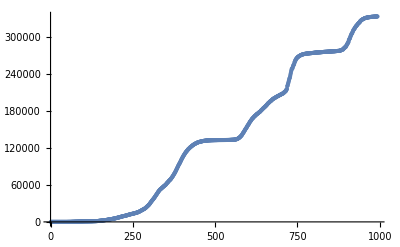

```mathematica
ListPlot[covidData[[3,5;;]]]
```

```mathematica
{1 , 2 , 3 , 4}[[-2;;]]
```

{3,4}